# 2. Fourier Series and Transforms

## 2.1 Fourier Representation of Periodic Functions

2.1.1 Introduction

A  function f(t) is periodic with period T when, for any value of t,

f(t)=f(t+T).

An example of a periodic function is shown in Fig. 2.1. We have already encountered simple examples of periodic functions: the functions sin t, cos t, and tan t are periodic with periods 2π, 2π, and π respectively.

Functions that have period T are also periodic over longer time intervals 2T, 3T, 4T, ... . This follows directly from Eq. (2.1.1):

f(t)=f(t+T)=f(t+2T)=f(t+3T)= ... .

For example, sin t has period 2π, but also has period 4π, 6π,.... We can define the fundamental period of a periodic function as the smallest period T for which Eq. (2.1.1) holds. So the fundamental period of sin t is 2π, and that of tan t is π. When we speak of the period of a function, we usually mean its fundamental period. We will also have occasion to discuss the fundamental frequency Δω = 2 π/T of the function.

Fig. 2.1 A periodic function with period T=1.

Why should we care about periodic functions? They play an important role in our quest to determine the particular solution to an ODE due to arbitrary forcing. In Sec. 1.6, we found the response of an oscillator to a simple periodic sine or cosine forcing.  However, this response will clearly be more complicated for periodic forcing of the type shown in Fig. 2.1. We  can determine this response by first writing the periodic forcing function as a sum of simple sine and cosine functions. This superposition is called a Fourier series, after the French mathematician Jean Fourier, who first showed how such a series can be constructed. Once we have this series for the forcing function, we can use the superposition principle to write the response of the oscillator as a sum of the individual responses to the individual cosine and sine terms in the series.

Later, we will find that Fourier series representation of periodic functions (and generalizations to the representation of nonperiodic functions) are also very useful in a number of other applications, such as the solution to certain common partial differential equations.

In order to expand a  given periodic  function f(t) as a sum of sine and cosine functions, we must choose sines and cosines with the same periodicity as f(t) itself. Since f(t) has period T, we will therefore choose the functions sin 2π t/T, sin 4π t/T, sin 6π t/T...  and   1, cos 2π t/T, cos 4π t/T, cos 6π t/T,.... These functions have fundamental periods T/n for integers n=0,1,2,3,..., and therefore by Eq. (2.1.2) are also periodic with period T. Note that the constant function 1, with undefined period, is included. A few of these functions are shown in Cells 2.1 and 2.2

```mathematica
Manipulate[T=1; Plot[Sin[2n Pi t/T],{t,0,T}],{n,1,5,1,Appearance->"Labeled"}]
```

```mathematica
Manipulate[Plot[Cos[2n Pi t/T],{t,0,T},PlotRange->{-1.5,1.5}],{n,0,5,1,Appearance->"Labeled"}]
```

One can see that both cos 2π n t/T and sin 2 π n t/T become more and more rapidly varying as n increases. The more rapidly varying functions will be useful in helping describe rapid variation in f(t).

A general linear combination of these sines and cosines constitutes a Fourier series, and has the form

a_o+∑_(n=1)^∞ (a_n cos 2 π n t/T+b_n sin 2π n t/T),

where the constants a_n and b_n  are called  Fourier coefficients. The functions cos 2 π n t/T and sin 2π n t/T are often referred to as Fourier modes.

It is easy to see that the above Fourier series has the correct period T. If we evaluate the series at time t+T, the nth cosine term is cos[2 π n (t+T)/T]=cos(2π n t/T + 2 π n)=cos 2π n t/T , where in the last step we have used the fact that cosine functions have period 2π. Thus, the cosine series at time t+T returns to the form it had at time t.  A similar argument shows that the sine series evaluated at time t+T also returns to its  form at time t. Therefore, according to Eq. (2.1.1) the series is periodic with period  T.

The fact that Fourier coefficients can be found that allow this series to equal a given periodic function f(t) is a consequence of the following theorem:

Theorem 2.1	
	If a periodic function f(t) is continuous, and its derivative is nowhere infinite and is sectionally continuous, then it is possible to construct a Fourier series that equals f(t) for all t.

A sectionally continuous periodic function is one that is continuous in finite-size sections, with either no discontinuities at all or at most a finite number of discontinuities in one period of the function. Figure 2.1 is an example of a sectionally continuous periodic function.  We will see later in this section what happens to the Fourier representation of f(t) when f(t) violates the restrictions placed on it by Theorem 2.1 . For now, we  assume that the function f(t) satisfies the requirements of the theorem, in which case Fourier coefficients can be found such that

f(t) =a_o+∑_(n=1)^∞ (a_n cos 2 π n t/T+b_n sin 2π n t/T )  for all t.

2.1.2 Fourier Coefficients and Orthogonality Relations

We are now ready to find the Fourier coefficients a_n and b_n  that enter into the Fourier series representation of a given  periodic function f(t).  These coefficients can be found by using an important property of the sine and cosine functions that appear in Eq. (2.1.3): the property of orthogonality. Two real functions g(t) and h(t) are said to be orthogonal on the interval  [a,b] if they satisfy

∫_a^b g(t)h(t)ⅆt=0.

The sine and cosine Fourier modes in Eq. (2.1.3) have this property of orthogonality on the interval [t_o, t_o+T] for any choice of t_o. That is, for integers m and n  the Fourier modes satisfy

∫_t_o^(t_o+T) sin(2π n t/T) sin(2 π m t/T)ⅆt=∫_t_o^(t_o+T) cos(2π n t/T) cos(2 π m t/T)ⅆt=0,    m≠n

∫_t_o^(t_o+T) sin(2π n t/T) cos(2 π m t/T)ⅆt=0.

In the first equations, the restriction m≠n was applied, because a real function cannot be orthogonal with itself: for any real function g(t) that is nonzero on a finite range within [a,b],  ∫_a^b g^2(t)ⅆt must be greater than zero. This follows simply because g^2(t)≥ 0, so there is a finite positive area under the  g^2(t) curve. For this reason, when  m=n  in Eq. (2.1.5), the first and last integrals return a positive result:

∫_t_o^(t_o+T) sin^2(2π n t/T) ⅆt=∫_t_o^(t_o+T) cos^2(2π n t/T) ⅆt=T/2,   n≠ 0,

∫_t_o^(t_o+T) cos^2(2π 0 t/T) ⅆt=T.

The last equation follows because cos 0=1. The analogous equation for the sine functions,

∫_t_o^(t_o+T) sin^2(2π 0 t/T) ⅆt=0,

is not required, since sin 0 =0 is a trivial function that plays no role in our Fourier series.  Equations (2.1.5) and (2.1.6) can be proven using Mathematica:

```mathematica
g = {Sin,Cos};
Table[Table[FullSimplify[Integrate[g[[i]][2 Pi n t/T] g[[j]][2 Pi m t/T],{t,t0,t0+T}],n ≠ m && n∈Integers&&m∈Integers],{j,i,2}],{i,1,2}]
```

{{0,0},{0}}

```mathematica
Table[FullSimplify[Integrate[g[[i]][2 Pi n t/T] ^2,{t,t0,t0+T}],n∈Integers],{i,1,2}]
```

{T/2,T/2}

Note that in Cell 2.4 , we did not specify that n>0, yet Mathematica gave us results assuming that n ≠ 0. This is a case where Mathematica has not been sufficiently careful. We also need to be careful: as we can see in Eqs. (2.1.5)-(2.1.7),

The n=0 Fourier cosine mode is a special case that must be dealt with separately from the other modes.

These orthogonality relations can be used to extract the Fourier coefficients from  Eq. (2.1.3). For a given periodic function f(t), we can determine the coefficient a_m by multiplying both sides of  Eq. (2.1.3) by cos 2 π m t/T and integrating over one period, from t_oto t_o+T for some choice of  t_o:

∫_t_o^(t_o+T) f(t) cos (2 π m t)/T ⅆt=∑_(n=0)^∞ a_n ∫_t_o^(t_o+T) cos(2 π n t)/T cos(2 π m t)/T ⅆt+∑_(n=1)^∞ b_n ∫_t_o^(t_o+T) sin(2 π n t)/T cos(2 π m t)/T ⅆt.

The orthogonality of the sine and cosine Fourier modes, as shown by Eq. (2.1.5), implies that every term in the sum involving b_n vanishes.  In the first sum, only the n=m term provides a nonzero integral, equal to T/2  for m≠ 0 and T for m=0 according to Eq. (2.1.6). Dividing through by these constants, we arrive at

a_o=1/T∫_t_o^(t_o+T) f(t)ⅆt,

a_m=2/T∫_t_o^(t_o+T) f(t) cos((2 π m t)/T)ⅆt,   m>0.

Similarly, the  b_n's are determined by multiplying both sides of  Eq. (2.1.3) by sin 2 π m t/T and integrating from t_oto t_o+T for some choice of  t_o. Now orthogonality  causes all terms involving the a_n's to vanish, and only the term proportional to b_m survives. The result is

b_m=2/T∫_t_o^(t_o+T) f(t) sin(2 π m t)/T ⅆt,   m>0.

2.1.3 Triangle Wave

Equations (2.1.3), (2.1.9), and (2.1.10) provide us with everything we need to determine a Fourier series for a given periodic function f(t). Let's use these equations to construct Fourier series representations for some example functions. Our first example will be a triangle wave of period T. This function can be created from the following Mathematica commands, and is shown in Cell 2.5 for the case of T=1.

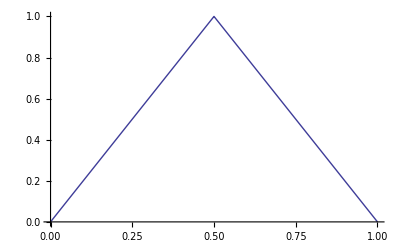

```mathematica
f[t_] := 2t/T /; 0≤ t<T/2;
f[t_] := 2 - 2t/T /; T/2 ≤ t <T;
T=1; Plot[f[t],{t,0,T}]
```

This is only one period of the wave. To create a periodic function, we need to define f for the rest of the real line. This can be done using Eq. (2.1.1), the definition of a periodic function, as a recursion relation for f:

```mathematica
f[t_] := f[t-T] /; t>T ;
f[t_] := f[t+T] /; t<0
```

Now we can plot the wave over several periods, as shown in Cell 2.7.

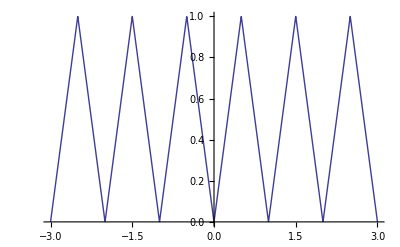

```mathematica
Plot[f[t],{t,-3T,3T}]
```

This function is continuous, and its derivative is sectionally continuous and not singular, so according to Theorem 2.1 the Fourier series representation of  f should work. To test this conclusion, we first need to determine the Fourier coefficients. The a_n's are evaluated according to Eq. (2.1.9). We will perform this integral in Mathematica analytically, by choosing t_o=0 and breaking the integral over f(t) into two pieces:

```mathematica
Clear[T];a[n_] = FullSimplify[(2/T)Integrate[Cos[2 Pi n t/T] 2 t/T,{t,0,T/2}] + (2/T)Integrate[Cos[2 Pi n t/T](2-2t/T),{t,T/2,T}],n∈Integers]
```

-(2 (-1)^n (-1+(-1)^n))/(n^2 π^2)

```mathematica
a[0] = Simplify[(1/T)Integrate[2 t/T,{t,0,T/2}] + (1/T)Integrate[(2-2t/T),{t,T/2,T}]]
```

1/2

A list of a_n-values can now be constructed:

```mathematica
Table[a[n],{n,0,10}]
```

{1/2,-4/π^2,0,-4/(9 π^2),0,-4/(25 π^2),0,-4/(49 π^2),0,-4/(81 π^2),0}

For future reference, we reproduce these results for our triangle wave below:

a_n=-4/(n^2 π^2),  n odd,
a_o = 1/2.

Similarly, we can work out the b_n's by replacing the cosine functions in the above integrals with sine functions. However, we can save ourselves some work  by noticing that f(t) is an even function of t:

f(-t)=f(t).

Since sine functions are odd in t, that is, sin(-ω t)=-sin ω t , the Fourier sum involving the sines is also an odd function of t, and therefore cannot enter into the representation of the even function f. This can be proven rigorously if we choose t_o=-T/2 in Eq. (2.1.10). The integrand is an odd function multiplied by an even function, and is therefore odd. Integrating this odd function from -T/2 to T/2 must yield zero, so therefore b_n=0.

For an even function f(t), the Fourier representation involves only Fourier cosine modes; for an odd function it involves only Fourier sine modes.

Thus, our triangle wave can be represented by a Fourier cosine series. We can construct this series in Mathematica provided that we keep only a finite number of terms; otherwise the evaluation of the series takes an infinitely long time. Let's keep only M terms in the series, and call the resulting function f_approx(t,M):

```mathematica
Subscript[f, approx][t_,M_] := Sum[a[n] Cos[2Pi n t/T],{n,0,M}]
```

For a given period T we can plot this function for increasing M values and watch how the series converges  to the triangle wave: see Cell 2.12.

```mathematica
T=1;plts=Table[Plot[Subscript[f, approx][t,M],{t,0,2},PlotRange->{-.2,1.2},PlotLabel->Grid[{{"M = ",M}}]],{M,1,11,2}]; ListAnimate[plts]
```

One can see that as M increases, the series approximation to f is converging quite nicely. This is to be expected: according to Eq. (2.1.11), the Fourier coefficients a_n fall off with increasing n like 1/n^2, so coefficients with large n make a negligible contribution to the series.

Although the series converges, convergence is more rapid in some places than others. The error in the series is greatest near the sharp points in the triangle wave. This should come as no surprise, since a sharp point introduces rapid variation that is difficult  to reproduce using smoothly varying cosine Fourier modes. Functions with rapid variation must be described by rapidly varying cosine and sine functions, which means that M>>1 terms must be kept in the Fourier series.

Functions that vary smoothly can be well- described by a finite Fourier series keeping a relatively small number of terms. Functions with more rapid variation need more terms in the series.

Perhaps it is now starting to become clear as to why the restrictions on f(t) are necessary in Theorem 2.1. If f(t) has a discontinuity or its derivative is singular, it cannot be represented properly by sine and cosine functions, because these functions do not have discontinuities or singularities.

2.1.4 Square Wave

Our next example is a good illustration of what happens when a function violates the restrictions of Theorem 2.1. Consider a square wave with period T, defined by the following Mathematica commands:

```mathematica
Clear[f];
f[t_] := 1 /; 0≤ t<T/2;
f[t_] := -1 /; -T/2 ≤  t < 0
```

The definition of f is extended over the entire real line using the same recursive technique as for the triangle wave, as shown in Cell 2.14.

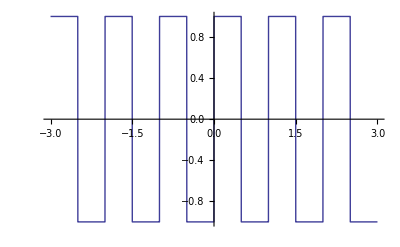

```mathematica
f[t_] := f[t+T] /; t<-T/2;
f[t_] := f[t-T] /; t>T/2;
T=1; Plot[f[t],{t,-3,3}]
```

Our square wave has been defined as an odd function, satisfying

f(-t)=-f(t),

and therefore its Fourier representation will be as a sine series. The Fourier coefficients b_n follow from Eq. (2.1.10), and can be determined using Mathematica as follows:

```mathematica
b[n_] = FullSimplify[2/T (-Integrate[Sin[2 Pi n t/T],{t,-T/2,0}] +
Integrate[Sin[2 Pi n t/T],{t,0,T/2}]),n∈Integers]
```

-(2 (-1+(-1)^n))/(n π)

Thus, this Fourier series has the simple form

f_approx(t, M)=4/π Σ_(n=1(n odd))^M 1/n sin(2 π n t/T)  .

The Fourier coefficients fall off rather slowly as n increases, like 1/n .  The coefficients for the triangle wave fell off more rapidly, as 1/n^2 [see Eq. (2.1.11)]. This makes some sense, since  the square wave is discontinuous and the triangle wave continuous,  so the high-n terms in the square wave series have more weight.  However, this is also a problem: because the high-n terms are so important, our finite approximation to the series will not converge the same way as for the triangle wave. Let's construct a finite series, f_approx(t,M), and view its convergence with a table of plots as we did previously for the triangle wave. This is done in Cell 2.16.

```mathematica
Subscript[f, approx][t_,M_] := Sum[b[n] Sin[2Pi n t/T],{n,1,M}];
T=1;
plts=Table[Plot[Subscript[f, approx][t,M],{t,-1,1},PlotRange->{-1.5,1.5},PlotLabel->Grid[{{"M = ",M}}]],{M,4,20,4}];ListAnimate[plts]
```

The series is clearly not converging as well as for the triangle wave. The discontinuity in the square wave is difficult to represent using a superposition of smoothly varying Fourier modes.

2.1.5 Uniform and Nonuniform Convergence

It is useful to consider the difference between the series approximation and the exact square wave as M increases. This difference is evaluated and plotted in Cell 2.17.

```mathematica
errorplot[M_] := (a = Subscript[f, approx][t,M]; Plot[a-f[t],{t,-0.5,0.5},PlotRange->{-1,1},PlotPoints->100M,PlotLabel->Grid[{{"Error, M =",M}}]]);

ListAnimate[Table[errorplot[M],{M,10,50,10}]]
```

The error has a maximum value of  ±1 at the discontinuity points t=m T/2, independent of M.  This maximum error is easy to understand: the square wave takes on the values ±1 at these points, but the Fourier series is zero there because at t=m T/2 the nth term in the series is proportional to sin(n m π)=0.

Furthermore, each successive peak in the error has a value that is independent of M: the first peak on the right side of the origin is at about 0.2, the next is at about 0.1, and so on, independent of M.   In fact, in the next subsection we will show that the maximum size of error of the first peak is 0.1789..., that of the second is 0.0662..., independent of M. The constancy of these maximum errors as M increases is most easily observed by animating the above set of graphs. What you can see from the animation is that while the height of the peaks is independent of M,  the width of the peaks shrinks as M increases, and the peaks crowd in toward the origin. This strange behavior is called the Gibbs phenomenon.

As a result of the Gibbs phenomenon,  for any finite value of M, no matter how large, there is always a small region around the discontinuity points where the magnitude of the error is independent of M. Although this region shrinks in size as M increases, the fact that the error is independent of M within this region distinguishes the behavior of this Fourier series from that of a function that satisfies the restrictions of Theorem 2.1, such as the triangle wave studied previously. There, the error in the series decreased uniformly  as M increased.  By this we mean that, as M increases, |f_approx(t,M)-f(t)|→0 for all t . This is called uniform convergence of error, and it is necessary in order for us to state that the left-hand and right-hand sides of Eq. (2.1.3) are strictly equal to one another for every t.

More precisely, as M  increases,  a uniformly convergent series satisfies

|f_approx(t,M)-f(t)|<ϵ(M)

where ϵ(M) is some small number that is independent of t and that approaches zero as M→ ∞. Thus, the error in the series is bounded by ϵ(M), and this error goes to zero as M  increases, independent of the particular value of t.

On the other hand, the behavior of the error in the series representation of the square wave is an example of nonuniform convergence.  Here Eq. (2.1.15) is not satisfied for every value of t: we can find a small range of t-values around the discontinuities for which the error is not small, no matter how large we take M.

Functions thay satisfy the restrictions of Theorem 2.1 have Fourier series representations that converge uniformly.  But even for nonuniformly convergent series,  the previous analysis of the square wave series show that the series can still provide  a reasonably accurate representation of the function, provided that we stay away from the discontinuity points. Thus, Fourier series are often used to approximately describe functions that have discontinuities, and even singularities. The description is not exact for all t, but the error can be concentrated into small regions around the discontinuities and singularities by taking M  large. This is often sufficient for many purposes in scientific applications, particularly in that there are no real discontinuities or singularities in nature; such discontinuities and singularities are always the result of an idealization, and therefore we usually need not be too concerned if the series representation of such functions does not quite describe the singular behavior.

2.1.6 Gibbs Phenomenon for the Square Wave

The fact that the width of the oscillations in the error decreases as M increases suggests that we attempt to understand the Gibbs phenomenon by applying a scale transformation to the time: let τ=M t/T . For constant τ the actual time t approaches zero as M increases. The hope is  that in these scaled time units, the compression of the error toward the origin observed in the above animation will disappear, so that on this time scale the series will become independent of M as M increases.

In these scaled dimensionless time units, the series, Eq. (2.1.14) takes the form

f_approx(τ, M)=4/π Σ_(n=1(n odd))^M 1/n sin(2 π n τ/M)  .

There is still M-dependence in this function, so we will perform another scale transformation, defining n=M s. Substituting this transformation into Eq. (2.1.16) yields

f_approx(τ, M)=4/(π M)Σ_(s=1/M,3/M,5/M...)^1 1/s sin(2 π s τ)  .

The function (sin 2 π s τ)/s  is independent of M and is well behaved as s varies  on [0,1], taking the value 2 πτ at s=0. Furthermore, the interval Δs=2/M between successive s-values decreases to zero as M increases, so we can replace the sum by an integral over s from 0 to 1:

lim_(Δs→ 0) (Δs Σ_(s=Δs/2,(3Δs)/2,(5Δs)/2,...)^1 1/s sin(2 π s τ))=∫_0^1 1/s sin(2 π s τ) ⅆs.

Substituting this integral into Eq. (2.1.17) yields the following result for f_approx:

f_approx(τ, M)=2/π∫_0^1 1/s sin(2 π s τ) ⅆs

As we hoped, f_approx is now independent of M when written in terms of the scaled time τ. It can be evaluated in terms of a special function called a sine integral:

```mathematica
Subscript[f, approx][τ_] = Simplify[2/Pi Integrate[Sin[2 Pi s τ]/s,{s,0,1}],Im[τ]==0]
```

(2 SinIntegral[2 π τ])/π

A plot of this function vs. scaled time τ (Cell 2.19) reveals the characteristic oscillations of the Gibb's phenomenon that we observed previously.

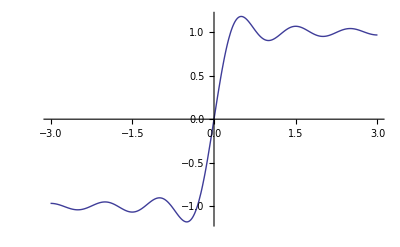

```mathematica
Plot[Subscript[f, approx][τ],{τ,-3,3}]
```

The largest error in the function occurs at the first extremum (see Cell 2.20).

```mathematica
D[Subscript[f, approx][τ],τ]
```

(2 Sin[2 π τ])/(π τ)

This derivative vanishes at τ=n/2, n≠0. The plot of  f_approx shows that τ=1/2 is the location of the first extremum. The maximum value of f_approx is  therefore

```mathematica
Subscript[f, approx][1/2]
```

(2 SinIntegral[π])/π

```mathematica
%//N
```

1.17898

Thus, the maximum  overshoot of the oscillation above 1 is 0.17898.... The next maximum in f_approxoccurs at τ=3/2, with an overshoot above 1 of

```mathematica
Subscript[f, approx][3/2] -1 //N
```

0.0661865

If we return to regular time units and plot  f_approx vs. t for different values of M, we can reproduce the  manner in which the oscillations crowd toward the origin as M  increases - see Cell 2.24.

```mathematica
ListAnimate[Table[Plot[Subscript[f, approx][M t],{t,-1,1},PlotRange->{-1.5,1.5},PlotLabel->Grid[{{"M =",M}}]],{M,4,20,4}]]
```

Near the time origin, the result looks identical to the behavior of the square wave Fourier series plotted in Cell 2.16, except that now f_approx is no longer periodic in t. The periodic nature of f_approx  has been lost, because our integral approximation in Eq. (2.1.18) is correct only for t close to zero. [Equation (2.1.18) assumes  τ remains finite as M→ ∞, so t→ 0.]

2.1.7 Exponential Notation for Fourier Series

In Sec. 1.6 we found that it could be useful to write a real periodic oscillation a cos ω t + b sin ω t in the more compact complex notation, Re[C exp(-ⅈ ω t)], where C is a complex number. We can do the same thing for a Fourier series representation of a real periodic function of period T:

f(t) =a_o+∑_(n=1)^∞ a_n cos (n Δω t)+∑_(n=1)^∞ b_n sin (n Δω t) .

Here we have written the series in terms of the  quantity Δω = 2π/T, which is the fundamental frequency of the periodic function  (see Sec. 2.1.1).

In order to write this series in complex form, we will use the trigonometric identities

cos x = (ⅇ^(ⅈ x)+ⅇ^(-ⅈ x))/2,    sin x = (ⅇ^(ⅈ x)-ⅇ^(-ⅈ x))/2ⅈ .

When these identities are employed in Eq. (2.1.20), and we combine the common terms involving ⅇ^(ⅈ n Δω t) and ⅇ^(-ⅈ n Δω t), we obtain

f(t) =a_o+ ∑_(n=1)^∞ (a_n+ⅈ b_n)/2 ⅇ^(-ⅈ n Δω t)+∑_(n=1)^∞ (a_n-ⅈ b_n)/2 ⅇ^(ⅈ n Δω t).

Note that, for real a_n and b_n, the second sum is the complex conjugate of the first sum. Using the fact that z + z^*=2Re z for any complex number z, we see that Eq. (2.1.22) can be expressed as

f(t)=a_o+Re[∑_(n=1)^∞ (a_n+ⅈ b_n) ⅇ^(-ⅈ n Δω t)].

If we now introduce complex Fourier coefficients C_n, defined as

C_o=a_o,
C_n = a_n+ ⅈ b_n,  n>0,

we can write Eq. (2.1.22)  in the following compact form:

f(t)=Re[∑_(n=0)^∞ C_n ⅇ^(-ⅈ n Δω t)].

Equation (2.1.25) is one form for an exponential Fourier series, valid for real functions f(t). Another form that can also be useful follows from Eq. (2.1.22) by defining  a different set of complex Fourier coefficients  c_n :

c_o=a_o,
c_n=( a_n+ ⅈ b_n)/2,  n>0,
c_n=( a_-n- ⅈ b_-n)/2,  n<0.

The definition of these coefficients is extended to n<0 for the following reason: this extension allows us to express the second  sum in Eq. (2.1.22) as  ∑_(n=1)^∞ c_-n ⅇ^(ⅈ n Δω t). Then by taking n→ -n in this sum, and noting that this inversion changes the range of the sum to -∞ to -1, we can combine the two sums and obtain

f(t)=∑_(n=-∞)^∞ c_n ⅇ^(-ⅈ n Δω t).

Equation (2.1.27) is a second form for the exponential Fourier series. It differs from the first form in that the real part is not  taken, and instead the sum runs over both negative and positive n, from -∞ to +∞. Also, note that we did not assume that a_n and b_n are real, so Eq. (2.1.27) works for complex periodic functions f(t) as well as for real periodic  functions. For this reason, Eq. (2.1.27) is somewhat more general than Eq. (2.1.25), which applies only to real functions.

We are now left with the question of how to determine the complex Fourier coefficients. Of course, we could determine the real coefficients a_n and  b_n and then use either Eqs. (2.1.24) or Eqs. (2.1.26), but it would be better if we could determine the complex coefficients  c_n (or C_n) directly without reference to the real coefficients. This can be done by using a new set of orthogonality relations, valid for complex exponential functions.

Before we can consider these orthogonality relations, we must first extend the notion of orthogonality, Eq. (2.1.4),  to cover complex functions. Two complex functions g(t) and h(t) are said to be orthogonal on the interval [a,b] if they satisfy

∫_a^b g(t)(h(t))^*ⅆt=0.

The complex conjugation is added to the definition so that we can again say that a function cannot be orthogonal with itself: ∫_a^b g(t)(g(t))^*ⅆt=∫_a^b |g(t)|^2 ⅆt≥ 0, with equality only for a function that equals zero across the interval. Of course, we could equally well have taken the complex conjugate of g rather than h in Eq. (2.1.28), ∫_a^b (g(t))^*h(t)ⅆt=0.

The complex exponential Fourier modes, ⅇ^(-ⅈ n Δω t)( with Δω = 2 π/T), satisfy the following orthogonality relations on the interval t_o to t_o+T, for any choice of  t_o:

∫_t_o^(t_o+T) (ⅇ^(-ⅈ n Δω t)(ⅇ^(-ⅈ m Δω t)))^*ⅆt=0, m≠n.

This can easily be proven using a couple of lines of algebra:

∫_t_o^(t_o+T) (ⅇ^(-ⅈ n Δω t)(ⅇ^(-ⅈ m Δω t)))^*ⅆt=∫_t_o^(t_o+T) ⅇ^(-2π ⅈ(n-m)  t/T)ⅆt=T/(-2π ⅈ(n-m))[ⅇ^(-2π ⅈ(n-m)  (t_o+T)/T)-ⅇ^(-2π ⅈ(n-m)  t_o/T)]= T/(-2π ⅈ(n-m))ⅇ^(-2π ⅈ(n-m)  t_o/T)[ⅇ^(-2π ⅈ(n-m))-1] = 0.

The case where m=n is even simpler:

∫_t_o^(t_o+T) (ⅇ^(-ⅈ n Δω t)(ⅇ^(-ⅈ n Δω t)))^*ⅆt=∫_t_o^(t_o+T) ⅇ^(-ⅈ 0)ⅆt=T.

Equations (2.1.29) and (2.1.30) can now be used to determine the Fourier coefficients c_n  for a given function f(t). To do so, we multiply both sides of the equation by (ⅇ^(-ⅈ m Δω t))^*, and integrate over one period :

∫_t_o^(t_o+T) (ⅇ^(-ⅈ m Δω t))^*f(t)ⅆt=∑_(n=-∞)^∞ c_n ∫_t_o^(t_o+T) (ⅇ^(-ⅈ m Δω t))^*ⅇ^(-ⅈ n Δω t)ⅆt.

Then, according to Eq. (2.1.29), all terms in the sum vanish, except for the n=m term, which, after applying Eq. (2.1.31), equals c_m T. Thus, we find

c_m =1/T ∫_t_o^(t_o+T) (ⅇ^(-ⅈ m Δω t))^*f(t)ⅆt.

Equations (2.1.33) and (2.1.27) allow us to write any periodic function f(t) as an exponential Fourier series. Of course, the function must satisfy the requirements of Theorem 2.1 in order for the series to converge uniformly to f.

For real f we can also write the series in the form of Eq. (2.1.25) by using Eq. (2.1.33) along with the relations

C_o=c_o,
C_n=2 c_n, n>0,

which follow from comparing Eqs. (2.1.24) and (2.1.26).

Two representations of an exponential Fourier series (the first is valid only for real f(t)):
 (1)  f(t)=Re[∑_(n=0)^∞ C_n ⅇ^(-ⅈ n Δω t)] ,
(2)  f(t)=∑_(n=-∞)^∞ c_n ⅇ^(-ⅈ n Δω t).
where
 C_o=c_o,
C_n=2 c_n, n>0,
and
c_n =1/T ∫_t_o^(t_o+T) (ⅇ^(-ⅈ n Δω t))^*f(t)ⅆt for all n

2.1.8 Response of a Damped Oscillator to Periodic Forcing

Armed with the knowledge we have gained in previous sections, we can now return to the question put forward at the beginning of the chapter: what is the response of a damped oscillator to general periodic forcing f(t)?

We will find a particular solution x_p(t) to the oscillator equation ((1.6.2)) in the form of an exponential Fourier series:

x_p(t) = ∑_(n=-∞)^∞ x_n ⅇ^(-ⅈ n Δω t),

where x_n is the complex Fourier coefficient of x_p(t),  Δω = 2π/T is the fundamental frequency of the given periodic forcing function, and T is the fundamental period of the forcing. If we substitute Eq. (2.1.35) into Eq. (1.6.2), we obtain

∑_(n=-∞)^∞ x_n [-( n Δω)^2 -ⅈ γ  n Δω +ω_o^2]ⅇ^(-ⅈ n Δω t)=f(t).

Finally, we can  extract the Fourier coefficient  x_n by multiplying both sides by  (ⅇ^(-ⅈ n Δω t))^*, integrating over a period of the force, and using the orthogonality relations Eq. (2.1.29) and (2.1.31). The result is

x_n=c_n/[-( n Δω)^2 -ⅈ γ n Δω +ω_o^2],

where c_n is the nth  Fourier coefficient of the forcing function, given by Eq. (2.1.33).

This simple expression contains a considerable amount of physics. First, note that each Fourier mode in the force drives a single Fourier mode in the oscillator response. For the case of a strictly sinusoidal force, Eqs. (2.137) and (2.1.35) reduce to  Eq. (1.6.45).

Second, the principle of superposition is implicitly coming into play: according to Eq. (2.1.35), the total oscillator response is a linear superposition of the responses from the individual Fourier modes. However, each mode is independently excited, and has no effect on other modes.

Third, note that for high-n Fourier modes, the response is roughly x_n~-c_n/( n Δω)^2, which approaches zero more rapidly with increasing n than do the forcing coefficients c_n. Basically, this is an effect due to inertia of the oscillator: a very high frequency forcing causes almost no effect on an oscillator,  because the oscillator's inertia doesn't allow it to respond before the force changes sign.

Fourth, for very low-frequency forcing, such that ( n Δω)^2<< ω_o^2 for all Fourier modes entering the force, the response is x_n~c_n/ω_o^2. We can then re-sum the series according to Eq. (2.1.35) and (2.1.27), to find that the oscillator amplitude tracks the forcing as x_p(t)~f(t)/ω_o^2. This makes sense intuitively: according to Hooke's law, when you slowly change the force on a spring, it responds by changing its length in proportion to the applied force.

Finally, note that some Fourier modes are excited to higher levels than other modes. For  Fourier modes that satisfy ( n Δω)^2≃ω_o^2, the denominator in Eq. (2.1.37) is close to zero if γ is small, and the system response exhibits the resonance phenomenon discussed in Sec. 1.6.4. These resonant modes are driven to large amplitude. For the case of an undamped oscillator ( γ=0) and exact resonance (n Δω = ω_o for some value of n), Eq. (2.1.37) does not apply. The resonant response is no-longer described by a Fourier mode, but rather by a growing oscillation. The form of this oscillation can be found using the methods for exact resonance discussed in Sec. 1.6.4.

Resonance phenomena are of great importance in a number of systems, including the system to be discussed in the next section.

2.1.9 Fourier Analysis, Sound, and Hearing

The sound that a sinusoidal oscillation makes is a pure tone. Mathematica can play such sounds with the intrinsic function Play. For example, the sound of the pure note "middle A" is a sinusoid with frequency ω = 2 π × 440 s^-1; the command and visible response are shown in Cell 2.25.

```mathematica
Play[Sin[2 Pi 440 t],{t,0,1}]
```

-Graphics-

Play assumes that the  time t is given in seconds, so this command causes a pure middle A tone to play for 1 second.

We can also play other sounds. For example, we can play the sound of a triangle wave, which has a distinctive buzzing quality:

```mathematica
T=1/440; a[n_] = -4/(n^2 Pi^2);Subscript[f, approx][t_,30] = Sum[a[n] Cos[2 Pi n t/T],{n,1,30,2}];

triangle = Play[Subscript[f, approx][t,30],{t,0,1},PlayRange->{-0.6,0.6}]
```

-Graphics-

Here we have used the Fourier series for a triangle wave, with coefficients as listed in Eq. (2.1.11), keeping 30 coefficients, and neglecting the n=0 term (since it merely produces a constant offset, of no importance to the sound).We have also added an option PlayRange, which is analogous to PlotRange for a plot,  setting the range of amplitude levels to be included; it can be used to adjust the volume of the sound.

The harsh buzzing sound of the triangle wave compared to a pure sine wave is caused by the high harmonics of the fundamental middle A tone that are kept in this series.

Let's now consider the following question: what happens to the sound of the triangle wave if we randomize the phases of the different Fourier modes with respect to one another? That is, let's replace cos(2 π n t/T) with cos[2 π (n t/T+ϕ_n)], where ϕ_n is a random number between 0 and 2π. The resulting series can be written in terms of a sine and cosine series by using the trigonometric identity

cos{2 π (n t/T+ϕ_n)}=cos ϕ_n cos[2 π n t/T]-sin ϕ_n sin[2 π n t/T].

If we plot the series, it certainly no-longer looks like a triangle wave, although it remains periodic with period T, as shown in Cell 2.27.

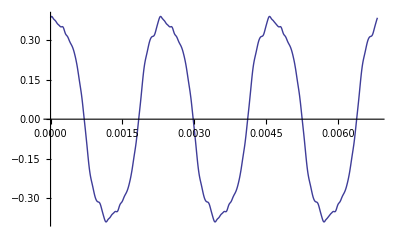

```mathematica
T=1/440; a[n_] = -4/(n^2 Pi^2);
Subscript[f, random][t_,30] = Sum[a[n] Cos[2 Pi (n t/T + Random[])],{n,1,30,2}];
Plot[Subscript[f, random][t,30],{t,0,3T}]
```

The waveform looks very different than a triangle wave, so there is no reason to expect that it would sound the same. However, if we play this waveform (using the same PlayRange as before, as shown in Cell 2.28),

```mathematica
randomizedtriangle=Play[Subscript[f, random][t,30],{t,0,1},PlayRange->{-0.6,0.6}]
Do[EmitSound[randomizedtriangle];EmitSound[triangle],{2}]
```

-Graphics-

the sound is indistinguishable from the triangle wave. This is surprising, given the difference between the shapes of these two waveforms.  One can verify that this is not an accident. By re-evaluating the random phase waveform one gets a different shape each time; but in each case the sound is identical. (Try it!) (Here we have used the EmitSound command, which directly plays previously-defined sounds, in order to compare the sounds made from the two waveforms.)

Why do differently-shaped waveforms make the same sound? The reason has to do with how we perceive sound. Sound is perceived by the brain through the electrical signals sent by nerve cells that line the inner ear. Each nerve cell is attached to a hair that is sandwiched between two membranes - the basilar membrane and the tectorial membrane (see Fig. 2.2). As sound waves move through the fluid in the inner ear, these membranes, immersed in the fluid,  move relative to one another in response. The basilar membrane is thicker and stiffer in some places than in others, so different parts of the membrane are resonant to different frequencies of sound. Therefore, a given sound frequency excites motion only in certain places on the membrane. (This correspondence between frequency and location is called a tonotopic map.)  The motion excites the hairs at these locations, which in turn cause their respective neurons to fire at a rate that depends on the amplitude of the motion, sending signals to the brain that are interpreted as a sound of a given frequency and loudness.

If you think this system sounds complicated, you're right. After all, it is the product of millions of years of evolutionary trial and error. But one can think of it very roughly as just a system of oscillators having a range of  resonant frequencies. Crudely speaking, the ear is doing a Fourier analysis of the incoming sound: the different frequency components of the sound resonantly excite different  hairs, which through the tonotopic map are perceived as different frequencies. The amplitude of a hair's motion is translated into the amplitude of the sound at that frequency. The phase of the motion of the hairs relative to one another is apparently not important  in what we perceive as the quality of the sound (as we have seen, the "sound" of the sound is unchanged by phase modulation of different frequency components).

However, as always seems to be the case in biological systems, things are really more complicated than this crude picture. The phase of the motion of the hairs is not completely ignored by the auditory system, at least for sounds with frequencies less than around 1-1.4 kHz. For this range, neurons are thought to be able to "phase lock" their firing to the phase of the sound - for instance, the neuron might fire only at the peak of the sine wave. (At higher frequencies, the neuron's firing rate apparently cannot keep up with the sound oscillation.)  Experiments have shown that this phase information is used by the brain's auditory system to help locate the source of the sound, by comparing the phase in the right ear with that in the left. (See the exercises.)

Also, the auditory system is not passive. It has recently been shown that the resonant response of the hairs to a sound impulse is actually amplified by molecular motors in the membranes of the hair cells. This amplification allows the response of the system to be considerably more sharply peaked about the resonant frequency than would be the case for a purely passive system with the same damping rate. In fact, the molecular motors cause the hairs to vibrate continuously at a low level, and the sound this motion creates can be picked up by sensitive microphones outside the ear. The ear is not just a passive receiver: it also transmits (albeit at a level below our conscious perception).

In summary, two periodic waveforms will look different if their Fourier components have different relative phases, but they will still sound alike if their Fourier amplitudes are the same.

Fig. 2.2 Simplified diagram of the middle and  inner ear (not to scale).

Exercises for Sec. 2.1

(1) Prove that for a periodic function f(t) of period T, the following is true: ∫_0^T f(t)ⅆt=∫_x^(T+x) f(t)ⅆt  for any x.

(2)(a) Do the following periodic functions meet the conditions of Theorem 2.1?

(i) f(t)=|t|^3  on -1/2<t<1/2;f(t)=f(t+1).

(ii)f(x)=3x  on 0<x<2; f(x)=f(x+2).

(iii) f(t)=exp(-t) on 0<t<3; f(t) = f(t+3) .

(b) Find the  Fourier series coefficients A_n and B_n for the periodic functions of part (a).

(c) Plot the resulting series  for different numbers of coefficients M, 1<M<10, and observe the convergence. Compare with the exact functions. Are the series converging?

(d) Plot the difference between the series and the actual functions as M increases, and determine using Eq. (2.1.15) whether the series are exhibiting uniform convergence.

(e) For the series of function (ii), evaluate the derivative of the series with respect to x, term by term.  Compare it with the derivative of 3x on 0<x<2  by plotting the result for M=10, and M=50. Does the derivative of the series give a good representation of f'(x) ?

(3)(a) Theorem 2.1 provides sufficient conditions for convergence of a Fourier series. There conditions are not necessary, however. Functions that have singularities or singular derivatives can sometimes also have well-behaved convergent Fourier series. For example, use Mathematica to evaluate the Fourier sine-cosine series of the periodic function

f(x)=√x(1-x)  on 0≤ x ≤  1, f(x+1)=f(x),

and plot the result for M=4,8,12,16,20. Does this  series appear to be converging to f(x) as M increases?
[Hint: Don't be afraid of any special functions that Mathematica might spit out when evaluating  Fourier coefficients. You don't need to know what they are (although you can look up their definitions in the Mathematica documentation if you want). Just use them in the series, stand back, and let Mathematica plot out the result.]

(b) At what value of x is the maximum error in the series occurring? Evaluate this maximum error for M=10,30,60,90. According to Eq. (2.1.15), is this series converging uniformly?

(4) Repeat Exercise (2)(b) and (c) using exponential Fourier series.

(5) A damped harmonic oscillator satisfies the equation x''+x'+4x=f(t). The forcing function is given by  f(t)=t^2, -1≤ t≤ 1; f(t+2)=f(t).

(a) Find a particular solution x_p(t) to the forcing in terms of an exponential Fourier series.

(b)  Find a homogeneous solution to add to your particular solution from part a) so as to satisfy the ODE with initial conditions  x(0)=1,x'(0)=0. Plot the solution for 0<t<20.

(6) An undamped harmonic oscillator satisfies the equation x''+ 16 π^2 x=f(t). The forcing function is a square wave of period 1/2 : f(t)=1, 0<t<1/4; f(t)=0, 1/4<t<1/2; f(t+1/2) =f(t).

(a) Find a particular solution to this problem. (Be careful - there is an exact resonance!)

(b) Find a homogeneous solution to add to the particular solution so as to satisfy the ODE with initial conditions x(0)=0,x'(0)=0. Plot the solution for 0<t<20.

(7) An RC circuit (a resistor and capacitor in series) is driven by a periodic sawtooth voltage, with period T, of the form V(t)=V_0 Mod[t/T,1]. Plot V(t) for T=0.002, V_0=1 over a time range 0≤ t<4T.

(a) The charge Q(t) on the capacitor satisfies the ODE R Q'+Q/C = V(t). Find a particular solution for Q(t) (in the form of an  exponential Fourier series) . Add a homogeneous solution to match the initial condition Q(0) = 0.  Plot Q(t) for M=5,10,20 for the case R=500 Ω, C=2 μF, V_0=1 V, T=0.002 s.  Compare the shape of Q(t) for a few periods to the original voltage function.

(b) Play the sawtooth sound V(t), and play the resulting Q(t) as a sound. Play Q(t) again, for R=5000 Ω, all else the same. Would you characterize this circuit as one that filters out high frequencies or low frequencies?

(8)(a)  Rewrite the exponential series of the previous problem for Q(t) as a cos-sin series.  For M=20 compare with the exponential series by plotting both, showing they are identical.

(b) Randomize the phases of the Fourier modes in part (a) by replacing cos( n π Δω t) and  sin( n π Δω t) with  cos(n π Δω t+ ϕ_n) and sin(nπΔω t+(ϕ̄)_n), where ϕ_n and (ϕ̄)_n are random phases  in the range (0,2π), different for each mode, and generated using  2π Random[] . Listen to the randomized series to see if you can tell the difference. Also plot the randomized series for a few periods to verify that the function looks completely different than Q(t).

(9) Find a particular solution  to the following set of coupled ODEs using exponential Fourier series:

x''(t)=-(x-2y)-x'+f_1(t),
y''(t)=-(y-x)+f_2(t),

where f_1(t)=(Mod[t,1])^2 and  f_2(t)=2Mod[t,√2] are two sawtooth oscillations (with  incommensurate periods). Plot the particular solution for 0<t<10. Keep as many terms in the series as you feel are necessary to achieve good convergence.

(10) When a signal propagates from a source that is not directly in front of an observer, there is a time difference between when the signal arrives at the left and right ears. The human auditory systems can use this time delay  to help determine the direction from which the sound is coming. A phase difference between the left and right ears of even 1-2 degrees is detectable as a change in the apparent location of the sound source. This can be tested using Play. Play can take as its argument 	two sound waveforms,  for left  and right  channels of a set of stereo headphones.  For example, 
Play[{Sin[440 2 π t],Sin[440 2 π t + ϕ[t]]},{t,0,10}], plays a sine tone for 10 seconds in each ear, but with a phase advance ϕ(t) in the right ear.

Using a pair of stereo headphones with the above sound, see if you can determine an apparent location of a sound source. Try (a) ϕ(t)= 0.2 t, (b) ϕ(t) = -0.2 t; (c) ϕ(t) = 0. Can you tell the difference? (See Hartmann (1999).) (Warning! The stereo effect in Play may not work on all platforms. Test it out by trying Play[{0,Sin[440 2π t]},{t,0,1}]; this should produce a tone only in the right ear. Repeat for the left ear. Also, make sure the volume is on a low setting, or else crosstalk between your ears may impede the directional effect. )

## 2.2 Fourier Representation of Functions Defined on a Finite Interval

2.2.1 Periodic Extension of a Function

In the previous sections,  Fourier series methods were applied to represent periodic functions. Here, we will apply Fourier methods to functions  f(t) defined only on an interval, a≤ t≤ b. Such functions often appear in boundary-value problems, where the solution of the differential equation is needed only between boundary points a and b.

Functions defined only on an interval are not periodic, since they are not defined outside the interval in question and therefore do not satisfy Eq. (2.1.1) for all t. However, a Fourier representation can be still be obtained by replacing f(t) with a periodic function f^(p)(t), defined on the entire real line -∞<t<∞.

There are several different choices for this periodic function. One choice requires  f^(p)(t) to equal f(t) on a≤ t≤ b, and to have period T=b-a:

f^(p)(t) = f(t),  a<t<b,
f^(p)(t+T)=f^(p)(t).

The function f^(p)(t) is called a periodic extension of f(t). The type of periodic extension given by Eq. (2.2.1) is depicted in Fig. 2.3

Fig. 2.3 Periodic extension of a function f(t) defined on the interval a≤ t≤ b, with a=-1 and b=2.

Since f^(p) is periodic with period T, it can be represented by a Fourier series,

f^(p)(t)=∑_(n=-∞)^∞ c_n ⅇ^(-ⅈ n Δω t),

where Δω=2π/T.  The Fourier coefficients c_n can be found using Eq. ( 2.1.33 ) :

c_n = 1/T∫_a^b f(t)  ⅇ^(ⅈ n Δω t)ⅆt.

The function could also be represented by a Fourier sine-cosine series,

f^(p)(t)=∑_(n=0)^∞ a_n cos( n Δω  t)+∑_(n=1)^∞ b_n sin( n Δω  t),

but usually the exponential form of the series is more convenient.

For example, say that f(t) = t^2 on 0<t<1. The Fourier coefficients are then

```mathematica
c[n_] = Simplify[Integrate[t^2 Exp[ I 2 Pi n t],{t,0,1}],n∈Integers]
```

(1-ⅈ n π)/(2 n^2 π^2)

```mathematica
c[0] = Integrate[t^2,{t,0,1}]
```

1/3

The M-term approximant to the Fourier series for f can then be constructed and plotted as in Cell 2.31.

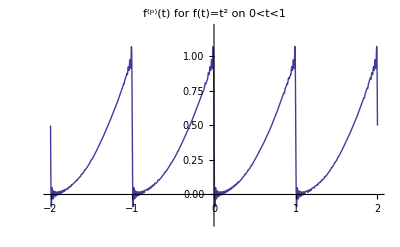

```mathematica
Subscript[f, approx][x_,M_]:= Sum[c[n] Exp[-I 2 Pi n t],{n,-M,M}];

func = Subscript[f, approx][t,50];

Plot[func,{t,-2,2},PlotRange->{-0.2,1.2},PlotLabel->"f^(p)(t) for f(t)=t^2 on 0<t<1"]
```

This M=50 approximation to the complete series exhibits the by now familiar Gibbs phenomenon, due to the discontinuity in the periodic extension of f(t).  For this reason, the series does not converge to f(t) very rapidly; f_n~ -ⅈ/(2 n π) for large n, which implies many terms in the series must be kept to achieve reasonable convergence.

2.2.2 Even Periodic Extension

The problem of poor convergence can be avoided by using a different periodic extension of f(t). Consider an even periodic extension of f,  f^(e)(t), with period 2T rather than T. This extension obeys

f^(e)(t)={f(t),            a<t<a+T,
f(2a-t), a-T<t<a,

f^(e)(t+2T)=f^(e)(t).

The even periodic extension of a function is depicted in Fig. 2.4 It is an even function of t  about the point t=a, and for this reason no longer has a discontinuity. Therefore, we expect that the series for f^(e) will converge more rapidly than that for f^(p), and will no longer display the Gibbs phenomenon associated with nonuniform convergence.

Fig. 2.4 Even periodic extension of a function f(t) defined on the interval -1<t<2.

Since f^(e)(t)is even around the point t=a, the series is of cosine form when time is evaluated with respect to an origin at a:

f^(e)(t)=∑_(n=0)^∞ a_n cos[n Δω( t-a)/2].

Note that the period is now 2T rather than T, so the fundamental frequency is Δω/2.

In order to determine the Fourier coefficients for f^(e), we must now integrate over an interval of 2T. A good choice is the interval a-T<t<a+T, so that the Fourier coefficients have the form

a_n=1/T∫_(a-T)^(a+T) f^(e)(t)  cos[n Δω ( t-a)/2]ⅆt, n>0,
a_o=1/(2T)∫_(a-T)^(a+T) f^(e)(t)  ⅆt.

Let's break the integrals up into two pieces, running from a-T to a and from a to  a+T=b, and use Eq. (2.2.4):

a_n=1/T∫_(a-T)^a f(2a-t)  cos[n Δω ( t-a)/2]ⅆt+∫_a^b f(t)  cos[n Δω ( t-a)/2]ⅆt,   n>0,

a_o=1/(2T)∫_(a-T)^a f(2a-t)  ⅆt +1/(2T)∫_a^b f(t)  ⅆt .

Then, performing a change of variables in the first integral from t to 2a-t,  and using the fact that cos(-t)=cos t for any t, we obtain

a_n=2/T∫_a^b f(t)  cos[n Δω ( t-a)/2]ⅆt ,   n>0,
a_o=1/T∫_a^b f(t)  ⅆt.

Equations (2.2.5) and (2.2.8) allow us to construct an even Fourier series of a function on the interval [a,b], with no discontinuities.  As an example, we will construct f^(e) for the previous case of f(t)=t^2 on [0,1].

```mathematica
T = 1;a[n_] = 2/T Simplify[Integrate[t^2 Cos[2 Pi n t/(2T)],{t,0,T}],n∈Integers]
```

(4 (-1)^n)/(n^2 π^2)

```mathematica
a[0] = 1/T Integrate[t^2,{t,0,1}]
```

1/3

Terms in the series are now falling off like 1/n^2 rather than 1/n, so the series converges more rapidly than the previous series did. This can be seen directly from the plot in Cell 2.34.

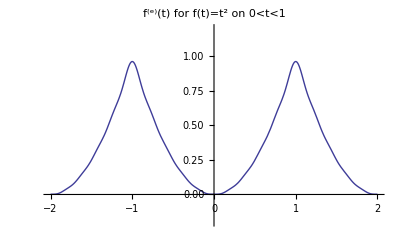

```mathematica
Subscript[f, approx][t_,M_]:= Sum[a[n] Cos[2 Pi n t/(2T)],{n,0,M}];

func = Subscript[f, approx][t,10];

Plot[func,{t,-2,2},PlotRange->{-0.2,1.2},PlotLabel->"f^(e)(t) for f(t)=t^2 on 0<t<1"]
```

Note that we have only kept 10 terms in the series, but it still works quite well. There is no-longer a Gibb's phenomenon; the series converges uniformly and rapidly to t^2 on the interval [0,1].

2.2.3 Odd Periodic Extension

It is also possible to define an odd periodic extension to a function f(t), defined on the interval [a,b]. This extension, f^(o)(t), is odd around the point t=a, and is defined by

f^(o)(t)={    f(t),            a<t<a+T,
-f(2a-t), a-T<t<a,

f^(o)(t+2T)=f^(o)(t).

This type of periodic extension is useful when one considers functions f(t) for which f(a)=f(b)=0. Although  the periodic extension and the even periodic extension of such functions are both continuous at t=a and b, the odd periodic extension also exhibits a continuous first derivative at the boundary points, as can be seen in Fig. 2.5. This makes the series converge even faster than the other types of periodic extension. However, if either f(a) or f(b) is unequal to zero, the convergence will be hampered by discontinuities in the odd periodic extension.

Fig. 2.5 Odd periodic extension of a function f(t) defined on the interval 1<t<3.

Like the even periodic extension, the odd periodic extension also has period 2T. However, since it is odd about the point t=a, it can be written as a Fourier sine series with time measured with respect to an origin at t=a:

f^(o)(t)=∑_(n=1)^∞ b_n sin[n Δω( t-a)/2].

The Fourier coefficients b_n can be determined by following an argument analogous to that which led to Eq. (2.2.8):

b_n=2/T∫_a^b f(t)  sin[n Δω ( t-a)/2]ⅆt .

As an example, let's construct the odd periodic extension of the function t (1-t^2) on the interval [0,1]. This function is zero at both t=0 and t=1, and so meets the conditions necessary for rapid convergence of the odd periodic extension.

The Fourier coefficients are given by

```mathematica
T = 1;b[n_] = 2/T Simplify[Integrate[t(1-t^2)Sin[2 Pi n t/(2T)],{t,0,T}],n∈Integers]
```

-(12 (-1)^n)/(n^3 π^3)

These coefficients fall off as 1/n^3, which is faster than either the coefficients of the even periodic extension,

```mathematica
T = 1;a[n_] = 2/T Simplify[Integrate[t(1-t^2)Cos[2 Pi n t/(2T)],{t,0,T}],n∈Integers]
```

(2 (6 (-1+(-1)^n)-(1+2 (-1)^n) n^2 π^2))/(n^4 π^4)

or the regular periodic extension,

```mathematica
T = 1;c[n_] = 1/T Simplify[Integrate[t(1-t^2)Exp[I 2 Pi n t/T],{t,0,T}],n∈Integers]
```

-(3 (ⅈ+n π))/(4 n^3 π^3)

both of which can be seen to fall off as 1/n^2 for large n.

A plot (Cell 2.38) of the resulting series for the odd periodic extension, keeping only five terms, illustrates the accuracy of the result when compared to the exact function.

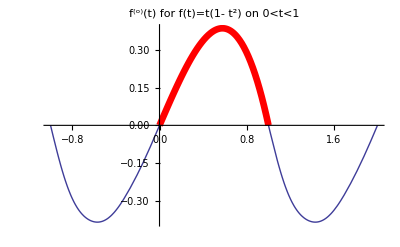

```mathematica
Subscript[f, approx][x_,M_]:= Sum[b[n] Sin[2 Pi n t/(2T)],{n,1,M}];

func = Subscript[f, approx][t,5];
p1 = Plot[t(1-t^2),{t,0,1},PlotStyle->{Red,Thickness[0.012]}];
p2 = Plot[func,{t,-1,2}];
Show[p1,p2,PlotLabel->"f^(o)(t) for f(t)=t(1- t^2) on 0<t<1"];
```

2.2.4 Solution of Boundary-Value Problems Using Fourier Series

In linear boundary-value problems, we are asked to solve for an unknown function ϕ(x) on a given interval a<x<b.  (Here we consider a boundary-value problem in space rather than in time.) The general form of the linear ordinary differential equation is

L̂ ϕ=ρ,

where ρ(x) is a given function of x, and L̂ is some linear differential operator. This equation is supplemented by boundary conditions on ϕ and/or its derivatives at a and b.

Fourier series methods are useful in finding a particular solution ϕ_p to this inhomogeneous ODE, provided that L̂ is a differential operator with constant coefficients, of the form given in Eq. (1.6.7).

For example, consider the problem of determining the electrostatic potential between two parallel conducting plates at positions x=a and x=b, between which there is some given distribution of charge, ρ(x). The potential satisfies the Poisson equation (1.1.10), which in one spatial dimension takes the form

ⅆ^2 ϕ/ⅆ x^2=-ρ(x)/ϵ_o,        ϕ(a)=V_1,    ϕ(b)=V_2,

and where V_1 and V_2are the voltages applied to the two plates.

This problem could be solved by the direct integration technique used to solve Eq. (1.1.1). Here, however, we will use Fourier techniques, since such techniques can also be applied to more complex problems that are not amenable to direct integration. We will run across many more problems of this type in future sections.

To solve this problem using Fourier techniques, we follow the procedure discussed in Sec. 1.6, and break ϕ into a homogeneous and a particular solution:

ϕ=ϕ_h+ϕ_p,

where the particular solution ϕ_p is any solution that  satisfies Eq. (2.2.13):

ⅆ^2 ϕ_p/ⅆ x^2=-ρ(x)/ϵ_o.

After we have found a particular solution, we then solve for a homogeneous solution that satisfies the proper boundary conditions:

ⅆ^2 ϕ_h/ⅆ x^2=0,        ϕ_h(a)=V_1-ϕ_p(a),    ϕ_h(b)=V_2-ϕ_p(b).

In this way, the particular solution takes care of the inhomogeneity, and the homogeneous solution takes care of the boundary conditions. Adding Eqs. (2.2.15) and (2.2.16), one can easily see that the total potential, Eq. (2.2.15), satisfies both ODE and boundary conditions in Eq. (2.2.13).

For this simple ODE, the general homogeneous solution is ϕ_h(x) = C_1 + C_2 x. To find the particular solution using Fourier methods, we replace ϕ_p by a its periodic extension and employ an exponential Fourier series,

ϕ_p(x)=∑_(n=-∞)^∞ ϕ_n ⅇ^(ⅈ 2 π n x /L),

where L=b-a is the length of the interval.

Note the change in sign of the exponential compared to the previous section involving Fourier times series, Eq. (2.1.27). For spatial Fourier series, the above sign is conventional; for Fourier series in time, the opposite sign is used. Of course, either sign can be used as long as one is consistent throughout the calculation, but we will stick with convention and use different signs for time and space series. (Although these different conventions may seem arbitrary and confusing at first, there is a good reason for them, having to do with the form of traveling waves. See Sec. 5.1.1.)

The Fourier coefficients ϕ_n can then be found by substitution of Eq. (2.2.17) into the ODE and taking the derivative of the resulting series term-by-term:

ⅆ^2 ϕ_p/ⅆ x^2=∑_(n=-∞)^∞ (ϕ_n((ⅈ 2π n)/L))^2 ⅇ^(ⅈ 2 π n x /L) =-ρ(x)/ϵ_o.

If we now multiply both sides of the equation by (ⅇ^(ⅈ 2 π n x /L))^*, integrate from a to b, and use the orthogonality relations (2.1.29), the result is

ϕ_n=(L/(2π n))^2 ρ_n/ϵ_o,  n≠0,

where ρ_n is the nth Fourier coefficient of ρ(x), given by

ρ_n= 1/L∫_a^b ρ(x)ⅇ^(-ⅈ 2 π n x /L)ⅆx.

However, for the  n=0 term, the coefficient in front of ϕ_n in Eq. (2.2.18) vanishes, so a finite solution for ϕ_ocannot be found. This is a case of an exact resonance, discussed in Sec. 1.6. For this special resonant term, the solution does not have the form of a Fourier mode. Rather, the right-hand side of Eq. (2.2.18) is a constant,  and we must find a particular solution to  the equation

ⅆ^2 ϕ_(p o)/ⅆ x^2=-ρ_o/ϵ_o,

where ρ_o is the n=0 Fourier coefficient of ρ(x). A particular solution, found by direct integration of Eq. (2.2.21), is

ϕ_(p o)(x)=-ρ_ox^2/2 ϵ_o,

which exhibits the secular growth typical of exact resonance. Thus, a particular solution to Eq. (2.2.13)  is

ϕ_p(x)=Σ_((n=-∞)_(n≠ 0))^∞ ϕ_n ⅇ^(ⅈ 2 π n x /L)+ϕ_(p o)(x),

with ϕ_n given by Eq. (2.2.19) and ϕ_(p o)(x) given by Eq. (2.2.22).

In order to complete the problem, we must add in the homogeneous solution ϕ_h(x) = C_1 + C_2 x , with C_1and C_2 chosen to satisfy the boundary conditions as described by Eq. (2.2.16). The result is

ϕ(x)=V_1-ϕ_p(a)+[V_2-ϕ_p(b)-V_1+ϕ_p(a)](x-a)/L+ϕ_p(x).

Equation (2.2.24) is our solution to the boundary-value problem (2.2.13).  Of course, this particular boundary-value problem is easy to solve using simple techniques such as direct integration. Applying Fourier methods to this problem is akin to using a jackhammer to crack an egg: it gets the job done, but the result is messier than necessary.  However, in future sections we will find many situations for which the powerful machinery of Fourier series is essential to finding the solution.

Exercises for Sec. 2.2

(1) If f(t) is continuous on 0<t<T, under what circumstances is (a) its periodic extension continuous? (b) its even periodic extension continuous? (c) its odd periodic extension continuous?

(2) Use the periodic extension for the following functions on the given intervals to determine an exponential Fourier series. In each case plot the resulting series, keeping M=20 terms:

(a) f(t)=ⅇ^t sin 4 t, 0≤ t≤ π/2.

(b) f(x)=x^4,   -1≤ x≤ 1.

(c) f(t)=t^2-1/2,  0<t<1.

(3) For each case in Exercise (2) state which type of periodic extension (even or odd) will improve convergence the most. Evaluate the series for the chosen periodic extension with M=20, and plot the result.

(4) The charge density between two grounded conducting plates (ϕ = 0 at x= -L and x= L) is given by ρ(x)=A x^2.  The electrostatic potential ϕ satisfies ⅆ^2 ϕ/ⅆ x^2=-ρ/ϵ_o.

(a) Find ϕ between the plates using an exponential Fourier series running from -M to M. Taking M=10, plot the shape of ϕ(x) taking A/ϵ_o=1 and L=1.

(b) Compare the approximate Fourier solution with the exact solution, found in any way you wish.

(5)  Exercise (4) can also be solved using the trigonometric eigenfunctions of the operator ⅆ^2/ⅆ x^2 that satisfy ψ=0  at x=±L. These eigenfunctions are sin[n π (x-L)/2L], n=1,2,3,.... Repeat Exercise (4) using these eigenfunctions.

(6) Exercise (4) can also be solved using the trigonometric eigenfunctions of the operator ⅆ^2/ⅆ x^2 that satisfy ψ'=0  at x=±L. These eigenfunctions are cos[n π (x-L)/2L], n=0,1,2,3,,,. Repeat  Exercise (4) using these eigenfunctions.

(7)(a) Find particular solutions to the  following boundary-value problems using Fourier methods.

(b) Plot the particular solutions.

(c) Find homogeneous solutions to match the boundary conditions and solve the full problem.  Plot the full solution.

(i) (ⅆ^2 ϕ)/(ⅆ x^2)-ϕ=x sin 2x,ϕ(-π)=0,ϕ(π)=0.

(ii) (ⅆ^2 ϕ)/(ⅆ x^2)+4ϕ=1/x,ϕ'(π)=2,ϕ(2π)=0. (Caution: there may be an exact resonance depending on the form of the Fourier series you use.)

(iii) (ⅆ^2 ϕ)/(ⅆ x^2)+8 ⅆϕ/ⅆx+ϕ=x ⅇ^-x,ϕ'(0)=0,ϕ'(2)=0.

(iv) (ⅆ^2 ϕ)/(ⅆ x^2)+2 ⅆϕ/ⅆx=x/(1+x^2),ϕ(0)=0,ϕ'(1)=2.

(v) (ⅆ^3 ϕ)/(ⅆ x^3)-2(ⅆ^2 ϕ)/(ⅆ x^2)+ ⅆϕ/ⅆx-2ϕ=x^2 cos x,ϕ(0)=0,ϕ'(0)=2,ϕ(3)=0 .

## 2.3 Fourier Transforms

2.3.1 Fourier Representation of Functions on the Real Line

In Section 2.2, we learned how to create a Fourier series representation of a general function f(t), defined on the interval a≤ t≤ b. In this section, we will extend this representation to general functions defined on the entire real line,  -∞<t<∞.

As one might expect, this can be accomplished by taking a limit (carefully) of the previous series expressions as a→ -∞ and b→ ∞. In this limit the period T=b-a of the function's periodic extension approaches infinity, and the fundamental frequency Δω=2π/T approaches zero.

In the limit as Δω→ 0, let us consider the expression for an exponential Fourier series of f(t), Eq. (2.1.27):

f(t)=lim_(Δω→0) α Δω ∑_(n=-∞)^∞ c_n/(α Δω)ⅇ^(-ⅈ n Δω t).

Here we have multiplied and divided the right-hand side by α Δω, where α is a constant that we will choose in due course. The reason for doing so is that we can then convert the sum into an integral. Recall that for a function g(ω), the integral of g can be expressed as a Riemann sum,

∫_(-∞)^∞ g(ω)ⅆω=lim_(Δω→0)  Δω ∑_(n=-∞)^∞ g(n Δω).

Applying this result to Eq. (2.3.1)  yields

f(t)=α ∫_(-∞)^∞ f̃(ω) ⅇ^(-ⅈ ω t)ⅆω,

where the function f̃(ω) is defined by  f̃(n Δω)≡c_n/(α Δω). An expression for this function can be obtained using our previous result for the Fourier coefficient c_n, Eq. ( 2.1.33),  and taking the limits a→-∞ and b→ ∞:

f̃(n Δω)=lim_(a→-∞
b→ ∞) 1/(α Δω T)∫_a^b f(t)ⅇ^(ⅈ n Δω t)ⅆt .

Substituting n Δω = ω and  Δω = 2 π /T yields

f̃(ω)=1/(2π α)∫_(-∞)^∞ f(t)ⅇ^(ⅈ ω t)ⅆt.

Equation (2.3.5) is called a Fourier transform of the function f(t).  Equation (2.3.3) is called an inverse Fourier transform, because it transforms the function f̃(ω) back to f(t).

The Fourier transform transforms a function of time, f(t), to a function of frequency, f̃(ω).  This complex function of frequency, often called the frequency spectrum of f(t),  provides the complex amplitude of each Fourier mode making up f(t).  Since f(t) is not periodic,  f̃(ω) is nonzero for a continuous range of frequencies, as opposed to the discrete values of ω that enter a Fourier series.

Equations (2.3.3) and (2.3.5) are valid of any choice of the constant α≠0. Different textbooks often choose different values for α. In the physical sciences, α=1/(2 π) is almost a universal convention, and is the choice we will adopt in this book.

Before we go on to evaluate some examples of Fourier transforms, we should mention one other convention in the physical sciences. Recall that for spatial Fourier series we reversed the sign in the exponentials [see Eq. (2.2.17)]. The same is done for spatial Fourier transforms.  Also, it is conventional to replace the frequency argument ω of the Fourier transform function with the wavenumber k, with units of 1/length. These differing conventions for time and space transforms may seem confusing at first, but we will see in Chapter 5 when we discuss wave propagation that there are good reasons for adopting them. Table 2.1 provides a summary of our Fourier transform conventions:

Table 2.1 Fourier Transform Conventions 
 | 
Time:
f̃(ω)=∫_(-∞)^∞ f(t)ⅇ^(ⅈ ω t)ⅆt
f(t)= ∫_(-∞)^∞ f̃(ω) ⅇ^(-ⅈ ω t)ⅆω/(2 π)
 | 
Fourier transform
Inverse Fourier transform

Space: | 
f̃(k)=∫_(-∞)^∞ f(x)ⅇ^(-ⅈ k x)ⅆx | Fourier transform
f(x)= ∫_(-∞)^∞ f̃(k) ⅇ^(ⅈ k x)ⅆk/(2 π) | Inverse Fourier transform

To obtain a Fourier transform of a given function, we must  evaluate the integral given in Table 2.1.  (We have implicitly assumed that the integral exists! For a discussion of what can happen when it doesn’t, see Sec. 2.3.4). For many functions, this integration can be performed analytically. For example, consider the Fourier transform of

f(t) = 1/(1+s^2 t^2).

Using Mathematica to perform the integration,

```mathematica
Integrate[Exp[I ω t] 1/(1 + s^2 t ^2),{t,-Infinity,Infinity}]
```

If[Im[ω]==0&&Arg[s^2]≠π,(ⅇ^(-(ω Sign[ω])/(√(s^2))) π)/(√(s^2)),∫_(-∞)^∞ ⅇ^(ⅈ t ω)/(1+s^2 t^2)ⅆt]

and noting that both inequalities in the output cell are satisfied, we obtain

f̃(ω)=π ⅇ^(-|ω/s|)/|s|.

By taking the inverse transform of f̃(ω), we should return to f(t) as given by Eq. (2.3.6) :

```mathematica
Simplify[Integrate[Exp[-I ω t] π Exp[-Abs[ω]/s]/s,{ω,-Infinity,Infinity}]/(2 Pi) ,s>0 &&Im[t]==0]
```

1/(1+s^2 t^2)

As expected, the inverse transformation returns us to Eq. (2.3.6).

Mathematica has two intrinsic functions, FourierTransform and InverseFourierTransform. These two functions perform the integrationss needed for the transform and the inverse transform. However, the conventions adopted by these functions differ from those listed in Table 2.1: the value of α chosen in Eqs. (2.3.3) and (2.3.5) is 1/(√(2 π)). Also, the transform functions use the time convention, not the space convention. To obtain our result for a time transform,  the following syntax must be employed:

Sqrt[2Pi] FourierTransform[f[t],t,ω].

For example,

```mathematica
Simplify[Sqrt[ 2 Pi]FourierTransform[1/(1+s^2 t^2),t,ω]]
```

(ⅇ^(-(ω Sign[ω])/(√(s^2))) π)/(√(s^2))

For the inverse transform, we must divide Mathematica's function by √(2 π) . The notation is

InverseFourierTransform[f[ω],ω,t]/Sqrt[2 Pi].

For our example problem, we obtain the correct result by applying this function:

```mathematica
InverseFourierTransform[π Exp[-Abs[ω]/s]/s,ω,t]/Sqrt[2 Pi]
```

1/(1+s^2 t^2)

For spatial Fourier transforms, we must reverse the sign of the transform variable to match the sign convention for spatial transforms used in Table 2.1. The following table summarizes the proper usage of the intrinsic Mathematica functions so as to match our conventions.

Time:


Space: | 
√(2 π) FourierTransform[f[t],t,ω]
InverseFourierTransform[f[ω],ω,t] /√(2 π)

 | √(2 π)FourierTransform[f[x],x,-k]
 | InverseFourierTransform[f[k],k,-x]/√(2 π)

In following sections we will deal with time Fourier transforms unless otherwise indicated.

Fourier transforms have many important applications. One is in signal processing. For example, a digital bit may look like a square pulse, as shown in Cell 2.43.

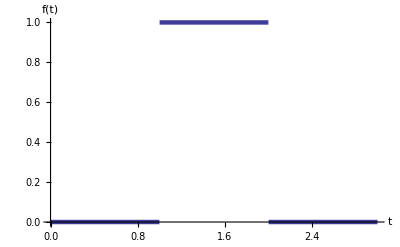

```mathematica
f[t_] = UnitStep[t-1]UnitStep[2-t];
Plot[f[t],{t,0,3},PlotStyle->Thickness[0.008],AxesLabel->{"t","f(t)"}]
```

This signal has the following Fourier transform:

```mathematica
f̃[ω_] = Expand[Integrate[Exp[I ω t],{t,1,2}]]
```

(ⅈ ⅇ^(ⅈ ω))/ω-(ⅈ ⅇ^(2 ⅈ ω))/ω

This Fourier transform has both real and imaginary parts, as shown in Cell 2.45.

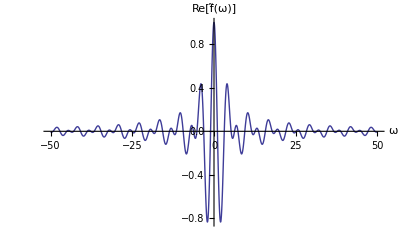

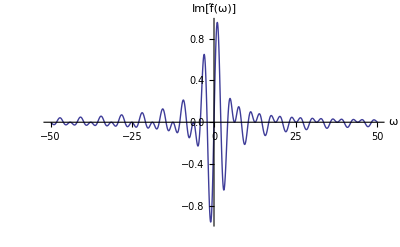

```mathematica
Plot[Re[f̃[ω]],{ω,-50,50},AxesLabel->{"ω","Re[f̃(ω)]"},PlotRange->All]
Plot[Im[f̃[ω]],{ω,-50,50},AxesLabel->{"ω","Im[f̃(ω)]"},PlotRange->All]
```

The real part of the transform f̃(ω) is an even function of ω, and the imaginary part an odd function. This follows from the fact that our function  f(t) was real. In general, for real   f(t),

f̃(-ω)=(f̃(ω))^*.

Also note that the Fourier transform has nonnegligible high-frequency components. This is expected, because the function f(t) has sharp jumps that require high-frequency Fourier modes.

However, the medium carrying the signal is often such that only frequencies within some range Δω can propagate. This range is called the bandwidth  of the medium. If, in our example, frequencies beyond 10 (in our dimensionless units) cannot propagate, then these components are cut out of the spectrum  and the inverse transform of this signal is

```mathematica
Subscript[f, 1][t_] = Integrate[Exp[-I ω t] f̃[ω],{ω,-10,10}]/(2 Pi);
```

This signal looks degraded and broadened due to the loss of the high-frequency components, as shown in Cell 2.47.

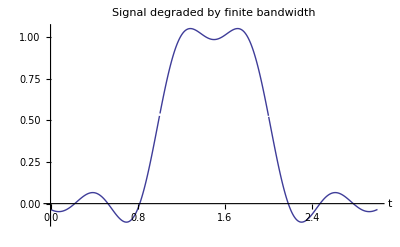

```mathematica
Plot[Re[Subscript[f, 1][t]],{t,0,3},AxesLabel->{"t","  "},PlotPoints->500,PlotLabel->"Signal degraded by finite bandwidth"]
```

If these pulses become so broad that they begin to overlap with neighboring pulses in the signal, then the signal will be garbled. For example, in order to distinguish a 0 bit travelling between two 1 bits, the length in time of each bit, T, must be larger than roughly half the width Δt of the degraded bits: 2T≳Δt (see Fig. 2.6).

Fig. 2.6.: The digital signal consisting of bits 1 0 1, for three different bandwidths Δω. As Δω decreases, the width  Δt of the pulses increases until they begin to overlap, and it is no longer possible to distinguish the bits.

Also, Fig. 2.6 indicates that that there is a connection between the degraded pulse width Δt and the bandwidth Δω: as Δω decreases, Δt increases. In fact, in Sec. 2.3.3 we will show that Δt∝1/Δω: See Eq. (2.3.24). This implies that the minimum time between distinguishable pulses, T_min, is proportional to 1/Δω. The maximum rate ν_max at which pulses can be sent is  ν_max= 1/T_min, so we find that

ν_max∝ Δω .

This important result shows that the maximum number of bits per second that can be sent through a medium is proportional to the bandwidth of the medium. For example, a telephone line has a bandwidth Δω of roughly 4000 Hz, which limits the rate at which digital signals can be sent, as any modem user knows. However, an optical fiber has a bandwidth on the order of the frequency of light, around 10^15Hz, which is why optical fibers can transmit much more information than phone lines. (Actually, the bandwidth quoted above for optical fiber is a "theoretical"  bandwidth, applicable only to short fibers;  in long fibers dispersion begins to limit the effective bandwidth. Dispersion will be discussed in Chapter 5. Also, the bandwidth of the receiver and the transmitter must be taken into account.)

2.3.2 Fourier sine and cosine Transforms

Sometimes one must Fourier-transform a function f(t) that is defined only on a portion of the real line, a≤ t≤ ∞. For such functions, one can extend the definition of f to the range -∞<t<a in any way that one wishes, and then employ the usual transformations of Table 2.1 over the entire real line.

One simple choice is f(t)=0 for t<a. In this case the Fourier transform is

f̃(ω)=∫_a^∞ f(t)ⅇ^(ⅈ ω t)ⅆt,

and the inverse transformation remains unchanged.

For example, we may use Eq. ( 2.3.9) to take the Fourier transform of the function f(t)=exp(-t), t>0. The integration in Eq. (2.3.9) can then be done by hand:

f̃(ω)=∫_0^∞ ⅇ^(ⅈ ω t-t)ⅆt=1/(1-ⅈω).

The inverse transformation should then return us to the original function f(t). Mathematica's intrinsic function can perform this task:

```mathematica
InverseFourierTransform[1/(1-I ω),ω,t]/Sqrt[2 Pi]
```

ⅇ^-t HeavisideTheta[t]

The function HeavisideTheta, also called the Heaviside step function, is defined by Eq. (9.8.1). Since this function is zero for t<0 and unity for t>0, the inverse transform has reproduced f(t), including the extension to t<0.

It is sometimes useful to create an even or odd  extension of the function, rather than setting the function equal to zero for t<a. In this case, the exponential transform is replaced by a Fourier sine or cosine transform.

For an odd extension of the function, we require that f(a-t) = -f(a+t) for any t.The formulae for the Fourier sine transform then follow from a limiting procedure analogous to that done for the exponential transform, but instead applied to the Fourier sine series discussed in Sec. 2.2.3. Now one takes b→ ∞ but leaves a fixed. It is then an exercise to show that the result for the Fourier sine transform and the inverse sine transform is

f̃(ω)=∫_a^∞ f(t)sinω(t-a)ⅆt,
f(t) = ∫_(-∞)^∞ f̃(ω)sinω(t-a)ⅆω/π.

On the other hand, if we wish to use an even function, such that f(a-t) = f(a+t) for any t, we can employ a cosine transform of the form

f̃(ω)=∫_a^∞ f(t)cosω(t-a)ⅆt,
f(t) = ∫_(-∞)^∞ f̃(ω)cosω(t-a)ⅆω/π.

The definitions for spatial sine and cosine transforms are identical, except for the convention of replacing ω by k and t by x.

As an example of a sine transform, we can again take f(t)=exp(-t) for t>0. The sine transform is then given by

```mathematica
Simplify[Integrate[Exp[-t]Sin[ω t],{t,0,Infinity}],Im[ω]==0]
```

ω/(1+ω^2)

The inverse sine transform is

```mathematica
Simplify[Integrate[%Sin[ω t],{ω,-Infinity,Infinity}]/Pi,Im[t]==0]
```

(ⅇ^(-Abs[t]) t)/Abs[t]

which returns us to f(t), but with an odd extension into the range t<0.   For an even extension of the same function, the cosine transform is

```mathematica
Simplify[Integrate[Exp[-t]Cos[ω t],{t,0,Infinity}],Im[ω]==0]
```

1/(1+ω^2)

and the inverse cosine transform returns the correct even function:

```mathematica
Simplify[Integrate[%Cos[ ω t],{ω,-Infinity,Infinity}]/Pi,Im[t]==0]
```

ⅇ^(-Abs[t])

2.3.3 Some Properties of Fourier Transforms

## Fourier Transforms as Linear Integral Operators

When one takes the Fourier transform of a function f(t), the result is a new function f̃(ω). This is reminiscent of the manner in which a linear differential operator L̂ transforms a function f to a different function  L̂ f by taking derivatives of f. In fact,  a Fourier transform can also be thought of as a linear operator F̂, defined by its operation on a given function f:

F̂ f=∫_(-∞)^∞ ⅇ^(ⅈ ω t)f(t) ⅆt.

The result of the operation of F̂ on a function f is a new function f̃, that is,

F̂ f=f̃.

The operator   F̂= ∫_(-∞)^∞ ⅇ^(ⅈ ω t) ⅆt is a linear operator, since it satisfies F̂(C f+g)=C F̂ f+F̂ g for any functions f and g and any constant C. However, this linear operator is an integral operator rather than a differential operator.

The inverse  Fourier transform can also be thought of as  an operator, (F̂)^-1. This operator is defined by its action on a function f̃(ω), producing a function f(t) according to

f= (F̂)^-1 f̃=∫_(-∞)^∞ ⅇ^(-ⅈ ω t)f̃(ω) ⅆω/2π.

The inverse transform has the property required of any inverse: for a  given function f,

(F̂)^-1 F̂ f=F̂(F̂)^-1 f=f.

This follows directly from the definition of the inverse Fourier transform. However, certain smoothness and integrability requirements on f  for this identity to hold should be mentioned: first, the required integrals must exist, of course. Integrable singularities and even certain types of nonintegrable singularities can be handled, but sufficiently singular functions do not have well-defined transforms.  Also, functions with point discontinuities are smoothed by the process of taking the transform and the inverse transform. That is, take any finite function f and change it at one point to a new (finite) value. This clearly has no effect on the Fourier transform of the function; hence, for such functions, the application of the transform and the inverse transform removes such point discontinuities. At at such points Eq. (2.3.15) breaks down. Also, it is not difficult to show that for a piecewise-continuous function with a discontinuity at t=a  the value of  (F̂)^-1 F̂ f at  a is the average of f across the discontinuity, ie.  (f(a^+)+f(a^-))/2.  Thus,

the identity
				f=(F̂)^-1 F̂ f
applies to functions whose Fourier transforms exist, such as integrable functions on the real line or to the types of nonintegrable functions that appear in generalized Fourier integrals (see Sec. 2.3.4);  that are piecewise continuous, and whose value at each point of discontinuity a is given by (f(a^+)+f(a^-))/2.

## Fourier Transforms of Derivatives and Integrals

The Fourier transform of the derivative of a function is related to the Fourier transform of the function itself. Consider

F̂ ⅆf/ⅆt=∫_(-∞)^∞ ⅇ^(ⅈ ω t)ⅆf/ⅆt ⅆt.

An integration by parts, together with the assumption that f(±∞)=0 (required for the convergence of the Fourier integral) implies

F̂ ⅆf/ⅆt=-∫_(-∞)^∞ f(t) ⅆ/ⅆt ⅇ^(ⅈ ω t)ⅆt=-ⅈω∫_(-∞)^∞ f(t) ⅇ^(ⅈ ω t)ⅆt=-ⅈωf̃(ω),

where f̃=F̂ fis the Fourier transform of f. 
	We can immediately generalize Eq. (2.3.17) to the transform of derivatives of any order:

F̂ ⅆ^n f/ⅆ t^n=(-ⅈω)^n f̃(ω).

This simple result is of great importance in the analysis of particular solutions to linear differential equations with constant coefficients, as we will see in Sec. 2.3.6.

Also, it follows from Eq. (2.3.17) that the Fourier transform of the indefinite integral of a function (assuming this integral  vanishes at positive and negative infinity) is given by

F̂∫^t f(t)ⅆt=f̃(ω)/(-ⅈω).

## Convolution Theorem

The convolution h(t) of two functions, f(t) and g(t), is defined by the following integral:

h(t) = ∫_(-∞)^∞ f(t_1)g(t-t_1)ⅆ t_1=∫_(-∞)^∞ f(t-t_2)g(t_2)ⅆ t_2.

Either integral is a valid form for the convolution. The second form follows from a change of the integration variable from t_1to t_2= t-t_1 .

Convolutions often appear in the physical sciences, as when we deal with Green's functions [see Eq. (2.3.73) ]. The convolution theorem is a simple relation between the Fourier transforms of h(t), f(t) and g(t):

h̃(ω)=f̃(ω)g̃(ω).

To prove this result, we take the Fourier transform of h(t):
		h̃(ω)=∫_(-∞)^∞ ⅆt ⅇ^(ⅈ ω t)∫_(-∞)^∞ f(t_1)g(t-t_1)ⅆ t_1.

Changing the integration variable in the t-integral to t_2= t-t_1yields

h̃(ω)=∫_(-∞)^∞ ⅆ t_2 ∫_(-∞)^∞ ⅇ^(ⅈ ω( t_2+t_1))f(t_1)g(t_2)ⅆ t_1.
In this change of variables from t to t_2, t_1is held fixed, so ⅆt=ⅆ t_2 and the range of integration still runs from -∞ to +∞.We can now break the exponential into a product of exponentials, ⅇ^(ⅈ ω( t_2+t_1))=ⅇ^(ⅈ ω t_2)ⅇ^(ⅈ ω t_1), and break the two integrals up into a product of Fourier transforms:
		h̃(ω)=∫_(-∞)^∞ ⅆ t_2 ⅇ^(ⅈ ω t_2)g(t_2)∫_(-∞)^∞ ⅇ^(ⅈ ω t_1)f(t_1)ⅆ t_1=g̃(ω)f̃(ω),

proving the theorem.

## The Uncertainty Principle of Fourier Analysis

Consider a dimensionless function  f(τ) that approaches zero when |τ|≳1. An example of such a function is exp(-|τ|); another is 1/(1 + τ^2). A third example is the set of data bits plotted in Fig. 2.6 . The Fourier transform of this function, f̃(ω), will typically approach zero for large |ω|, because only frequencies up to some value are necessary to describe the function. Let us define the width of this transform function as Δ, that is, f̃(ω)→ 0 for |ω|≳Δ. (Here Δ is a dimensionless number,  on the order of unity for the three examples given above.)

Now consider a scale transformation of τ to a new time t=Δt τ. When written in terms of the new time, the function f(τ) becomes a new function g(t), defined by g(t) =f(t/Δt) . This function approaches zero for times |t|> Δt. Therefore,  Δt is a measure of the width in time of the function g(t).

An example of the function g(t) is shown in Fig. 2.7  for different choices of Δt, taking f(τ)=exp(-τ^2) . As Δt increases, the width of g increases. One can see that varying Δt defines a class of functions, all of the same shape, but with different widths.

Now consider the Fourier transform of  g(t):

g̃(ω)=∫_(-∞)^∞ ⅆt ⅇ^(ⅈ ω t)f(t/Δt).

We will now relate the width Δω of the Fourier transform g̃ to the width Δt of g. This relation follows from a simple change of the integration variable in Eq. (2.3.22)  back to τ=t/Δt:

g̃(ω)=Δt ∫_(-∞)^∞ ⅆτ ⅇ^(ⅈ ω Δt  τ)f(τ)=Δt f̃(ω Δt).

Now, since the width of  f̃ is Δ, Eq. (2.3.23) shows that the width Δω of g̃ is Δω=Δ/Δt, or in other words,

Δω Δt = constant,

where the constant Δ is a dimensionless number. This constant differs for different functions. However, if one defines the width of a function in a particular way,  as the rms width [see Exercise (13)], then one can show that Δ≥ 1/2, with equality for Gaussian  functions of the form f(t) = f_o ⅇ^(-a t^2).

Equation (2.3.24), along with the condition Δ≥ 1/2, is the uncertainty principle of Fourier analysis. It is called an uncertainty principle because it is the mathematical principle at the heart of Heisenberg's uncertainty principle in quantum mechanics. It shows that as a function becomes wider in time, its Fourier transform becomes narrower.  This is sensible, because wider functions vary more slowly, and so require fewer Fourier modes to describe their variation.  Alternatively, we see that very narrow, sharply peaked functions of time require a  broad spectrum of Fourier modes in order to describe their variation.

As an example of the uncertainty principle, consider the Fourier transform of the function g(t) = exp[-(t/Δt)^2]. This function is plotted in Fig. 2.7 The Fourier transform is

```mathematica
FourierTransform[Exp[-(t/Δt)^2],t,ω] Sqrt[2 Pi]
```

ⅇ^(-1/4 Δt^2 ω^2) √π √(Δt^2)

This function is plotted in Fig. 2.8 for the same values of Δt as those in Fig. 2.7. One can see that as Δt increases, the transform function narrows.

Fig. 2.7 The function g(t)=ⅇ^(-(t/Δt)^2) for three choices of Δt.

Fig. 2.8 The Fourier transform of g.

An important application of the uncertainty principle is related to the data bit function of width Δt, plotted in Cell 2.43. We saw there that when a finite bandwidth Δω cuts off the Fourier spectrum of a signal pulse, the width of the pulse in time, Δt, grows larger (see Fig. 2.6). We now see that this is a consequence of the uncertainty principle. This principle says that as the bandwidth Δω of a medium decreases, the signal pulses must become broader in time according to Eq. (2.3.24),  and hence the distance in time between pulses must be increased in order for the pulses to be distinguishable.

In turn, this implies that the maximum rate ν_max at which signals can be propagated is proportional to the bandwidth of the medium: see Eq. (2.3.8).

2.3.4 The Dirac δ-Function and Generalized Fourier Integrals

## Introduction

The function g(t)=f(t/Δt) plotted in Fig. 2.7 increases in width as Δt increases . The area under the function also clearly increases with increasing Δt.  One might expect that the area under the Fourier transform of g(t) should decrease as the transform becomes narrower: see Fig. 2.8. However, we will now show that the area under  g̃(ω) is actually independent of Δt. 
	This surprising result follows from the following property of the inverse transform:

g(t=0)=∫_(-∞)^∞ g̃(ω)ⅇ^(-ⅈ ω 0)ⅆω/2 π=∫_(-∞)^∞ g̃(ω)ⅆω/2 π.

The area under g̃(ω) equals 2 π g(0)=2π f(0), independent of of Δt.
	Why is this important?  Consider the limit as Δt→ ∞.  In this limit, the width of g̃(ω) vanishes, but the area under the function remains constant, equaling 2 π f(0). One can see from Fig. 2.8 that this can happen because the height of g̃(ω) approaches infinity as the width vanishes.

This strange curve is called a Dirac δ-function δ(ω). To be precise,

δ(ω) = lim_(Δt→ ∞) g̃(ω) /(2 π g(0)).

This function is normalized so as to have unit area under the curve. However, since its width is vanishingly small,  the function also has the properties that

δ(ω)={0,  ω≠0,
∞,  ω= 0.

Therefore, the area integral need not involve the entire real line, because the δ-function is zero everywhere except at the origin. The integral over δ(ω) equals unity for any range of integration that includes the origin, no matter how small:

lim_(ϵ→ 0) ∫_-ϵ^ϵ δ(ω)ⅆω=1.

Dirac δ-functions often appear in the physical sciences. These functions have many useful properties, which are detailed in the following sections.

## Integral of a δ-Function

Equations (2.3.27) and (2.3.28) lead to the following useful result: for any function h(t) that is continuous at t=0, the following integral can be evaluated analytically:

∫_-a^b h(t)δ(t)ⅆt=lim_(ϵ→ 0) ∫_-ϵ^ϵ h(t)δ(t)ⅆt=h(0)lim_(ϵ→ 0) ∫_-ϵ^ϵ δ(t)ⅆt=h(0).

In the first step, we used the fact that δ(t) equals zero everywhere except at t=0 in order to shrink the range of integration down to an infinitesimal range that includes the origin. Next, we used the assumption that h(t) is continuous at t=0, and finally, we employed Eq. (2.3.28).

## δ-Functions of More Complicated Arguments

We will often have occasion to consider integrals over Dirac δ-functions of the form

∫_a^b g(t) δ(f(t))ⅆt,

where f(t) equals zero at one or more values of t in the interval a<t<b. Take, for example, the case f(t) = c t , for some constant c, with a<0<b. The integration in Eq. (2.3.30) can then by performed by making a change of variables: let u = c t.  Then Eq. (2.3.30) becomes 1/c∫_(c a)^(c b) g(u/c) δ(u)ⅆt.

Now, if c>0 the result according to Eq.(2.3.29)  is g(0)/c, but if c<0, the result is -g(0)/c, because the range of integration is from a positive quantity c a to a negative quantity, c b. Therefore, we find

∫_a^b g(t) δ(c t)ⅆt = g(0)/|c|, assuming a<0<b.

Equation (2.3.31) can used to determine more general integrals of the form of Eq. (2.3.31). Lets assume that f(t) passes through zero at M points in the range a<t<b, and let us label these points t = t_n, n=1,2,3,...,M.  The integral can then be broken up into contributions from each one of these zeros:

∫_a^b g(t) δ(f(t))ⅆt=∑_(n=1)^M ∫_(t_n-ϵ)^(t_n+ϵ) g(t) δ(f(t))ⅆt.

Other regions of integration do not contribute, because the δ-function is only nonzero within the regions kept. Focussing on one of the zeros, t = t_n, we note that only values of values of t near  t_n are needed, and so we make a change of variables from tto Δt =t- t_n:

∫_(t_n-ϵ)^(t_n+ϵ) g(t) δ(f(t))ⅆt=∫_-ϵ^ϵ g(t_n+Δt) δ(f(t_n+Δt))ⅆΔt.
Taylor-expanding f(t)  for small Δt, noting that f(t_n)=0, and assuming that f'(t_n)≠ 0,we have

∫_(t_n-ϵ)^(t_n+ϵ) g(t) δ(f(t))ⅆt=∫_-ϵ^ϵ g(t_n+Δt) δ(f'(t_n)Δt)ⅆΔt=g(t_n)/|f'(t_n)|,

where we used Eq.(2.3.31) in the last step. Therefore. Eq. (2.3.32) becomes

∫_a^b g(t) δ(f(t))ⅆt=∑_(n=1)^M g(t_n)/|f'(t_n)|.

## Generalized Fourier Integrals

The previous considerations lead us to a startling observation. Consider the Fourier transform of δ(t) itself:

∫_(-∞)^∞ δ(t) ⅇ^(ⅈ ω t)ⅆt=ⅇ^(ⅈ ω0)=1,

where we have used Eq. (2.3.29). This result, that the Fourier transform of δ(t) equals one, is expected on one level: after all,  since δ(t) is infinitely narrow, the uncertainty principle implies its transform must be infinitely broad.

However, if we write down the inverse Fourier transform of unity, which should return us to δ(t), we arrive at the strange result

δ(t)=∫_(-∞)^∞ 1 ⅇ^(-ⅈ ω t)ⅆω/2π.

This integral is not convergent; the integrand does not decay to zero at large ω. But, somehow, it equals a δ-function!

We can try to understand this strange result by writing the inverse transform as
		δ(t)=lim_(Δω→∞) ∫_-Δω^Δω 1 ⅇ^(-ⅈ ω t)ⅆω/2π.

This integral can be evaluated analytically. The result is

δ(t) =lim_(Δω→∞) (sin(Δω t))/(π t) .

For a fixed value of t, and as Δω increases, the function sin(Δω t)/π t  simply oscillates between the values ±1/π t. Since this oscillation continues indefinitely as  Δω→∞, the limit is not well defined.  How can  this limit equal a δ-function?

The limit equals a δ-function in the following average sense. Consider an integral over this function multiplied by any continuous function f(t):

lim_(Δω→∞) ∫_-a^b f(t)(sin(Δω t))/(π t)ⅆt.

If we now make the change of variables to τ = Δω t, the integral becomes

lim_(Δω→∞) ∫_(-Δω a)^(Δω b) f(τ/Δω) sinτ/(π τ)ⅆτ.

However,  the function sinτ/(π τ) is peaked at the origin, with an area under the curve equal to unity:

∫_(-∞)^∞ sinτ/(π τ)ⅆt=1.

Since this integral is convergent, we can replace the limits of integration in Eq. (2.3.38) by ±∞. Furthermore, in the limit that Δω→∞, we can replace f(τ/Δω)→ f(0).

Therefore,using Eq. (2.3.39) we find that

lim_(Δω→∞) ∫_-a^b (sin(Δω t))/(π t)f(t) ⅆt = f(0),

Thus, the function lim_(Δω→∞) (sin(Δω t))/(π t)has the most important property of a δ function: it satisfies Eq. (2.3.29). If we take f(t) = 1, we can immediately see that the function also satisfies Eq. (2.3.28).  On the other hand, it does not satisfy Eq. (2.3.27): it is not equal to zero for t≠0; rather it is undefined, oscillating rapidly between ±1/π t. Actually, rapidly is an understatement. In the limit as Δω→ ∞, the oscillations in the function become infinitely rapid. Fortunately, the nature of this variation allows us to call this function a δ-function. When evaluating an integral with respect to t over this function, the oscillations average to zero unless the origin is included in the range of integration. This can be seen in Cell 2.54, which displays the behavior of this function over a range of t as Δω increases.

```mathematica
ListAnimate[Table[Plot[Sin[Δω t]/(Pi t),{t,1,2},PlotRange->{-1,1}],{Δω,10,100,10}]]
```

This sequence of plots shows that, if the origin is not included in the plots, the amplitude of the oscillations in [sin(Δω t)]/(π t) does not change as Δω increases; only the frequency increases until in the limit the function is zero on average. (Try changing the limits of the plot, and the range of Δω,  to test this.)

However, if the origin is included, the amplitude of the peak at t=0 increases as Δω becomes larger, since by l'Hospital's rule, lim_(t→0) Sin[Δω t]/(π t)=Δω/π. This is what allows the area under the function to remain unity in the limit as Δω becomes large.

Thus, Eq. (2.3.35) is a δ-function in an average sense: integrals over this function have the correct property given by Eq. (2.3.29). However, the function itself contains infinitely rapid oscillations.

Fourier integrals such as Eq.  (2.3.35) are called generalized  Fourier integrals: they do not converge in the usual sense of the term. Rather, the resulting functions contain infinitely rapid oscillations. We neglect these oscillations because all we use in applications are integrals over these functions, which average out the oscillations.

## Derivatives of a δ-Function

Several other generalized Fourier integrals are also of use.  Consider, for example, the derivative of a δ-function, δ'(t)=ⅆδ(t)/ⅆt. According to Eq. (2.3.35), this derivative can be written as a generalized Fourier integral,

δ'(t)=(ⅆ/ⅆt) ∫_(-∞)^∞ ⅇ^(-ⅈ ω t)ⅆω/2π= ∫_(-∞)^∞ (-ⅈ ω) ⅇ^(-ⅈ ω t)ⅆω/2π.

The integrand in the second integral in Eq. (2.3.41) exhibits even worse convergence properties than Eq. (2.3.35)!  The resulting function of time has infinitely rapid oscillations of infinite magnitude.  Nevertheless, integrals over this function are well behaved. We therefore may say, with a straight face, that the Fourier transform of a δ'(t) is -ⅈ ω, and compute the inverse transform of this function. In fact, Mathematica's FourierTransform  function knows all about generalized Fourier integrals. For instance,

```mathematica
InverseFourierTransform[1,ω,t]/Sqrt[2 Pi]
```

DiracDelta[t]

The intrinsic function DiracDelta[t] is the Dirac δ-function.  Also,

```mathematica
InverseFourierTransform[-I ω,ω,t]/Sqrt[2 Pi]
```

DiracDelta'[t]

Of course, we can't plot these functions, because they are singular, but we know what they look like. The δ-function has a single positive spike at the origin. Since δ'(t) is the slope of δ(t), it has a positive spike just to the left of zero, and a negative spike just to the right.

The derivative of a δ-function has a useful property: for any function f(t) that is differentiable at t=0, the following integral that includes the origin can be evaluated analytically via an integration by parts:

∫_-a^b f(t)δ'(t)ⅆt=-∫_-a^b f'(t)δ(t)ⅆt=-f'(0).

Similarly, the nth derivative of a δ-function has the property that

∫_-a^b f(t)(ⅆ^n δ(t))/(ⅆ t^n)ⅆt=(-1)^n(ⅆ^n f)/(ⅆ t^n)(0).

The Fourier integral representation of (ⅆ^n δ(t))/(ⅆ t^n) becomes progressively less convergent as n increases:

(ⅆ^n δ(t))/(ⅆ t^n)=∫_(-∞)^∞ (-ⅈ ω)^n ⅇ^(-ⅈ ω t)ⅆω/2π

These generalized Fourier integrals allow us to do things that we couldn't do before.  For instance, we can now compute the value of a nonconvergent integral, such as 
		∫_(-∞)^∞ t^2/(1+t^2)cosω tⅆt.

Normally, we would throw up our hands and declare that the integral does not exist. This is technically correct so far as it goes, but we still can compute its value as a generalized Fourier integral:

∫_(-∞)^∞ t^2/(1+t^2)cosω tⅆt=Re ∫_(-∞)^∞ (1+t^2-1)/(1+t^2)ⅇ^(ⅈ ω t)ⅆt =Re ∫_(-∞)^∞ ⅇ^(ⅈ ω t)ⅆt -Re ∫_(-∞)^∞ 1/(1+t^2)  ⅇ^(ⅈ ω t)ⅆt .

The first integral is proportional to a δ-function, while the second integral is convergent, equaling -π ⅇ^(-|ω|). Thus, we obtain
		∫_(-∞)^∞ t^2/(1+t^2)cosω tⅆt=2πδ(ω)+π ⅇ^(-|ω|).

However, we must always remember that the equality is correct only in the average sense discussed above; the right-hand side neglects infinitely rapid oscillations.

## Heaviside Step Function

Before we move on to other topics, there is one more generalized Fourier integral of interest. Consider the integral  of a δ-function,

h(t)=∫_(-∞)^t δ(t_1)ⅆ t_1.

This function equals zero if t<0, but for t>0 the range of integration includes the origin, and then according to Eq. (2.3.28), h(t) = 1. Therefore, h(t) is nothing other than the Heaviside step function UnitStep[t], encountered previously [Eq. (9.8.1) and Cell 2.48]. For convenience, we reproduce the definition of  h(t) below:

h(t) = {0,t<0,
1,t> 0.

Actually,  UnitStep is not quite the same as the Heaviside step function defined by Eq. (2.3.45) since this integral has an undefined value fot t=0,  but UnitStep[0]=1.  The integral in Eq. (2.3.45) yields a slightly different function, HeavisideTheta[t], whose value is undefined at t=0.  According to Eq. (2.3.45), h'(t) = δ(t).  Mathematica recognizes this fact for HeavisideTheta, but not for UnitStep .
	We can find the Fourier integral of h(t) by directly applying the transform:
		h̃(ω)=∫_(-∞)^∞ ⅇ^(ⅈ ω t)h(t)ⅆt=∫_0^∞ ⅇ^(ⅈ ω t)ⅆt.

Now, this is not a convergent integral; rather, it is a generalized Fourier integral, and it provides an instructive example of some of the methods used to evaluate such integrals.

Breaking the integrand into real and imaginary parts via ⅇ^(ⅈ ω t)= cosω t + ⅈ sin ω t, we can write the result as

h̃(ω)=∫_0^∞ cosω tⅆt+ⅈ∫_0^∞ sin ω tⅆt.

In the first integral, note that cosωt is an even function of t, so we can double the range of integration to -∞<t<∞, and divide by 
1/2. Expressing the second integral as a limit, we can write

h̃(ω)=1/2 Re∫_(-∞)^∞ ⅇ^(ⅈ ω t)ⅆt+ⅈ  lim_(Δt→∞) ∫_0^Δt sin ω tⅆt .

The first integral yields a δ-function via Eq. (2.3.34), and the second integral can be evaluated analytically:

h̃(ω)=π δ(ω)-1/(ⅈ ω)+ lim_(Δt→∞) (cos (ω Δt))/ⅈω.

As usual, we neglect the infinite oscillations. Mathematica can also derive the same result:

```mathematica
Expand[FourierTransform[HeavisideTheta[t],t,ω]Sqrt[2 Pi]]
```

ⅈ/ω+π DiracDelta[ω]

There is a new oddity in this expression: the first term in the function h̃(ω) , ⅈ/ω,  has a non-integrable divergence at ω=0. Nevertheless, it must be the case that ∫_(-∞)^∞ ⅇ^(-ⅈ ω t)h̃(ω)ⅆω/(2π)=h(t). We can understand how this is so by including the rapidly-oscillatory term in Eq. (2.3.47):

∫_(-∞)^∞ ⅇ^(-ⅈ ω t)h̃(ω)ⅆω/(2π)=∫_(-∞)^∞ ⅇ^(-ⅈ ω t)[π δ(ω)-1/(ⅈ ω)+ lim_(Δt→∞) (cos (ω Δt))/ⅈω]ⅆω/(2π).

The δ-function term can be integrated easily, yielding 1/2; and the sum of the last two terms in the square bracket is not singular at ω=0, so the integral now converges.   However, note that these  two terms are odd in ω, so we may replace ⅇ^(-ⅈ ω t) by -ⅈ sin ω t to obtain the convergent form

∫_(-∞)^∞ ⅇ^(-ⅈ ω t)h̃(ω)ⅆω/(2π)=1/2 +∫_(-∞)^∞ sin(ω t)[1/ω- lim_(Δt→∞) (cos (ω Δt))/ω]ⅆω/(2π).

The last term in the square bracket can now be dropped, since the integrand converges with or without this term and it oscillates infinitely rapidly, so the term integrates to zero. The integral of sin (ω t)/ω equals π Sign(t) (see Eq. (2.3.39) ). Therefore, the integral yields

∫_(-∞)^∞ ⅇ^(-ⅈ ω t)h̃(ω)ⅆω/(2π)=1/2 + Sign(t)/2=h(t) ,

the expected result,  with the caveat that it matches Eq. (2.3.46) but is not undefined at t=0 ; rather, the value there is 1/2. This is expected as well from the averaging properties of the Fourier transform across discontinuities [see the discussion following Eq.  (2.3.15) ].

Also, note that inclusion of the rapidly-oscillating  cos (ω Δt) term had no effect on the inverse transform since we ultimately dropped it. We kept it only to make the integrand convergent at ω=0.  More generally, singular Fourier integrals of the form ∫_(-∞)^∞ ⅆω ⅇ^(-ⅈ ω t)/ω^n can also be performed using similar arguments. One replaces 1/ω^n by the n-1st derivative of (-1)^(n-1)(1- lim_(Δt→∞) cos (ω Δt))/ω , which is convergent at ω=0. The integrals can then be performed, and the limit taken afterward.  Some examples will be considered in the Exercises.

## Connection of Fourier Transforms to Fourier Series

Since Fourier transforms can be used to represent any function as an integral over Fourier modes, they can be used to represent periodic functions as a special case. It is a useful exercise to see how this representation connects back to Fourier series.

As a first step, we will consider the Fourier series for a simple periodic function, the periodic δ-function of period T, δ^(P)(t). This function is a periodic extension of a Dirac δ-function, and can be written as

δ^(P)(t)=∑_(m=-∞)^∞ δ(t-m T).

Since this is a periodic function, it has a Fourier series representation of the form

δ^(P)(t)=∑_(n=-∞)^∞ c_n ⅇ^(-ι 2π n t/T).

The Fourier coefficients are given by an integral over one period of δ^(P)(t), which contains a single δ-function :
		c_n=∫_(-T/2)^(T/2) δ(t) ⅇ^(ⅈ 2 π n t/T)ⅆt=1.

Thus, the periodic δ-function of period T has a Fourier series of the form

δ^(P)(t)=∑_(m=-∞)^∞ δ(t-m T)=∑_(n=-∞)^∞ ⅇ^(-ι 2π n t/T).

It is easy to see why Eq. (2.3.49) is a periodic δ-function. If t= m T for any integer m, then ⅇ^(-ι 2π n t/T)=ⅇ^(-ι 2π n m)=1 for all n, and the series sums to ∞ . At these instants of time, each Fourier mode is in phase. However, if t≠  m T, the sum over ⅇ^(-ι 2π n t/T) evaluates to a series of complex numbers, each with magnitude of unity, but with different phases. Adding together these complex numbers, there is  destructive interference between the modes, causing the sum to equal zero. Thus, we get a function that is infinite for t= m T, and zero for t≠  m T.

However, the easiest way to see that this series creates a periodic δ-function is to examine the series as a function of time using Mathematica. The following evaluation creates a periodic δ-function by keeping 300 terms in the Fourier series of Eq. (2.3.49). We choose a period of 1/5 s, and note that the sum over n can be written in terms of cosines since the sine functions are odd in n and  cancel:

```mathematica
1 + 2Sum[ Cos[2 Pi n 5 t],{n,1,300}];
```

We could plot this function, but it is more fun to Play it (Cell 2.59).

```mathematica
Play[%,{t,-1.5,.5},PlayRange->All]
```

-Graphics-

It is necessary to keep several hundred terms in the series, because our ears can pick up frequencies of up to several thousand hertz. Since the fundamental frequency is 5 Hz, keeping 300 terms in the series keeps frequencies up to 1500 Hz. It would be even better to keep more terms; the sound of the "pops" then becomes higher pitched. However, keeping more terms makes the evaluation of the series rather slow.

The periodic δ-function is useful in understanding the connection between Fourier transforms and Fourier series. Consider an arbitrary periodic function f(t) with period T. This function has a Fourier transform f̃(ω), given by

f̃(ω)=∫_(-∞)^∞ f(t)ⅇ^(ⅈ ω t)ⅆt.
Using the periodic nature of f(t), we can break the Fourier integral into a sum over separate periods:

f̃(ω)=∑_(n=-∞)^∞ ∫_(t_o-n T)^(t_o-n T + T) f(t)ⅇ^(ⅈ ω t)ⅆt,
where t_o is an arbitrary time. Now we may change variables in the integral to t_1=t+n T, and use Eq. (2.1.1) to obtain

f̃(ω)=∑_(n=-∞)^∞ ⅇ^(ⅈ ω n T)∫_t_o^(t_o + T) f(t_1)ⅇ^(ⅈ ω t_1)ⅆ t_1.

However, Eq. (2.3.49) implies that ∑_(n=-∞)^∞ ⅇ^(ⅈ ω n T)=δ^(P)(ω T^2/2 π). Then Eq. (2.3.50) becomes

f̃(ω)=∑_(m=-∞)^∞ δ((ω  T^2)/(2 π)-m T)∫_t_o^(t_o + T) f(t_1)ⅇ^(ⅈ ω t_1)ⅆ t_1=∑_(m=-∞)^∞ 2 π δ(ω-(2 π m)/T)1/T∫_t_o^(t_o + T) f(t_1)ⅇ^(ⅈ ω t_1)ⅆ t_1,

where we have used Eqs. (2.3.48) and (2.3.33). Furthermore, note that the integral in Eq. (2.3.51) is the expression for the mth Fourier coefficient, c_m, Eq. (2.1.33). Therefore, we can write

f̃(ω)=∑_(m=-∞)^∞ 2 π δ(ω-(2 π m)/T)c_m.

This equation connects the Fourier integral of a periodic function  f(t) to the function's exponential Fourier coefficients c_m. We see that in frequency space a periodic function consists of a sum of δ functions at all harmonics of the fundamental frequency Δω=2 π/T.

Finally, applying the inverse transform to Eq. (2.3.52), the integral over each δ-function in the sum can be evaluated, and we return to our previous expression for f(t) as a Fourier series:

f(t)=∑_(m=-∞)^∞ c_m ⅇ^(- ⅈ m Δω t).

2.3.5 Fast Fourier Transforms

## Discrete Fourier Transforms

In this section we consider methods for performing numerical Fourier transforms. The idea is that one is given a set of data { f_n} measured at N evenly spaced discrete times t_n= n Δt, n=0,1,2,...,N-1. From this data, one wishes to determine a numerical frequency spectrum.

This sort of problem arises in experimental physics as well as in numerical simulation methods, and in many other fields of science, including  economics, engineering, signal processing, and acoustics.

One way to attack this problem is simply to discretize the integrals in the Fourier transform and the inverse transform.  If we consider a discretized version of a Fourier transform, Eq. (2.3.12), with the time variable replaced by closely spaced discrete timesteps t_n=n Δt, and the frequency replaced by closely spaced discrete frequencies ω_m= m Δω, one can immediately see that the operation of Fourier transformation,  F̂ f, is equivalent to the dot product of a vector with a matrix:

f̃(ω)=F̂ f(t)→(f̃)_m=∑_(n=-∞)^∞ F_(m n)f_n

where f_n =f(n Δt) and (f̃)_m =f̃(m Δω), and the matrix F_(m n) has components

F_(m n)=Δt ⅇ^(ⅈ m  n Δt Δω) .

This matrix  is a discretized form of the Fourier transform operator F̂. Equation (2.3.54) shows directly that there is an analogy between the linear integral operator F̂ acting on functions and a matrix F acting on vectors.  Previously, we saw that there was a similar analogy between linear differential operators and matrices.

When the inverse transform operator (F̂)^-1is discretized, it  also becomes a matrix, with components

(F^-1)_(m n)=Δω  ⅇ^(-ⅈ m  n Δt Δω)/2π.

This matrix can be applied to discretized functions of frequency f̃ in order to reconstruct the corresponding discretized function of time, according to the matrix equation

F^-1·f̃=f.

So, in order to take a numerical Fourier transform of a data set { f_n},  it appears that all we need do is apply the matrix F to  the vector f with components f_n, according to Eq. (2.3.53). To turn the resulting discretized spectral function f̃ back into the time data, all we need do is apply the matrix  F^-1, defined by Eq. (2.3.55).

This is fine so far as it goes, but there are several problems hiding in this procedure. First, the matrices F and F^-1 are formally infinite-dimensional.  We can try to get around this problem by cutting off the Fourier integrals.  Since the data runs from 0≤ t≤ (N-1) Δt,   we can cut off the time integral in the Fourier transform beyond this range of times. For the frequency integral in the inverse transform, we can also impose a frequency cutoff, keeping only frequencies in the range -M Δω≤ ω≤ M Δω for some large integer value of M. The hope is that the frequency spectrum goes to zero for sufficiently large ω, so that this cutoff does not neglect anything important.

There is a second problem: although Δt is determined by the dataset, what should our choice for Δω be? Apparently we can choose anything we want,  so long as Δω is "small". This is technically correct - if Δω is small  compared to the scale of variation of the frequency spectrum, then the discretized integral in the Fourier transform is well represented by the Riemann sum  given by Eq. (2.3.56).  However, we also must keep enough terms so that M Δω is a large frequency - large enough to encompass the bulk of the frequency spectrum.

For very smooth time data with only low-frequency spectral components,  this prescription works (see the exercises). However, for real data, which may have high-frequency spectral components and rapid variation in the spectrum, the above method becomes impractical, because we must take M very large. Also, the matrices F^-1 and F  are only approximately the inverses of one another, because of the errors introduced by discretizing the Fourier and inverse Fourier integrals.

One way to improve matters is to recognize that the time data, extending only over a finite time range 0≤ t≤ (N -1) Δt, can be replaced by a periodic extension with period T=N Δt. We take this time as the period (rather than, say, (N-1) Δt) so that the first data point beyond this interval, at time N Δt,  has value f_o. This way, the data can be seen to repeat with period T=N Δt (see Fig. 2.9).

Fig. 2.9  A dataset with 10 elements, periodically replicated.

Since the periodic extension has period T, the data can be represented by a Fourier series rather than a transform, with a fundamental frequency Δω=2 π/T. This is the smallest frequency that can be represented by this data, and so is a good choice for our frequency discretization. Hearkening back to our equation for Fourier series, Eq. (2.2.2), we would like to write

f^(p)(t)=∑_(m=-∞)^∞ (f̃)_m ⅇ^(-ⅈ m Δω t),

where f^(p)(t) is a periodic function of time that represents the discrete data (we will see what this function of continuous time looks like in a moment), and the (f̃)_m 's are the Fourier coefficients in the series. As in all Fourier series, the sum runs over all integers, and of course this is a problem in numerical applications. However, we will see momentarily that this problem can be solved in a natural way.

The Fourier components (f̃)_m are determined by the integral:

(f̃)_m=1/(N Δt)∫_0^(N Δt) f(t)ⅇ^(ⅈ m Δω t)ⅆt,

[see Eq. (2.2.3)]. However, since the time data is discrete, we replace this integral by the Riemann sum, just as in Eq. (2.3.53):

(f̃)_m=1/(N Δt)∑_(n=0)^(N-1) Δt f_n ⅇ^(ⅈ m Δω n Δt)=1/N∑_(n=0)^(N-1) f_n ⅇ^(ⅈ 2π m n /N),

where in the second step we have used Δω=2π/T.

These Fourier components have an important property: they are themselves periodic, satisfying (f̃)_(m+N)=(f̃)_m. The proof is simple:

(f̃)_(m+N)=1/N∑_(n=0)^(N-1) f_n ⅇ^(ⅈ 2π (m+N) n /N)=1/N∑_(n=0)^(N-1) f_n ⅇ^(ⅈ 2π m n /N+ⅈ 2π n)=(f̃)_m.

Now, since (f̃)_m repeats periodically, we can rewrite the infinite sum over these (f̃)_m's in Eq. (2.3.57) as sums over repeating intervals of size N:

f^(p)(t)=∑_(p=-∞)^∞ ∑_(m=N p)^(N-1+N p) (f̃)_m ⅇ^(-ⅈ m Δω t)=∑_(p=-∞)^∞ ⅇ^(-ⅈ N p Δω t)∑_(m=0)^(N-1) (f̃)_m ⅇ^(-ⅈ m Δω t).

However, the sum over p can be written as a periodic δ-function using Eq. (2.3.49):

f^(p)(t)=Δt ∑_(n=-∞)^∞ δ(t-n Δt)∑_(m=0)^(N-1) (f̃)_m ⅇ^(-ⅈ m Δω t)

This equation represents our discrete data as a sum of δ-functions at the discrete times n Δt, periodically extended to the entire real line.  This is not a bad way to think about the data, since the δ-functions provide a natural way of modeling the discrete data in continuous time. Also, we implicitly used this representation when we wrote the Riemann sum in Eq. (2.3.59). That is,  if we define a function f(t) for use in Eq. (2.3.58) according to

f(t)=Δt ∑_(n=0)^(N-1) f_n δ(t-n Δt),

we directly obtain Eq. (2.3.59). The function f^(p)(t) in Eq. (2.3.61) is merely the periodic extension of f(t).

Furthermore, comparing Eq. (2.3.61) to (2.3.62) we  see that the time data f_n can be written directly in terms of the Fourier coefficients (f̃)_m :

f_n=∑_(m=0)^(N-1) (f̃)_m ⅇ^(-ⅈ m Δω n Δt)=∑_(m=0)^(N-1) (f̃)_m ⅇ^(-ⅈ 2 π m  n/N).

Equations (2.3.59) and (2.3.63) are called a discrete Fourier transform and a discrete inverse Fourier transform respectively. These two equations provide a method for taking a set of discrete time data f_n at times n Δt, 0 ≤  n ≤  N-1, and obtaining a frequency spectrum (f̃)_m at frequencies m Δω, 0≤ m≤ N-1, where Δω=2 π/(N Δt) is the fundamental frequency of the periodic extension of the data.

Discrete Fourier transform of time data { f_n}:
(f̃)_m=1/N∑_(n=0)^(N-1) f_n ⅇ^(ⅈ 2π m n /N).
Discrete inverse transform of frequency data {(f̃)_m}:
f_n=∑_(m=0)^(N-1) (f̃)_m ⅇ^(-ⅈ 2 π m  n/N).

Equations (2.3.59) and (2.3.63) can be written as matrix equations, f̃=F·f and f=F^-1·f̃. The N-by-N matrices F and F^-1 have components

F_(m n)=1/N ⅇ^(ⅈ 2 π m n /N), 
(F^-1)_(m n)=ⅇ^(-ⅈ 2 π m n /N).

These matrices are similar to the discretized forms for the Fourier transform operators, Eqs. (2.3.54) and (2.3.55). However, according to Eqs. (2.3.59) and (2.3.63), the matrices in Eq. (2.3.64) are exact inverses of one another, unlike the finite-dimensional versions of the discretized Fourier and inverse Fourier transforms, Eqs. (2.3.54) and (2.3.55). Therefore, these matrices are much more useful than the discretized Fourier transform operators.

After constructing these matrices, we can use them to take the discretized Fourier transform of a set of data. The matrices themselves are easy to create using a Table command. For instance, here are 100-by-100 versions:

```mathematica
nn= 100;F=Table[Exp[I 2. Pi m n/nn]/nn,{m,0,nn-1},{n,0,nn-1}];
F1=Table[Exp[-I 2. Pi m n/nn],{m,0,nn-1},{n,0,nn-1}];
```

Note the use of approximate numerical mathematics, rather than exact mathematics, in creating the matrices. When dealing with such large matrices, exact mathematical operations take too long.

We can use these matrices to Fourier analyze data. Lets create some artificial time data:

```mathematica
f=Table[N[Sin[40 Pi n/100]+(Random[]-1/2)],{n,100}];
```

This data is a single sine wave, sin(40 π  t), sampled at times t_n=n/100, with some noise added:

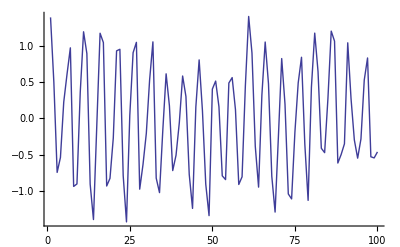

```mathematica
ListPlot[f,Joined->True]
```

The frequency spectrum for this data is obtained by applying the Fourier matrix F to it:

```mathematica
f̃=F.f;
```

Again, we will use a ListPlot to look at the spectrum. However, since f̃ is complex, we will plot the real and imaginary parts of the spectrum separately, in Cells 2.64 and 2.65

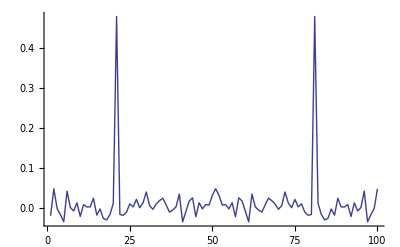

```mathematica
ListPlot[Re[f̃],Joined->True,PlotRange->All]
```

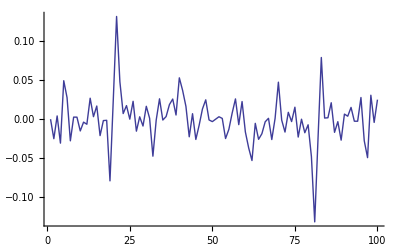

```mathematica
ListPlot[Im[f̃],Joined->True,PlotRange->All]
```

Evidently, the two peaks in the real and imaginary parts of the spectrum correspond to the two Fourier components of sin(40ℼ t) = (ⅇ^(40 π ⅈ t)- ⅇ^(-40 π ⅈ t))/2 ⅈ.  These components have frequencies of ±40 π.  Since the frequency is discretized in units of Δω=2 π/(N Δt)=2 π, the frequency 40 π corresponds to the 21st element of f̃ (since ω=0 corresponds to the first element). This agrees with the plots, which show a peak at the 21st element.

What about the other peak, which is supposed to occur at -40 π? There are no negative frequencies in our spectrum. Rather, frequencies run from 0 to (N-1)Δω in units of Δω=2 π. Recall, however, that f̃ is periodic with period N, [see Eq. (2.3.60)].  In particular, it repeats over the negative frequency range. So we can think of the second peak in the plots, at element 80 of f̃, as actually being at a negative frequency. Since (f̃)_100=(f̃)_0, then (f̃)_80=(f̃)_-20, corresponding to the spectral component with frequency -20 Δω = -40 π.

Thus, the upper half of the frequency spectrum should be thought of as corresponding to negative frequencies. This implies that as we count upwards through the elements of our frequency spectrum, starting with the first element, the frequency increases  like m Δω until we get to the center of the spectrum. At this point the frequency jumps to negative values and approaches zero from the negative side. Therefore, the maximum frequency magnitude kept in our spectrum is

ω_max=N Δω/2=π/Δt .

The frequency ω_max is called the Nyquist frequency for the data. The physical reason why this is the maximum frequency in a set of data can be understood from Fig. 2.10, which displays some time data. The highest-frequency sinusoidal wave that we can interpolate through these data points has a half period equal to Δt: one needs at least two points to determine a sine wave, one at a minimum at one at a neighboring maximum. Thus, the minimum full period defined by the data is 2Δt, and the maximum frequency is given by the Nyquist frequency ω_max=2 π/(2 Δt), Eq. (2.3.65).

More rapid oscillations, with frequency  ω_max+ p N Δω=(2p+1)ω_max, for any integer p can also be made to go through these points as well - see the dashed curve in Fig. 2.10, which corresponds to p=1. However, since these higher-frequency oscillations can always be referred back to the frequency ω_max, we use ω_maxto describe them - there is nothing in the data to distinguish them from an oscillation at ω_max. The identification of  higher frequencies with a lower frequency is called aliasing. This identification arises from the discreteness of the data - there are no data points in between the given data points  that can determine the locations of the peaks and troughs in the dashed curve.

Fig. 2.10 The fastest sinusoidal oscillation that can be unambiguously identified in a set of data has the Nyquist frequency ω_max and period 2 Δt (black curve). Higher-frequency oscillations (dashed curve)  can be translated back to lower frequency.

There is something else that one can see in the real and imaginary parts of the plotted spectrum. Because the input data f was real, the spectral components f̃ have the property that (f̃)_-m=(f̃)_m^*. This is analogous to Eq. (2.3.7) for continuous Fourier transforms, and follows directly from Eq. (2.3.59) for any real set of time data f_n. We  can also see this symmetry in the previous plots if we remember that the periodicity of (f̃)_m implies that (f̃)_-m=(f̃)_(N-m). Thus, for real data, the discrete Fourier transform has the property that

(f̃)_-m=(f̃)_(N-m)=(f̃)_m^*.

## Fast Fourier Transforms

Although the discrete Fourier transforms given by Eqs. (2.3.59) and (2.3.63) work, they are not very useful in practice. The reason is that they are too slow. To evaluate the spectrum for a data set of N elements, a sum over the data set must be done for each frequency in the spectrum. Since there are N elements in the sum and N frequencies in the spectrum, determining every frequency component of a dataset requires of order N^2operations. For N=100 this is not a problem (as we saw above), but for N=10^6 it is out of the question. Datasets of this size are routinely created in all sorts of applications.

Fortunately, a method was developed that allows one to perform the discrete transform and inverse transform with far fewer than N^2 operations. The method is called the method of fast fourier transforms (FFT for short).  Invented by several individuals working independently as far back as the 1940s, it later became well known through the work of Cooley and Tukey at IBM Research Center in the mid-1960s.

The method relies on symmetries of the discrete Fourier transform that allow one to divide the problem into a hierarchy of smaller problems, each of which can be done quickly (the divide and conquer approach). We will not examine the nuts and bolts of the procedure in detail. But it is worthwhile to briefly discuss the idea behind the method.

Given a discrete Fourier transform of a data set with N elements, N assumed even, one can break this transform up into two discrete transforms with N/2 elements each. One transform is formed from the even-numbered data points, the other from the odd-numbered data points:

(f̃)_m=∑_(n=0)^(N-1) f_n ⅇ^(ⅈ 2 π m n/N)
=∑_(n=0)^(N/2-1) f_(2n)ⅇ^(ⅈ 2 π m 2n/N)+ ∑_(n=0)^(N/2-1) f_(2n+1)ⅇ^(ⅈ 2 π m (2n+1)/N)
=∑_(n=0)^(N/2-1) f_(2n)ⅇ^(ⅈ 2 π m n/(N/2))+ ⅇ^(ⅈ 2 π m /N)∑_(n=0)^(N/2-1) f_(2n+1)ⅇ^(ⅈ 2 π m /(N/2))
= (f̃)_m^(e)+ⅇ^(ⅈ 2 π m /N)(f̃)_m^(o).

In the last line, (f̃)_m^(e) denotes the discrete Fourier transform over the N/2 even elements of f_n, and (f̃)_m^(o) denotes the discrete Fourier transform over N/2 odd elements of the data.

At this point it appears that we have gained nothing. The two separate transforms each require of order  N/2 operations, and there are still N separate frequencies (f̃)_m to be calculated, for a total of N^2 operations again.  However, according to Eq. (2.3.60), both (f̃)_m^(e)and (f̃)_m^(o) are periodic with period N/2. Therefore, we really only need to calculate the components m=1,2,...,N/2 for each transform.

In this single step, we have saved ourselves a factor of 2. Now, we apply this procedure again, assuming that N/2 is an even number, saving another factor of 2, and so on, repeating until there is only one  element in each series. This assumes that N = 2^P for some integer P. In fact,  N=2^P  are the only values allowed in the simplest implementations of the FFT method. (If N ≠  2^Pfor some integer P, one typically pads the data with zeros until it reaches a length of 2^P for some P.)

It appears from the above argument that we have taken the original N^2 steps and reduced their number by a factor of 2^P=N, resulting in a code that scales linearly with N. However,  a more careful accounting shows that the resulting recursive algorithm actually scales as N log_2 N, because the number of steps in the recursion equals P=log_2 N. Nevertheless, this is a huge saving over the original N^2 operations required for the discrete Fourier transform.

Writing an efficient FFT code based on the above ideas is not entirely straightforward, and will not be pursued here. [An implementation of the code can be found in Press et al.(1986); see the references at the end of Chapter 1.]  Fortunately, Mathematica has done the job for us, with the intrinsic functions Fourier and InverseFourier. Fourier acts on a list of data f={f_n} to produce a frequency spectrum f̃={(f̃)_m}. The syntax is Fourier[f] and InverseFourier[f̃].

However, just as with continuous Fourier transforms, many different conventions exist for the definitions of the discrete transform. The default convention used by Fourier and InverseFourier differs from that used in Eqs. (2.3.59) and (2.3.63). For a dataset of length N our convention corresponds to

f̃=Fourier[f]/√N, 

		f=√NInverseFourier[f̃].

Of course, any convention can be used, provided that one is consistent in its application. We will stick to the convention of Eq. (2.3.68), since it corresponds to our previous discussion.

The length of the data sets taken as arguments in Fourier and InverseFourier need not be 2^P.   For example, in Cell 2.66 we apply them to the original data of 100 elements created in the previous section.

```mathematica
nn=100;f̃= Fourier[f]/Sqrt[nn] ;
ListPlot[Re[f̃],Joined->True,PlotRange->All]
```

-Graphics-

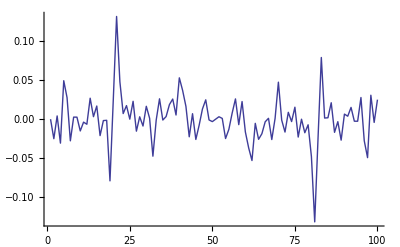

```mathematica
ListPlot[Im[f̃],Joined->True,PlotRange->All]
```

Comparing these plots with those generated in Cells 2.64 and 2.65 using the discrete Fourier transform method, one can see that they are identical.

Let's apply Fourier analysis to a real data signal. Mathematica has the ability to read various types of audio files, such as AIFF format, μ law encoding, or Microsoft WAV format. These sound files can be read using the intrinsic function Import. To read the following sound file of my voice, named ah.AIFF, first determine the current working directory on the hard disk with the command

```mathematica
Directory[]
```

/Users/dubin

Then either copy the file into this directory from the cd on which this book came, or if that is not possible, set the working directory to another hard disk location using the SetDirectory command. Once the file is in the current working directory, the file can be read:

```mathematica
snd =Import["ah.AIFF","AIFF"]
```

-Graphics-

Let's take a look at what is contained in snd by looking at the internal form of the data:

```mathematica
Shallow[InputForm[snd]]
```

Sound[SampledSoundList[<<2>>]]

This data contains a SampledSoundList, which is a set of sound data in the form {{f_o,f_1,f_2,...},samplerate}. The data {f_o,f_1,f_2,...} provides a list of sound levels, which are played consecutively at a rate given by samplerate.  (We applied the command Shallow so that we didn't have to print out the full data list, just the higher levels of the data structure. ) We can extract the sample rate using

```mathematica
samplerate=InputForm[snd][[1]][[1]][[2]]
```

22050

which means the sample rate is 22,050 hertz, a common value used in digitized recordings.  The time between samples, Δt, is just the reciprocal of the sample rate:

```mathematica
Δt=1/samplerate //N
```

0.0000453515

The data itself can be extracted using

```mathematica
f = InputForm[snd][[1]][[1]][[1]][[1]];
```

The length of this data list is

```mathematica
nn= Length[f]
```

36864

Let's look at some of this data over a region where something is happening:

```mathematica
Table[f[[n]],{n,25000,25000+40}]
```

{0.03125,0.015625,0.0078125,0.,0.,0.,-0.0078125,-0.0078125,-0.0078125,0.,0.,0.,0.0078125,0.015625,0.0234375,0.03125,0.03125,0.0390625,0.03125,0.0234375,0.0234375,0.015625,0.015625,0.0234375,0.0234375,0.0234375,0.0234375,0.0234375,0.0234375,0.0234375,0.0234375,0.03125,0.0390625,0.046875,0.046875,0.046875,0.0390625,0.03125,0.015625,0.0078125,0.}

The numbers  giving the sound levels are discretized in units of 0.0078125.  This is because the sound has been digitized, so that amplitude levels are given by discrete levels rather than by continuous real numbers. Note that 1/0.0078125 = 128 = 2^7. This corresponds to 8-bit digitization: the other bit is the sign of the data, ±. (In base two, integers running from 0 to 127 require 7 base two digits, or bits, for their representation.)  Because there are only 128 different possible sound levels in this data file, the sound is not very high quality, as you can tell from the playback above. There is quite a bit of high-frequency hiss, due at least in part to the rather large steps between amplitude levels that create high frequencies in the sound. 
	We can see this in the Fourier transform of the data:

```mathematica
f̃=Fourier[f]/Sqrt[nn];
```

A plot of this Fourier transform (Cell 2.77) shows considerable structure at low frequencies, along with a low level high frequency background.

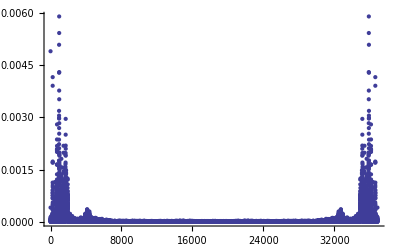

```mathematica
ListPlot[Abs[f̃],PlotRange->All]
```

It is easier to comprehend this data if we plot it in terms of actual frequencies rather than just the order of the elements of f̃, so we will replot the data. The separation Δω between adjacent Fourier modes is 2 π /(N Δt), in radians per second. In hertz, the separation is Δf=1/(N Δt):

```mathematica
Δf = 1/(nn Δt)
```

0.598145

We therefore create a data list, {n Δf,(f̃)_n}, n=0,1,2,...,nn-1:

```mathematica
fdata = Table[{n Δf,f̃[[n+1]]},{n,0,nn-1}];
```

and in Cell 2.80 we plot this list over a range of low frequencies, up to 3000 hertz.

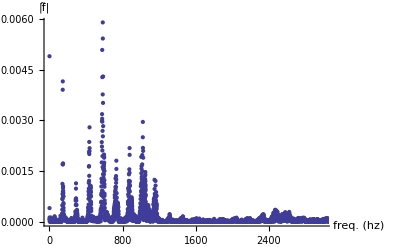

```mathematica
ListPlot[Abs[fdata],PlotRange->{{0,3000},All},AxesLabel->{"freq. (hz)","|f̃|"}]
```

A series of peaks are evident in the spectrum, which  represent harmonics that are important to the "ahhh" sound. There is also a broad spectrum of low-level noise in the data, evident up to quite large frequencies.  We can reduce this noise by applying a  high-frequency filter to the frequency data. We will simply multiply all the data by an exponential factor that reduces the amplitude of the high frequencies:

```mathematica
lowerhalf=Table[f̃[[n]]Exp[-n/600.],{n,1,nn/2}];
```

We only run this filter over half of the data because the upper half of the spectrum corresponds to negative frequencies. To add in the negative-frequency half of the spectrum, it is easiest to simply use Eq. (2.3.66), which is just a statement that the upper half of the spectrum is the complex conjugate of the lower half, written in reverse order:

```mathematica
upperhalf=Reverse[Conjugate[lowerhalf]];
```

However, the lower half includes the zero-frequency point, while the upper half excludes this point. [Frequencies run from 0 to (N-1)Δω.] This zero-frequency point is the last point in the upperhalf, at position n_last= Length[upperhalf]:

```mathematica
Subscript[n, last]= Length[upperhalf];upperhalf=Delete[upperhalf,Subscript[n, last]];
```

We now join these two lists together to get our new spectrum:

```mathematica
Subscript[f̃, new] = Join[lowerhalf,upperhalf];
```

Since the length N of the original data was even, the new data has one less point, because in the above cut-and-paste process we have neglected the center point in the spectrum at the Nyquist frequency. This makes a negligible difference to the sound.

```mathematica
Length[Subscript[f̃, new]]
```

36863

After inverse Fourier-transforming, we can play this resulting sound data using the ListPlay command, choosing to play at the original sample rate of 22050 hertz (Cell 2.86).

```mathematica
ffiltered= InverseFourier[Subscript[f̃, new]];

ListPlay[ffiltered,SampleRate-> samplerate]
```

-Graphics-

Apart from the change in volume level (which can be adjusted using the PlayRange option) the main difference one can hear is that some high frequencies have been removed from this sound sample, as we expected. The audio filtering that we have applied here using an FFT is a crude example of the sort of operations that are employed in modern signal-processing applications. Some other examples of the use of FFTs may be found in the exercises, and in Secs. 6.2.2 and 7.3.

2.3.6 Response of a Damped Oscillator to General Forcing. Green's Function for the Oscillator

We are now ready to use Fourier transforms to solve a physics problem: the response of a damped harmonic oscillator to a general forcing function f(t). Previously, only simple analytic forcing functions (Sec. 1.6) or periodic functions (Sec. 2.1) were considered. Using Fourier transforms, we can now deal with any form of forcing.

In order to obtain a particular solution x_p(t) to the forced damped oscillator equation, Eq. (1.6.2), we act on the right and left-hand sides of the equation with a Fourier transform F̂:

F̂(x''+γ x'+ω_o^2 x)=F̂ f.

Defining the Fourier transform of the forcing function as f̃ = F̂ f, and that of the particular solution as (x̃)_p=F̂ x_p, Eq. (2.3.69) is transformed from an ODE to a simple algebraic equation :

(-ω^2 - ⅈ ω γ + ω_o^2)(x̃)_p(ω)=f̃(ω).

Here, we have applied Eq. (2.3.18) to the derivatives of x_p. We may then divide by the bracket, assuming that the bracket is not zero, to obtain

(x̃)_p(ω)=f̃(ω)/(-ω^2 - ⅈ ω γ + ω_o^2).

Equation (2.3.71) provides the amplitude (x̃)_p(ω) of all  Fourier coefficients in the oscillator's response to the forcing. This equation shows that each Fourier mode in the response is excited only by its corresponding mode in the forcing. This is very similar in form to the response to periodic forcing, Eq.  (2.1.37), except that now the frequency varies continuously rather than in discrete steps.

In order to determine the response in the time domain, an inverse transformation must be applied to Eq. (2.3.71):

x_p(t) = ∫_(-∞)^∞ (ⅇ^(-ⅈ ω t)f̃(ω))/(-ω^2 - ⅈ ω γ + ω_o^2)ⅆω/(2 π).

Remember that this is only one particular solution to the damped oscillator problem; other particular solutions can be found by adding in a homogenous solution x_h(t). [ The homogenoeus solution is hiding in Eq. (2.3.70) - you can find it by setting the forcing equal to zero, implying that the bracket in this equation equals zero. The resulting two solutions for ω yield the two independent homogeneous solutions.]

This is as far as we can go in general. Without knowing the form of the forcing function, we cannot evaluate the frequency integral required in Eq. (2.3.72).

However, we can convert the frequency integral to a time integral by using the convolution theorem. Equation (2.3.71) can be seen to be a product of Fourier transforms; one transform is f̃(ω), and the other is 1/(-ω^2 - ⅈ ω γ + ω_o^2)≡g̃(ω). Since (x̃)_p(ω)=f̃(ω)g̃(ω), the convolution theorem implies that

x_p(t)=∫_(-∞)^∞ f(t_o)g(t-t_o)ⅆ t_o,

where g(t) =(F̂)^-1 g̃(ω) is the inverse transform of g̃.

Although the time integral in Eq. (2.3.73) is not necessarily easier to evaluate than the frequency integral in Eq. (2.3.72), Eq. (2.3.73) has some conceptual and practical advantages. From a practical point of view,  Eq. (2.3.73)  deals only with f(t), whereas Eq. (2.3.72) involves the Fourier transform of f(t), which must be calculated separately. Thus, Eq. (2.3.73) saves us some work. Conceptually, the original differential equation is written in the time domain, and so is Eq. (2.3.73); so now there is no need to consider the frequency domain at all.

However, we do need to calculate the function g(t-t_o). But we need  do so only once, after which we can apply Eq. (2.3.73) to determine the response to any  forcing function.

The function g(t-t_o) is called the Green's function for the oscillator. We will soon see that Green's functions play a very important role in determining the particular solution to both ODEs and PDEs.

The Green's function has a simple physical interpretation. If we take the forcing function in Eq. (2.3.73) to be a Dirac δ-function, f(t_o)=δ(t_o), then Eq. (2.3.73) yields

x_p(t)=g(t).

In other words, the Green's function g(t) is a response of the oscillator to a δ-function force at time t=0. The total impulse (i.e. momentum change) imparted by the force is proportional to ∫_(-∞)^∞ δ(t_o)ⅆ t_o=1, so this force causes a finite change in the velocity of the oscillator. To understand this physically, think of a tuning fork. At t=0, we tap the tuning fork with an instantaneous force that causes it to oscillate. The Green's function is this response. For this reason, Green's functions are often referred to as response functions.

Of course, the tuning fork could already be oscillating when it is tapped, and that would correspond to a different particular solution to the problem. In general, then, there are many different possible Green's functions, each corresponding to different particular solutions to the forcing, with different initial (or boundary) conditions. We will see that when Fourier transforms are used to determine the Green's function for the damped oscillator, this method picks out the particular solution where the oscillator is at rest before the force is applied.

Before we proceed, it is enlightening to step back for a moment and contemplate Eq. (2.3.73). This equation is nothing more than another application of the superposition principle. We are decomposing the forcing function f(t)  into a sum of δ-function forces, each occurring at separate times t=t_o. Each force produces its own response g(t-t_o), which is superimposed on the other responses to produce the total response x_p(t).

Previously, we decomposed the function f(t) into individual Fourier modes. Equations (2.3.72) and (2.3.73) show that the response to the force can be thought of as either a linear superposition of sinusoidal oscillations in response to each separate Fourier mode in the force, or as a superposition of the responses to a series of separate δ-function forces. Fourier decomposition into modes, and decomposition into δ-function responses, are both useful ways to think about the response of a system to forcing. Both rely on the principle of superposition.

We can determine the Green's function for the damped oscillator analytically by applying the inverse Fourier transform to the resonance function g̃:

g(t) =∫_(-∞)^∞ ⅇ^(-ⅈ ω t)/(-ω^2 - ⅈ ω γ + ω_o^2)ⅆω/(2 π)

To evaluate this integral, we must first simplify the integrand, noting that the denominator -ω^2 - ⅈ ω γ + ω_o^2 can be written as (ⅈ ω+ s_1)(ⅈ ω+ s_2), where s_1 and s_2 are the roots of the homogeneous polynomial equation discussed in Sec. 1.6.2, and given by Eqs.  (1.6.14). Then we may write Eq. (2.3.74) as

g(t) =1/(s_2-s_1)∫_(-∞)^∞ ⅇ^(-ⅈ ω t)(1/(ⅈ ω+s_1)-1/(ⅈ ω+ s_2))ⅆω/(2 π),

where we have separated the resonance function into its two components. It is best to perform each integral in Eq. (2.3.75) separately, and then combine the results. Integrals of this sort can be evaluated using InverseFourierTransform :

```mathematica
FullSimplify[InverseFourierTransform[1/(I ω-a),ω,t,Assumptions->Re[a]> 0]/Sqrt[2 Pi]]
```

-ⅇ^(-a t) HeavisideTheta[t]

Taking a=-s_1 in the above integral, and identifying HeavisideTheta as the Heaviside step function h(t), we then have

(F̂)^-1 1/(ⅈ ω+ s_1)= -e^(t s_1)h(t),  Re[s_1]<  0,

with a similar result for the inverse transform involving s_2. Since  Eq.  (1.6.14) implies that the real parts of s_1 and s_2  are identical, equaling the nonpositive quantity  -γ/2, we can apply Eq. (2.3.76) to Eq. (2.3.75), yielding

g(t) = h(t)(ⅇ^(s_1 t)-ⅇ^(s_2 t))/(s_1-s_2)= h(t)ⅇ^(-γ t/2)/(√(ω_o^2-γ^2/4))   sin √(ω_o^2-γ^2/4)t,

where we have used Eq. (1.6.14). A plot of this Green's function for particular choices of γ and ω_o is shown in Fig. 2.11 This Green's function displays just the sort of behavior one would expect from an oscillator excited by a δ-function impulse. For t<0, nothing is happening. Suddenly, at t=0, the oscillator begins to display decaying oscillations. Note that for t>0 this oscillation is simply a homogeneous solution to the ODE, as given by Eq. (1.6.17). This is expected, since for t>0 the forcing has vanished, and the oscillator's motion decays freely according to the homogeneous ODE.

Fig. 2.11  Green's function for the linear oscillator:  response  to a δ-function force. Here ω_o=2 and γ = 1.

One can see that the oscillator is stationary just before t=0 (referred to as t=0^-), but begins moving with a finite velocity directly after the forcing, at t=0^+. What determines  the initial velocity of the oscillator?

Since the oscillator is responding to a δ-function force, the Green's function satisfies the differential equation

g''+γ g'+ω_o^2 g = δ(t).

We can determine the initial velocity by integrating this equation from t=0^- to t=0^+:

∫_(0^-)^(0^+) (g''+γ g'+ω_o^2 g)ⅆt=∫_(0^-)^(0^+) δ(t)ⅆt=1.

Applying the fundamental theorem of calculus to the derivatives on the left-hand side, we have

g'(0^+)-g'(0^-)+γ [g(0^+)-g(0^-)]+ω_o^2∫_(0^-)^(0^+) gⅆt=1.

Since g(t) is continuous and g'(0^-)=0, the only term that is nonzero on the left-hand side is g'(0^+), yielding the result for the initial slope of the Green's function,

g'(0^+)=1.

In fact, if we take the limit of the derivative of Eq. (2.3.77) as t→ 0^+, we can obtain Eq. (2.3.81) directly from the Green's function itself.

Recalling our description of the Green's function as the response of a tuning fork to an impulse, we can now listen to the sound of this Green's function. In Cell 2.88 we take the frequency to be a high C (2093 Hz), with a damping rate of γ=4 hz :

```mathematica
Play[UnitStep[t]Exp[-2t]Sin[2 Pi 2093 t],{t,-1,4},PlayRange->{-1,1}]
```

-Graphics-

The Green's function technique can also be employed to solve for the particular solution of  the general Nth-order linear ODE with constant coefficients, Eq. (1.6.7). Acting with a  Fourier transform on this equation yields

(x̃)_p(ω)  (-ⅈ ω- s_1)(-ⅈ ω- s_2)...(-ⅈ ω-s_N) = f̃(ω),

where s_1,... s_N are the roots of the characteristic polynomial for the homogeneous ODE, described in Sec. 1.6.2. Solving for (x̃)_p(ω) , taking the inverse transform, and using the convolution theorem, we are again led to Eq. (2.3.73). Now, however, the Green's function is given by the following inverse transform :

g(t)=(F̂)^-1 1/((-ⅈ ω- s_1)(-ⅈ ω- s_2)....(-ⅈ ω-s_N)).

This inverse transformation can be performed by separating the resonance function in Eq. (2.3.83) into individual resonances as in Eq. (2.3.75), assuming no degeneracies occur (i.e., s_i ≠ s_j for all i≠ j):

g(t) =-∑_(i=1)^N (F̂)^-1 1/(ⅈ ω+s_i)1/(∏_(j=1
j≠ i)^N (s_i-s_j)) .

If we further assume that none of the system's modes are unstable, so that Re s_i  < 0 for all i, we can apply Eq. (2.3.76) to obtain the Green's function

g(t)=h(t)∑_(i=1)^N ⅇ^(s_i t)/(∏_(j=1
j≠ i)^N (s_i-s_j)).

The case of a system exhibiting unstable oscillations, or the case of degeneracy, can also be easily handled using similar techniques, and is left to the exercises.

We have finally solved the problem, posed back in Sec. 1.6,  of determining the response of an oscillator (or, more generally, a linear ODE of Nth-order with constant coefficients) to a forcing function f(t) with arbitrary time dependence. Equation (2.3.85) shows that the response to a δ-function force at time t=0 is a sum of the solutions ⅇ^(s_i t)to the homogeneous equation. This response, the Green's function for the system, can be employed to determine the response to an arbitrary force by applying Eq. (2.3.73).

As a simple example, say the forcing f(t) grows linearly with time, starting at t=0: f(t) =t  h(t) .

Then Eq.  (2.3.73) implies that a particular solution to this forcing is given by

x_p(t)=∫_(-∞)^∞ t_o h(t_o)g(t-t_o)ⅆ t_o.

Substituting Eq. (2.3.85) into Eq. (2.3.86), we find that a series of integrals of the form
∫_(-∞)^∞ t_o h(t_o) h(t-t_o)ⅇ^(s_i(t-t_o))ⅆ t_o must be performed.  The step functions in the integrand limit the range of integration to  0<t_o<t, so each integral results in
		∫_0^t t_o ⅇ^(s_i(t-t_o))ⅆ t_o=(ⅇ^(s_i t)-(1+ s_i t))/s_i^2.
Finally, the total response is the sum of these individual terms:

x_p(t)=∑_(i=1)^N (ⅇ^(s_i t)-(1+ s_i t))/(s_i^2∏_(j=1
j≠ i)^N (s_i-s_j)), t>0.

We see that part of the response increases linearly with time, tracking the increasing applied force as one might expect. However, another part of the response is proportional to a sum of decaying homogeneous solutions, ⅇ^(s_i t).  The particular solution given by Eq. (2.3.87) is the one for which the system is at rest before the forcing begins.

Exercises for Sec. 2.3

(1) Find the Fourier transform for the following functions. Use time transform conventions for functions of t, and space transform conventions for functions of x. Except where indicated, do the required integrals by hand. (You may check your results using Mathematica.)

(a) f(t)=h(t) ⅇ^(-a t)sin ω_o t, a>0, where h(t) is the Heaviside step function

(b) f(t) = t  for -a<t<a, and zero otherwise

(c)  f(t)=cos ω_o t for -a<t<a, and zero otherwise

(d) f(x) =x/(1 + x^2).   (You may use Mathematica  to help with the required integral.)

(e) f(x) = ⅇ^(-x^2). (You may use Mathematica  to help with the required integral.)

(2) Verify by hand that the inverse transform of the functions f̃(ω) found in Exercise (1) returns to the listed functions. [You may use Mathematica to help check integrals, and you may also use results such as Eq. (2.3.47) or  Eq. (2.3.76) without proving them.]

(3) Plot the Fourier transform |f̃(ω)| arising from Exercise (1)(c), taking ω_o = 3 and a= 10,20,30. Comment on the result. What will f̃(ω) converge to in the limit as a→  ∞?

(4) Starting with a Fourier sine series, Eq. (2.2.10), prove the relations for a Fourier sine transform, Eqs. (2.3.10).

(5) Repeat Exercise (1)(a) using a cosine transform on 0<x<∞.

(6) Repeat Exercise (1)(d) using a sine transform on 0<x<∞. Use Mathematica to help with the integral.

(7) Let ω/(ⅈ ν + ω) (ν>0) be the Fourier transform of f'(t). Find f(t) by hand.

(8) Find the value of the integral ∫_(-∞)^∞ ⅇ^(-ν |t_o|)cos ω_o (t-t_o)ⅆ t_o using the convolution theorem. Use paper and pencil methods to do all required transforms and inverse transforms.

(9) Show that the following functions approach  Dirac δ functions  and/or their derivatives, and find the coefficients of these δ-functions:

(a) f(t)=lim_(Δt→0) t {h(t+Δt)-h(t-Δt)}/Δt^3

(b) f(t) =lim_(Δt→0)   exp[-(9-12 t-2 t^2+4 t^3+t^4)/Δt^2]/|Δt|.

(c) f(t)=lim_(Δω→∞) (Δω t cos Δω t-sin Δω t)/t^2

(Hint: in each case, consider the integral ∫_(t_o-ϵ)^(t_o+ϵ) f(t)g(t)ⅆt for some function g(t) . Also, it is useful to plot the functions to see what they look like.)

(10) Evaluate the following integrals by hand:

(a)∫_-10^0  t^5 δ(t^3+8)ⅆt.

(b) ∫_(-∞)^∞ δ(cos  t)/t^2ⅆt.

(c) ∫_3^∞ δ(sin t^2)/t^2ⅆt.

(11) Evaluate the following generalized Fourier and inverse-Fourier integrals by hand:

(a) ∫_0^∞ cos ω t ⅆω/π.

(b) ∫_(-∞)^∞ t/(ⅈ a+t) ⅇ^(ⅈ ω t)ⅆt     ( a real, a>0).

(c) ∫_(-∞)^∞ -i ω  ⅇ^(-ⅈ ω t)ⅆω/(2π).

(d) ∫_(-∞)^∞ t h(t) ⅇ^(ⅈ ω t)ⅆt , where h(t) is the Heaviside step function.

(e) ∫_0^∞ tanh(ω T)  sin ω t ⅆω/π (T>0).

(f) ∫_0^∞ ⅇ^(-ⅈ ω t)/ω ⅆω/π .

(g) ∫_(-∞)^∞ ⅇ^(-ⅈ ω t)/ω^2 ⅆω/π .

(12) Prove Parseval's theorem: for any function f(t) with a Fourier transform f̃(ω),

∫_(-∞)^∞ |f(t)|^2 ⅆt=∫_(-∞)^∞ |f̃(ω)|^2 ⅆω/2π.

(13) The uncertainty principle of Fourier analysis, Eq. (2.3.24), can be made more precise by defining the width of a real function f(t) as follows. Let the square of the width of the function be Δt^2 = ∫t^2 f^2(t)ⅆt/∫f^2(t)ⅆt. (We square the function because it may be negative in some regions.) Thus, Δt is the root mean square (rms) width of f^2. 
	Now define the rms width Δω of the Fourier transform function, f̃(ω), in the same manner: Δω^2=∫(ω^2(|f̃(ω)|))^2 ⅆω/∫(|f̃(ω)|)^2 ⅆω. (We take the absolute value of f̃ because it may be complex.)

(a) Show that Δω^2=∫(ⅆf/ⅆt)^2 ⅆt/∫f^2(t)ⅆt. (Hint: Use Eq. (2.3.88).)

(b) Consider the function u(t) = t f(t) + λ ⅆf/ⅆt. Show that  ∫u^2(t)ⅆt=(Δt^2+λ^2 Δω^2-λ)∫f^2(t)ⅆt. (Hint: f ⅆf/ⅆt=(1/2) ⅆ f^2/ⅆt.)

(c) Using the fact that ∫u^2(t)ⅆt≥ 0 for all real λ, prove that

Δω Δt≥ 1/2.

(Hint: The quadratic function of λ in part (b) cannot have distinct real roots.) Equation (2.3.89) is an improved version of the uncertainty principle, and is directly analogous to Heisenberg's uncertainty principle ΔE Δt≥ ℏ/2, where E is the energy.

(d) Show that equality in Eq. (2.3.89) is achieved only for Gaussian functions, f(t) = f_o exp(-a t^2), a>0. Thus, Gaussians exhibit the "minimum uncertainty" in that the product Δω Δt is minimized. (Hint: Show that Δω Δt= 1/2 only if u(t)=0,  and use this equation to solve for f(t). )

(14) One can perform discrete Fourier transforms and inverse transforms on smooth data simply by discretizing the Fourier and inverse Fourier integrals.

(a) Take a numerical Fourier transform of the smooth function ⅇ^(-t^2) in the range -3≤ t≤ 3 by using Eqs. (2.3.53) and (2.3.54), taking Δt = 0.1 and Δω =0.4. with ω in the range-6≤ ω≤ 6.   Compare the  result with the exact Fourier transform, found analytically, by plotting both on the same graph vs. frequency. (This requires you to determine the frequency associated with the position of a given element in the transformed data.)

(b) Take the inverse transform of the data found in part a) using Eqs. (2.3.55) and (2.3.56). Does the result return to the original function? Plot the difference between the original function and this result.

(c) Repeat (a) and (b), but take the range of ω to be -3≤ ω≤ 3.

(15) Using a discrete Fourier transform  that you create yourself (not a fast Fourier transform), analyze the noisy data in Table 2.2 and determine the main frequencies present, in hertz. The time between samples is Δt=0.0005 s.

Table 2.2:  Data for Exercise (15)

```mathematica
f={3.42637,2.26963,-1.70619,-2.65432,0.24655,1.40931,0.470959,-0.162041,-0.336245,-0.225337,-0.112631,0.447789,-0.667762,-1.21989,0.269703,2.32636,2.01974,-2.38678,-3.75246,0.298622,3.86088,2.27861,-1.77577,-2.46912,0.134509,1.02331,0.715012,-0.339313,0.0948633,-0.0859965,0.0371488,0.347241,-0.353479,-1.47499,-0.15022,2.68935,1.88084,-2.08172,-3.83105,0.0629925,3.87223,2.13169,-1.64515,-2.42553,-0.288646,1.4674,0.315207,-0.480925,-0.216251,0.144092,-0.00670936,0.382902,-0.495702,-1.38424,0.256142,2.22556,2.02433,-2.33588,-3.60477,-0.163791,3.55462,2.17247,-1.94027,-2.41668,-0.0176065,1.05511,0.489467,-0.515668,-0.122057,-0.112292,-0.0326432,0.489771,-0.690393,-1.27071,0.274066,2.29677,1.97186,-2.3131,-3.99321,-0.228793,3.95866,1.84941,-1.95499,-2.2549,0.104038,1.29127,0.769865,-0.362732,-0.271452,-0.0638439,0.0734938,0.0774499,-0.333983,-1.56588,-0.193863,2.37758,1.92296,-2.12179,-3.87906,-0.21919,3.96223,2.01793,-2.05241,-2.7803,-0.296432,1.18286,0.687172,-0.449909,-0.193565,0.191591,0.310403,0.437337,-0.706701,-1.35889,-0.0630913,2.54978,1.79384,-2.21964,-3.88036,-0.127792,3.882,2.32878,-1.56785,-2.6985,0.219771,1.32518,0.669142,-0.44272,0.123107,-0.15768,0.375066,-0.0682963,-0.467915,-1.3636,-0.235336,2.28427,1.80534,-1.83133,-3.58337,0.0344805,3.42263,2.21493,-1.86957,-2.62763,-0.159368,1.50048,0.48287,-0.453638,-0.172236,-0.124694};
```

(16) A Fourier series or transform is a way to decompose a function f(t) in terms of complex orthogonal basis functions ⅇ^(-ⅈ ω t). The method relies on the orthogonality of these basis functions. A discrete Fourier transform can be thought of as a way to decompose vectors f  of dimension N in terms of N   complex orthogonal basis vectors.  The mth basis vector is e^(m)={1,ⅇ^(-2 π m ⅈ/N),ⅇ^(-4 π m ⅈ/N),....,ⅇ^(-2π m ⅈ(N-1)/N)}.

(a) Show directly that these basis vectors are orthogonal with respect to the following  inner product defined for two vectors f and g: (f,g) = f^*·g. [Hint: Use the following sum: ∑_(n=0)^(N-1) x^N=(1-x^N)/(1-x)]

(b) Show that the decomposition of a vector f in terms of these basis vectors,  f=∑_(m=0)^(N-1) (f̃)_m e^(m), leads directly to Eq. (2.3.63).

(c) Use the orthogonality of these basis vectors to determine the coefficients (f̃)_m, and compare the result with Eq. (2.3.59).

(17) A data file on the disk accompanying this book, entitled aliendata.txt, contains a (simulated) recording made by a (simulated) scientist listening for alien communications from nearby stars. Read in this datafile from the cd of this book using the command <<aliendata.txt. (A Directory and/or SetDirectory command may also be necessary.) Within this file is a data list of the form f = {...}. Reading in the file defines the data list f. Use ListPlay to play the data  as a sound. Take the samplerate to be 22,050 hertz.

As you can hear, the data is very noisy. By taking a Fourier transform,  find a way to remove this noise by applying an appropriate filter function to the  Fourier-transformed data. What is the aliens' message? Are they peaceful or warlike?

[Caution: This data file is rather large. When manipulating it, always end your statements with a semicolon to stop any output of the file.]

(18)(a) A damped harmonic oscillator  is driven by a force of the form f(t) = h(t)t^2 Exp(-t), where h(t) is a Heaviside step function. The oscillator satisfies the equation

x''+2 x'+4x=f(t).

Use pencil-and-paper methods involving Fourier transforms and inverse transforms to find the response of the oscillator, x(t), assuming that x(0)=0 and x'(0)=1. Plot the solution for x(t).

(b) Repeat the analysis of part (a) for force of the form f(t) =h(t) t sin 4t. Instead of Fourier methods, this time use the Green's function for this equation. Plot the solution for 0<t<10.

(19) Use Fourier transform techniques to find and plot the current in amperes as a function of time in the circuit of Fig. 2.12 when the switch is closed at time t=0.

Fig. 2.12.

(20)(a) Find a Green's function for the following operator:

L̂ x=x''''+2 x'''+6 x''+5 x'+2x.

(b) Use the Green's function found from part (a) to determine the solution x(t) to L̂ x=h(t) t ⅇ^-t cos  t, x(0)=x'(0)=x''(0)=x'''(0)=0. Plot the solution.

(21)(a) The FFT can be used to solve numerically for particular solutions to differential equations with constant coefficients.  This method is quite useful and important for solving certain types of PDEs numerically, such as Poisson's equation under periodic boundary conditions (see Chapters 6 and 7), but can also be used to solve ODEs.  For example, consider the following ODE:

x''+x'+x=h(t)t ⅇ^-t sin 3t.

Find a particular solution on the interval 0≤ t≤ 4 using an FFT . To do so, first discretize time as t=n Δt, n=0,1,2,...,N-1 with N=41, taking Δt = 0.1. Make a table of the forcing function at these times, and take its FFT.  Then, use what you know about Fourier transforms to determine a discretized  form for the transform of x, x̃. Take the inverse FFT of this data and plot the resulting particular solution vs. time on 0≤ t≤ 4.

(b) This particular solution is periodic, with period T=4.1,  since the FFT is equivalent to a Fourier series solution with this periodicity. This solution is correct only in the first period, from 0<t<T; the analytic particular solution is not periodic, but should match the FFT solution in 0<t<T.  To prove this, note that  this particular solution satisfies  periodic boundary conditions x(0)=x(T),x'(0)=x'(T). Solve the ODE  analytically for these boundary conditions using DSolve, and plot the result on top of the FFT result from part (a) on 0≤ t≤ T.

(22)(a) The periodic δ-function δ^(P)(t) with period T given  by  Eq. (2.3.48) has Fourier components of equal amplitude over all frequencies, playing continuously. Do you think that the hairs in your ear responsible for hearing frequencies at around, say, 500 Hz, are being excited continuously by the  500-Hz frequencies in the δ-function, or only when there is a chirp? Explain your reasoning in several sentences, with diagrams if necessary. (Hint: Hairs respond to a range of frequencies around their resonance peak, not just a single frequency. What is the effect on the amplitude of the hair's motion  of adding together these different frequency components in the forcing? Think about constructive and destructive interference. )

(b) Find a particular solution for the response of a damped oscillator (a model of one of the hairs) to a periodic δ-function using Green's functions. The oscillator satisfies  x''+ γ x'+ω_o^2 x=δ^(P)(t) . Plot the result over a time of 5 T for ω_o T=60 and for (i) γ T=0.01  (ii) γ T=0.1, (iii) γ T=1. (iv) γ T=10. Roughly how large must γ T be for each response to a δ function kick to be easily distinguishable from others?

(c) Create and play a periodic δ-function with different values of T, from 1/10 to 1/200 s. Determine the smallest value of T for which you can distinguish the chirps. Use the result of part (b) along with this result to crudely estimate a value of γ for the human auditory system.

(23)(a) Play the following periodic δ-function for which the phases have been randomized:

```mathematica
T = 0.2; 1 + 2Sum[ Cos[2 Pi n  t/T+ 2 Pi Random[]],{n,1,300}];
```

Does this still sound like a periodic δ-function?  Previously in Sec 2.1.9, we found that randomizing the phases of the Fourier components in a waveform made no difference to the sound a waveform makes. Can you explain why there is a difference now? (Hint: Think about destructive interference.)

(b) The modes in a Fourier series or transform have  amplitudes that are constant in time, but somehow the series or transform is able to produce sounds whose loudness (amplitude) varies in time, as in a periodic δ-function. Given the results of part (a), explain in a few words how this is accomplished.

(c) Reduce the period T of δ^(P)(t) to a value below that found in part (c) of the previous exercise.  Does randomizing the phases make as much difference to the sound as for part (a)? Why or why not?

(24) Three coupled oscillators are initially at rest (at t=-∞). Their equilibrium positions are x_(1o)=2, x_(2o)=1,x_(3o)=0. The oscillators satisfy the equations

x_1''=-2(x_1-x_2-1) - x_1' ,

x_2''=-2(x_2-x_1+1) - x_2' -2(x_2-x_3-1),

x_3''=-2(x_3-x_2+1) - x_3' + f(t) .
 The third oscillator in the chain is given a bump, f(t)=6 ⅇ^(-4|t|). Use Fourier transform methods to solve for the motion of the oscillators. Plot the motion of all three oscillators as an animation by plotting their positions x_i(t)  as a set of ListPlots at times from -1<t<9 in units of 0.2.

## 2.4 Green's Functions

2.4.1 Introduction

Consider a dynamical system described by a general Nth-order inhomogeneous linear ODE, such as Eq. (1.6.1). In operator notation this ODE can be written as

L̂ x(t)=f(t).

The Green's function  can be used to find a particular solution to this ODE. The Green's function is a function of two arguments, g=g(t,t_o). This function satisfies

L̂ g(t,t_o)=δ(t-t_o).

According to this equation,  g(t,t_o) is the response of the system to a δ-function forcing at time t=t_o.

The Green's function can be used to obtain a particular solution to Eq. (2.4.1) by means of the following integral:

x_p(t) = ∫_(-∞)^∞ g(t,t_o)f(t_o)ⅆ t_o.

We have already seen a similar equation for the particular solution  in terms of a Green's function for an ODE with constant coefficients, Eq. (2.3.73). There, the Green's function was written as g(t-t_o) rather than g(t,t_o), because when the ODE has constant coefficients the origin of time can be displaced to any arbitrary value, so only the time difference between t and t_o is important in determining the response at time t to an impulse at time t_o.

We can easily show that Eq. (2.4.3) satisfies the ODE, Eq. (2.4.1). Acting with L̂ on Eq. (2.4.3), we obtain

L̂ x_p(t) = ∫_(-∞)^∞ L̂ g(t,t_o)f(t_o)ⅆ t_o=∫_(-∞)^∞ δ(t-t_o)f(t_o)ⅆ t_o=f(t),

where we have used Eq. (2.4.2).

We have not yet specified initial or boundary conditions that go along with Eq. (2.4.2) for defining the Green's function.  In initial-value problems, it is convenient to choose the initial condition that g=0 for t<t_o, so that the system is at rest when the impulse is applied .

For boundary-value problems, other choices are made in order to satisfy boundary conditions, as we will see in Sec. 2.4.4.

The time integral in Eq. (2.4.3) runs all the way from -∞ to ∞, so it seems that we need to know everything about both the past and future of the forcing function to determine x_p at the present time. However, the choice g=0 for t<t_o implies that the integral in Eq. (2.4.3) really runs only from -∞ to t, so only past times are necessary. Also, in typical problems there is usually an initial time t_i (possibly far in the past) before which the forcing can be taken equal to zero (i.e. the beginning of the experiment). For these choices the integral really runs only from t_i to t:

x_p(t) =∫_t_i^t g(t,t_o)f(t_o)ⅆ t_o.

We can see that this particular solution will be zero for t<t_i, since g(t,t_o)=0 for t<t_o. Thus, this particular solution is the one for which the system is at rest before the forcing begins.

We will now consider how to construct a solution to Eq. (2.4.2) for the Green's function.  There are several methods for doing so. We have already seen one method using Fourier transforms in Sec. 2.3.6, applicable to ODEs with constant coefficients. Here, we consider a general analytic method for any linear ODE, where the Green's function is written as a sum of homogeneous solutions to the ODE. We also discuss numerical methods for determining the Green's function. In Chapter 4, we will consider another analytic method, applicable only to boundary-value problems, in which we decompose g in terms of operator eigenmodes, resulting in the bilinear equation for the Green's function.

2.4.2 Constructing the Green's Function from Homogeneous Solutions

## Second-Order ODEs

In this subsection we will construct the Green's function for a linear second-order ODE using homogeneous solutions. We will then discuss a generalization of the solution that is applicable to higher-order ODES.

For a general linear second-order ODE of the form of Eq. (1.6.1), the Green's function satisfies

L̂ g(t,t_o)≡∂^2/(∂t^2)g(t,t_o)+u_1(t)∂/(∂t)g(t,t_o) +u_o(t)g(t,t_o) =δ(t-t_o).

Assuming that we are solving an initial-value problem, we will take the initial condition that g(t,t_o)=0 for  t≤ t_o.

When t>t_o, the Green's function satisfies the homogenous ODE L̂ g(t,t_o)=0, and therefore g can be written as a sum of the two independent homogeneous solutions to the ODE (see Sec. 1.6):

g(t,t_o)= C_1 x_1(t)+C_2 x_2(t),   t> t_o.

We are then left with the task of determining the constants C_1 and C_2. One equation for these constants can be found by applying the initial condition that the system is at rest before the impulse is applied, so that g=0 at t=t_o.Applying this condition to Eq. (2.4.5) yields

g(t_o,t_o)=0= C_1 x_1(t_o)+C_2 x_2(t_o).

To obtain one more equation for the constants C_1 and C_2, we integrate Eq. (2.4.4) from a time just before t_o, t_o^-, to a time just after t_o, t_o^+:

∫_(t_o^-)^(t_o^+) (∂^2/(∂t^2)g(t,t_o)+u_1(t)∂/(∂t)g(t,t_o) +u_o(t)g(t,t_o))ⅆt =∫_(t_o^-)^(t_o^+) δ(t-t_o)ⅆt=1.

Assuming that u_o(t) and  u_1(t) are both continuous at t=t_o, we can replace them by their values at t=t_oand take them outside the integral. We can then apply the fundamental theorem of calculus to the integral of the derivatives, yielding

∂/(∂t)g(t,t_o)|_(t=t_o^+)-∂/(∂t)g(t,t_o)|_(t=t_o^-) +u_1(t_o)[g(t_o^+,t_o)-g(t_o^-,t_o)]+u_o(t_o)∫_(t_o^-)^(t_o^+) g(t,t_o)ⅆt=1.

Since g=0 for t≤ t_o and g is continuous at t=t_o, all terms on the left-hand side vanish except for the first term, yielding

∂/(∂t)g(t,t_o)|_(t=t_o^+)=1.

Substituting for g using Eq. (2.4.5) yields the second equation for C_1 and C_2,

C_1 x_1'(t_o)+C_2 x_2'(t_o)=1.

We may now solve for C_1 and C_2 using Eqs. (2.4.6) and (2.4.7). The result is

g(t,t_o)=(x_2(t_o)x_1(t)-x_1(t_o)x_2(t))/(W(t_o)),  t> t_o,

where  the function W(t) is the Wronskian, defined as W(t)≡x_1'(t)x_2(t)-x_2'(t)x_1(t) .

If the Wronskian W(t_o) is zero for some value of t_o, then according to Eq. (2.4.8) g is undefined. However, one can show (although we will not do so here) that the Wronskian is always nonzero if the homogeneous solutions x_1 and x_2 are linearly independent. A proof of this statement can be found in any elementary book on ODEs, such as Boyce and DiPrima (1969) (see the references at the end of Chapter 1).

For completeness, we also note our initial condition:

g(t,t_o)=0,  t<  t_o.

Equations (2.4.8) and (2.4.9) are a solution for the Green's function  for a general second-order ODE. This solution requires that we already know the independent homogeneous solutions to the ODE,  x_1(t) and x_2(t). These solutions can often be found analytically, using DSolve for example, but we could also use numerical solutions to the homogeneous ODE, with two different sets of initial conditions so as to obtain independent numerical approximations to  x_1(t) and x_2(t). Examples of both analytic and numerical methods for finding homogeneous solutions can be found in the exercises at the end of Sec. 1.6.

Equations (2.4.8) and (2.4.9) can now be used in Eq. (2.4.3) to obtain a particular solution to Eq. (2.4.1). Since g(t,t_o)=0 for  t_o>t, we obtain

x_p(t) = ∫_(-∞)^t g(t,t_o)f(t_o)ⅆ t_o=x_1(t)∫_(-∞)^t (x_2(t_o)f(t_o))/(W(t_o))ⅆ t_o-x_2(t)∫_(-∞)^t (x_1(t_o)f(t_o))/(W(t_o))ⅆ t_o.

Equation (2.4.10) is a form for the particular solution to the ODE that can also be found in elementary textbooks, based on the method of variation of parameters. Here we have used Green's-function techniques to obtain the same result. Note that one can add to Eq. (2.4.10) any homogeneous solution to the ODE in order to obtain other particular solutions. Equation (2.4.10) is the particular solution for which the system is at rest before the forcing begins.

## Example

As an example of the Green's function technique applied to a second-order ODE with time-varying coefficients, let us construct the Green's function for the operator

L̂ x=x''-n x'/t,   n ≠ -1.

One can verify by substitution that this operator has two independent homogeneous solutions

x_1(t) = 1,
x_2(t) = t^(n+1)/(n+1).
Then the Wronskian is

W(t)=x_1'(t)x_2(t)-x_2'(t)x_1(t)=0 - 1 t^n=-t^n,
and Eq. (2.4.8) for the Green's function becomes

g(t,t_o)=1/(n+1)((t(t/t_o))^n-t_o),   t> t_o.

We can use this Green's function to obtain a particular solution to L̂ x(t)=f(t). Let's take the case f(t) = t^α h(t), where h(t) is the Heaviside step function. Then the particular solution given by Eq. (2.4.3) is

x_p(t) =∫_(-∞)^t g(t,t_o)t_o^α h(t_o)ⅆ t_o = ∫_0^t 1/(n+1)[(t(t/t_o))^n-t_o]t_o^α ⅆ t_o,
where on the right-hand side we have assumed that t> 0 in order to set h(t_o)=1. If  t<0, then h(t_o)=0 for the entire range of integration, and x_p(t)=0. This is expected, since the Green's function has built in the initial condition that the system is at rest before forcing begins.

For this simple forcing function the integral can be performed analytically, yielding

x_p(t) = t^(2+α)/((2+α)(1+α-n)), t>  0.

## Nth-Order ODEs

The Green's function for a general linear ODE of order N can also be determined in terms of homogeneous solutions. The Green's function satisfies

(ⅆ^N x)/(ⅆ t^N)+ u_(N-1)(t)(ⅆ^(N-1)x)/(ⅆ t^(N-1))+...+ u_1(t)ⅆx/ⅆt + u_o(t)x=δ(t-t_o).

For t< t_o we again apply Eq. (2.4.9) as our initial condition. For  t> t_o the Green's function is a sum of the N independent homogeneous solutions,

g(t,t_o)= ∑_(n=1)^N C_n x_n(t),   t>t_o.

We now require N equations for the N coefficients C_n. One such equation is obtained by integrating the ODE  across the δ-function from t_o^- to t_o^+. As with the case of the second-order ODE, only the highest derivative survives this operation, with the result

ⅆ^(N-1)/(ⅆ t^(N-1))g(t,t_o)|_(t=t_o^+)=1.

Only this derivative exhibits a jump in response to the δ-function. All lower derivatives are continuous, and therefore equal zero as a result of Eq. (2.4.9):

ⅆ^n/(ⅆ t^n)g(t,t_o)|_(t=t_o^+)=0,n=1,2,...,N-2.

Also, the Green's function itself is continuous (if N>1),

g(t_o,t_o)=0.

When Eq. (2.4.12) is used in Eqs. (2.4.13)-(2.4.15), the result is N equations for the N unknowns C_n. Solving these coupled linear equations allows us to determine the Green's function in terms of the homogeneous solutions to the ODE. For the case of an ODE with constant coefficients, the result returns us to Eq. (2.3.85). Knowledge of the Green's function, in turn, allows us to determine any particular solution. We leave specific examples of this procedure to the exercises.

2.4.3 Discretized Green's Function I : Initial-Value Problems by Matrix Inversion.

Equation (2.4.3) can be thought of as an equation involving  a linear integral operator, (L̂)^-1. This operator is defined by its action on any function f(t):

(L̂)^-1 f≡∫_(-∞)^∞ g(t,t_o) f(t_o)ⅆ t_o.

We have already encountered other linear integral operators: the Fourier transform and its inverse  are both integral operators, (see. Sec. 2.3.3). The  operator  (L̂)^-1 appears in the particular solution given in Eq. (2.4.3), which may be written as

x_p=(L̂)^-1 f.

We call this operator (L̂)^-1 because it is the inverse of the differential operator L̂. We can see this by operating on Eq. (2.4.16) with L̂, and using Eq. (2.4.3):

L̂(L̂)^-1 f=∫_(-∞)^∞ L̂ g(t,t_o) f(t_o)ⅆ t_o=∫_(-∞)^∞ δ(t-t_o) f(t_o)ⅆ t_o=f(t).
This shows that (L̂)^-1has the correct property for an inverse: L̂(L̂)^-1returns without change any function to which it is applied.

We can see that (L̂)^-1 is the inverse of L̂ in another way. The ODE that x_p satisfies is L̂ x_p=f. If we apply (L̂)^-1to both sides, we obtain (L̂)^-1 L̂ x_p=(L̂)^-1 f=x_p, where in the last step we used Eq. (2.4.17).  This shows that (L̂)^-1 L̂ also returns without change any function to which it is applied. Since

L̂(L̂)^-1 x_p=(L̂)^-1 L̂ x_p=x_p,

for a function x_p(t), this again proves that (L̂)^-1is the inverse of L̂.

Note, however, that there seems to be something wrong with Eq. (2.4.18). There are  functions x_h(t) for which L̂ x_h=0: the general homogeneous solutions to the ODE. For such functions,  (L̂)^-1 L̂ x_h = 0≠x_h. In fact, one might think that since L̂ x_h=0, (L̂)^-1cannot even exist, since matrices that have a finite nullspace do not have an inverse (and we already know that by discretizing time L̂ can be thought of as a matrix).

The resolution to this paradox follows by considering the discretized form of the Green's function. By discretizing the ODE, we can write it as a matrix equation, and solve it via matrix inversion. In this approach, the operator L̂ becomes a matrix L, and the operator (L̂)^-1 is simply the inverse of this matrix, L^-1 .

We examined this procedure for homogeneous initial-value problems in Sec. 1.6.3. Adding the inhomogeneous term is really a very simple extension of the previous discussion.  As an example, we will solve the first-order ODE

L̂ x=ⅆx/ⅆt+u_o(t)x=f(t),  x(0)=x_o.

A discretized version of the ODE  can be found using Euler's method, Eq. (1.4.7). Defining t_n= n Δt, Euler's method implies

x(0)=x_o,
(x(t_n)-x(t_(n-1)))/Δt+ u_o(t_(n-1))x(t_(n-1))=f(t_(n-1)), n>0.

These linear equations can be written as a matrix equation,

L·x=f,

where the vector x= {x(0),x(t_1),x(t_2),...}, and the vector f=  {x_o,f(t_o),f(t_1),...} contains the force and  initial condition.  The matrix L is a discretized version of the operator L̂:

L=(1 | 0 | 0 | 0 | ...
-1/Δt+u_o(t_o)  | 1/Δt | 0 | 0 | ...
0 | -1/Δt+u_o(t_1) | 1/Δt | 0 | ...
0 | 0 | -1/Δt+u_o(t_2)  | 1/Δt | ...
⋮ | ⋮ | ⋮ | ⋮ | ⋱).

A similar matrix was introduced for the homogeneous equation, in Sec. 1.6.3 [see Eq. (1.6.21)]. The only difference here is that we have multiplied by 1/Δt everywhere but in the first row, so that Eq. (2.4.21) has the same form as Eq. (2.4.19).

We can solve Eq. (2.4.20) for the unknown vector x  by using matrix inversion:

x=L^-1·f.

Note the resemblance of this equation to Eq. (2.4.17).  The matrix inverse appearing in Eq. (2.4.23) is a discretized version of the inverse operator (L̂)^-1.

From a theoretical perspective, it is important to note that both the forcing and the initial condition are included in Eqs. (2.4.21) and (2.4.23). The initial condition x(0)=x_o is built into the forcing function.  If we wish to solve the homogeneous equation for a given initial condition, all that we need do is set all elements of f  but the first equal to zero. In this case Eq. (2.4.21) returns to the form of Eq. (1.6.21). We can see now that there is no difference between finding a  solution to the homogeneous equation and finding a solution to the inhomogeneous equation. After all, the matrix inversion technique is really just Euler's method, and Euler's method is the same whether or not the ODE is homogeneous.

We have seen how the forcing contains the inhomogeneous initial conditions for the discretized form of the ODE; but is this also possible for the actual ODE itself?  The answer is yes. For instance, to define the initial condition x(0)=x_o in the previous first-order ODE, we  can use a δ-function:

ⅆ x/ⅆt + u_o(t) x=f(t) + x_o δ(t).

If we integrate from 0^- to 0^+, we obtain x(0^+)-x(0^-)=x_o. Now let us assume that x(t)=0 for t<0. [This is the initial condition associated with  (L̂)^-1: see Eq. (2.4.16), and recall that g=0 for t<t_o.] We then arrive at the proper initial condition, x(0^+)=x_o. Furthermore, for t>0 the ODE returns to its previous form, Eq. (2.4.19). By solving Eq. (2.4.24) with the initial condition x(t)=0 for t<0, we obtain the same answer as is found from Eq. (2.4.19).

Therefore, we can think of  (L̂)^-1as the inverse of L̂ provided that the ODE is solved using homogeneous initial conditions, i.e. x(t)=0 for t<0. The equation L̂ x= f  specifies both the ODE and the initial conditions at time t=0^+. The inhomogeneous initial conditions are contained in the forcing function f, as in Eq. (2.4.24).

With homogeneous initial conditions  attached to the ODE, it is no longer true that nontrivial solutions x_h(t) exist for which L̂ x_h=0; the only solution to this equation with homogeneous initial conditions is x_h=0.  Thus, the nullspace of L̂ is the empty set, and the operator does have an inverse. This resolves the apparent contradiction discussed in relation to Eq. (2.4.18).

Furthermore, application of  (L̂)^-1 via Eq. (2.4.16) no longer provides only a particular solution; it provides the full solution to the problem, including the initial condition.  We can now see that the previous distinction between particular and homogeneous solutions to the ODE is artificial: both can be obtained from the Green's function via Eq. (2.4.16). For the above example of a first-order ODE, Eq. (2.4.24) implies that the general homogeneous solution for this first-order ODE is the Green's function itself: x_h(t)=x_o G(t,0). This should not be surprising, given that the Green's function can be constructed from homogeneous solutions, as we saw in the previous section.

Let us now discuss  Eq. (2.4.23) as a numerical method for obtaining the solution to the ODE. Now specific examples of the functions f(t) and u_o(t) must be chosen, and the solution can be found only over a finite time interval. Let us choose u_o(t)=t, f(t) = 1, and find the particular solution for 0<t<3, taking a step size Δt = 0.05 with an initial condition x_o=0.  Then, as discussed in Sec. 1.6.3, the operator can be constructed using Kronecker δ-functions using the following Mathematica commands:

```mathematica
Clear[u,Δt];
Δt = 0.05;u[n_] = Δt n; M=60;
L=Table[KroneckerDelta[n,m]/Δt-KroneckerDelta[n,m+1](1/Δt- u[m]),{n,0,M},{m,0,M}];
L[[1,1]]=1;
```

The discretized force-initial-condition function is

```mathematica
f = Table[1,{i,0,M}];
f[[1]]=0;
```

Then we can solve for x via

```mathematica
x= Inverse[L].f;
```

and we can plot the solution by creating a table of (t,x) data values and using a ListPlot, as shown in Cell 2.94.

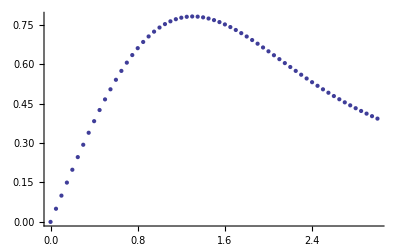

```mathematica
Table[{n Δt, x[[n+1]]},{n,0,M}];
sol = ListPlot[%]
```

The exact solution to this equation with the  initial condition x[0] = 0 is in terms of a special function called an error function:

```mathematica
Clear[x];
x[t_] =x[t]/.DSolve[{x'[t] + t x[t] == 1,x[0]==0},x[t],t][[1]]
```

ⅇ^(-t^2/2) √(π/2) Erfi[t/(√2)]

In Cell 2.96 we plot this solution and compare it with the numerics.

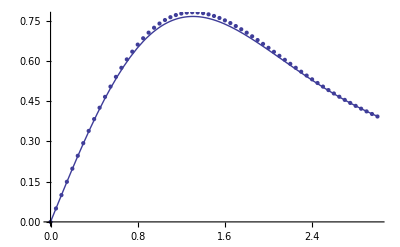

```mathematica
Plot[x[t],{t,0,3}];
Show[%,sol]
```

The match is reasonably good, and could be improved by taking a smaller step size, or by using a higher-order method to discretize the ODE.

Higher-order inhomogeneous  ODES  can also be written in the matrix form of Eq. (2.4.21 ) and solved by matrix inversion. Examples can be found in the exercises, and in Sec. 2.4.5 where boundary-value problems will be considered.

2.4.4 Green's Function for Boundary-Value Problems

Green's functions are often used to find particular solutions to inhomogeneous linear boundary-value problems. For example, Green's functions play a very important role in solutions to electrostatics problems. Such problems typically involve solution of Poisson's equation, Eq. (1.1.10), for the potential ϕ(r)  due to a given charge distribution ρ(r), in the presence of conductors that determine the boundary conditions for the potential.

Poisson's equation is a PDE, so its complete solution via Green's function techniques will be left to Chapters 3 and 4. However, it is enlightening to use a Green's function for Poisson's equation in the case where there is only variation in one direction. If we call this direction x,  then Poisson's equation is the following ODE:

L̂ ϕ(x)=ρ(x),

where L̂ is a second-order linear differential operator in x whose form depends on the geometry of the system. For example, for Cartesian coordinates, L̂=∂^2/(∂x^2), whereas for spherical coordinates with x= r, we have  L̂=∂^2/(∂x^2)+ 2/x∂/(∂x).

Assuming that there are conductors at x=a and x=b (assuming a<b) with fixed potentials V_a and V_b respectively, the boundary conditions are

ϕ(a)=V_a,  ϕ(b)=V_b.

When solving Eqs. (2.4.25) and (2.4.26) analytically, as usual we break the solution into a homogeneous and a particular solution: ϕ=ϕ_h+ ϕ_p.  The homogeneous solution ϕ_h satisfies the boundary conditions without the source term:

L̂ ϕ_h(x)=0,    ϕ(a)=V_a,  ϕ(b)=V_b,

and the particular solution satisfies the inhomogeneous ODE,

L̂ ϕ_p(x)=ρ(x),   ϕ_p(a)= ϕ_p(b)=0.

The particular boundary conditions chosen here are a type of homogeneous boundary conditions. Such boundary conditions have the property that, for the forcing function ρ=0, a solution to Eq. (2.4.28) is ϕ_p=0. They are analogous to the homogeneous initial conditions introduced in the initial value problem discussed in the previous section. We will have much more to say about homogeneous boundary conditions in Chapters 3 and 4. Other boundary conditions could be chosen for ϕ_p (provided that  the boundary conditions on ϕ_h are modified correspondingly). These homogeneous boundary conditions are convenient because any inhomogeneous boundary conditions are then accounted for only through ϕ_h.

The  Green's function g(x,x_o) is used to determine the solution to Eq. (2.4.28). The Green's function is the solution to

L̂ g(x,x_o)=δ(x-x_o),    g(a,x_o)=g(b,x_o)=0.

Then Eq. (2.4.3) implies that the particular solution is

ϕ_p(x) = ∫_a^b g(x,x_o)ρ(x_o)ⅆ x_o.

The boundary conditions  ϕ_p(a)= ϕ_p(b)=0   are satisfied because g(a,x_o)=g(b,x_o)=0 for all values of x_o.

We can construct the Green's function for this problem by using solutions to the homogeneous ODE in a manner analogous to the method used for initial-value problems, discussed previously. The only change is that the boundary conditions on the Green's function are now different.

The second-order ODE has two independent homogeneous solutions ϕ_1(x) and ϕ_2(x). We construct the Green's function by choosing two different linear combinations of these two solutions that match the boundary conditions in different regions. For x<x_o, we choose the linear combination

(ϕ̄)_1(x)=ϕ_1(x) - (ϕ_1(a))/(ϕ_2(a))ϕ_2(x),

and for x>x_o we choose the combination

(ϕ̄)_2(x)=ϕ_1(x) - (ϕ_1(b))/(ϕ_2(b))ϕ_2(x).

These combinations are chosen so that (ϕ̄)_1(a)=(ϕ̄)_2(b)=0.Then the Green's function is

g(x,x_o)={C_1(ϕ̄)_1(x),    x<x_o,
C_2(ϕ̄)_2(x),    x>x_o,

where the constants C_1and C_2 must still be determined. This Green's function satisfies the boundary conditions given in Eq. (2.4.29), and also satisfies the ODE for x ≠ x_o, since L̂ g(x,x_o)=0 for x ≠ x_o.

To complete the solution, we need values for the constants  C_1and C_2 . These are determined by the condition that the Green's function is continuous at x=x_o, so that

C_1(ϕ̄)_1(x_o)=C_2(ϕ̄)_2(x_o),

Also, a second equation is provided by  the usual jump condition on the first derivative of g, obtained by integration of Eq. (2.4.29) from x_o^- to x_o^+,

∂/(∂x)g(x,x_o)|_(x=x_o^+)-∂/(∂x)g(x,x_o)|_(x=x_o^-)=1.
Substitution of Eq. (2.4.33) then yields

C_2(ϕ̄)_2'(x_o)-C_1(ϕ̄)_1'(x_o)=1.

Equation (2.4.34) and (2.4.35) can be solved for C_1 and C_2. The solution is

g(x,x_o)={-((ϕ̄)_2(x_o)(ϕ̄)_1(x))/(W(x_o)),   a<x<x_o,
-((ϕ̄)_1(x_o)(ϕ̄)_2(x))/(W(x_o)),   b> x>x_o,

where the Wronskian W(x) =(ϕ̄)_1'(x)(ϕ̄)_2(x)-(ϕ̄)_2'(x)(ϕ̄)_1(x)  again makes an appearance [see Eq. (2.4.8)]. Equation (2.4.36) can be used in Eq. (2.4.30) to determine the particular solution for any given charge density ρ(x). An alternative description of g in terms of eigenmodes  can be found in Chapter 4; see Eq. (4.3.16). 
	Note that, while this Greens function is a convenient choice for boundary value problems because it is zero on both boundaries, the previous Green’s function introduced for time dependent problems, Eqs. (2.4.8) and (2.4.9), which is zero only on the left boundary, is also perfectly valid. Use of different Greens functions simply produces particular solutions with different boundary conditions.

2.4.5 Discretized Green's Functions II: Boundary-Value Problems by Matrix Inversion

## Theory for Second-order ODEs

Equation (2.4.30) can be thought of as an operator equation,

ϕ_p=(L̂)^-1 ρ,

involving the linear integral operator (L̂)^-1 defined by

(L̂)^-1 ρ= ∫_a^b g(x,x_o)ρ(x_o)ⅆ x_o.

This subsection discusses the matrix inverse method that follows from discretization of Eq. (2.4.37). This method,  discussed previously for initial-value problems, is really most useful for determining the solution to boundary-value problems. We will apply this method to a general second-order ODE of the form

L̂ ϕ=ⅆ^2/(ⅆ x^2)ϕ+u_1(x)ⅆ/ⅆx ϕ+u_o(x)ϕ =ρ(x)

with boundary conditions

ϕ(a)=V_a,  ϕ(b)=V_b.

We solve this problem numerically on a grid of positions, x = x_n=a + n Δx specified by the step size Δx = (b-a)/M. Then Eq. (2.4.39) becomes a matrix equation that can be solved directly by matrix inversion.

First, we need to discretize the differential equation. To do so, we use a centered-difference scheme. For the first derivative, this involves the approximation

ⅆϕ/ⅆx (x_n) ≃(ϕ(x_n+ Δx) -ϕ(x_n- Δx))/(2 Δx)=(ϕ(x_(n+1)) -ϕ(x_(n-1)))/(2 Δx).

In the limit that Δx approaches zero, this approximation clearly approaches the slope of ϕ at x=x_n. Other schemes could also be used (Table 2.3), such as the scheme used in Euler's method. This is called a forward-difference scheme:

ⅆϕ/ⅆx (x_n) ≃(ϕ(x_n+ Δx) -ϕ(x_n))/Δx=(ϕ(x_(n+1)) -ϕ(x_n))/Δx.

One might also choose the backward-difference scheme,

ⅆϕ/ⅆx (x_n) ≃(ϕ(x_n) -ϕ(x_n- Δx))/Δx=(ϕ(x_n) -ϕ(x_(n-1)))/Δx,

but centered-differencing is the most accurate of the three methods (see the exercises). For the second derivative, we again use a centered difference,

(ⅆ^2 ϕ)/(ⅆ x^2)(x_n)=(ⅆϕ/ⅆx(x_(n+1/2))-ⅆϕ/ⅆx(x_(n-1/2)))/Δx=(ϕ(x_(n+1))-2 ϕ(x_n)+ϕ(x_(n-1)))/Δx^2.

Higher-order derivatives can also be differenced in this fashion. Several of these derivatives are given in Table 2.4. These difference forms are derived in the Appendix.  However, the first and second derivatives are all that we require here.

Table 2.3. Different Forms for Finite-Differenced First Derivatives: | 
ⅆϕ/ⅆx (x_n) ≃(ϕ(x_(n+1)) -ϕ(x_n))/Δx | Forward difference
ⅆϕ/ⅆx (x_n) ≃(ϕ(x_n) -ϕ(x_(n-1)))/Δx | Backward difference
ⅆϕ/ⅆx (x_n) ≃(ϕ(x_(n+1)) -ϕ(x_(n-1)))/(2 Δx) | Centered difference

Table2.4  Centered-Difference Forms for Some Derivatives.^a
ⅆϕ/ⅆx (x_n) ≃(ϕ(x_(n+1)) -ϕ(x_(n-1)))/(2 Δx)
(ⅆ^2 ϕ)/(ⅆ x^2)(x_n)≃(ϕ(x_(n+1))-2 ϕ(x_n)+ϕ(x_(n-1)))/Δx^2
(ⅆ^3 ϕ)/(ⅆ x^3)(x_n)≃(ϕ(x_(n+2))-2 ϕ(x_(n-1))+2 ϕ(x_(n-1))-ϕ(x_(n-2)))/(2 Δx^3)
(ⅆ^4 ϕ)/(ⅆ x^4)(x_n)≃(ϕ(x_(n+2))-4 ϕ(x_(n+1))+6ϕ(x_n)-4 ϕ(x_(n-1))+ϕ(x_(n-2)))/Δx^4
(ⅆ^5 ϕ)/(ⅆ x^5)(x_n)≃(ϕ(x_(n+3))-4ϕ(x_(n+2))+5ϕ(x_(n+1))-5 ϕ(x_(n-1))+4ϕ(x_(n-2))-ϕ(x_(n-3)))/(2 Δx^4)
(ⅆ^6 ϕ)/(ⅆ x^6)(x_n)≃(ϕ(x_(n+3))-6ϕ(x_(n+2))+15ϕ(x_(n+1))-20ϕ(x_n)+15 ϕ(x_(n-1))-6ϕ(x_(n-2))+ϕ(x_(n-3)))/Δx^4
^a All forms shown are accurate to order Δx^2

Using these centered-difference forms for the first and second derivatives, Eq. (2.4.39) becomes a series of coupled linear equations for ϕ(x_n):

(ϕ(x_(n+1))-2 ϕ(x_n)+ϕ(x_(n-1)))/Δx^2+u_1(x_n)(ϕ(x_(n+1)) -ϕ(x_(n-1)))/(2 Δx)+u_o(x_n)ϕ(x_n)=ρ(x_n),  0<n<M.

As indicated, this equation is correct only at interior points. At the end points n=0 and n=M we have the boundary conditions

ϕ(x_o)=V_a,   ϕ(x_M)=V_b.

Equations (2.4.45) and (2.4.46) provide M+1 equations in the M+1 unknowns ϕ(x_n),   n=0,1,2,...,M. We can write these equations as a matrix equation, and solve this equation directly by matrix inversion. When written as a matrix equation, Eqs. (2.4.45) and (2.4.46) take the form

L·ϕ=ρ,

where

ϕ={ϕ(x_o),ϕ(x_1),....,ϕ(x_M)}, 
ρ={V_a,ρ(x_1),ρ(x_2),....ρ(x_(M-1)),V_b},

and the M+1-by-M+1 matrix  L  is determined in terms of Kronecker δ-functions for the interior points as follows:

L_(n m)= (δ_(n+1,m)- 2 δ_(n m) +δ_(n-1,m))/Δx^2+ u_1(x_n)(δ_(n+1,m) - δ_(n-1,m))/(2 Δx ) + δ_(n m) u_o(x_n)

A 4-by-4 version of the resulting matrix is displayed below:

```mathematica
M=3; L = Table[KroneckerDelta[n,m](Subscript[u, o][n]-2/Δx^2) + KroneckerDelta[n+1,m](1/Δx^2+ Subscript[u, 1][n]/(2 Δx)) + KroneckerDelta[n-1,m](1/Δx^2 - Subscript[u, 1][n]/(2Δx)),{n,0,M},{m,0,M}];
MatrixForm[L]
```

(-2/Δx^2+u_o[0] | 1/Δx^2+u_1[0]/(2 Δx) | 0 | 0
1/Δx^2-u_1[1]/(2 Δx) | -2/Δx^2+u_o[1] | 1/Δx^2+u_1[1]/(2 Δx) | 0
0 | 1/Δx^2-u_1[2]/(2 Δx) | -2/Δx^2+u_o[2] | 1/Δx^2+u_1[2]/(2 Δx)
0 | 0 | 1/Δx^2-u_1[3]/(2 Δx) | -2/Δx^2+u_o[3])

While the middle rows are correct, the first and last rows must be changed to provide the right boundary conditions:

```mathematica
L[[1,1]] = 1; L[[1,2]]=0;
L[[M+1,M+1]]= 1; L[[M+1,M]]=0;
```

Now the matrix takes the form

```mathematica
MatrixForm[L]
```

(1 | 0 | 0 | 0
1/Δx^2-u_1[1]/(2 Δx) | -2/Δx^2+u_o[1] | 1/Δx^2+u_1[1]/(2 Δx) | 0
0 | 1/Δx^2-u_1[2]/(2 Δx) | -2/Δx^2+u_o[2] | 1/Δx^2+u_1[2]/(2 Δx)
0 | 0 | 0 | 1)

When this matrix is used in Eq. (2.4.47)  together with Eq. (2.4.48), the first and last equations now provide the correct boundary conditions, ϕ(x_o)=V_a,  ϕ(x_M)=V_b.

These boundary conditions are contained in the discretized forcing function ρ. One can also write the boundary conditions directly into the forcing function of the undiscretized ODE using δ-functions, in analogy to Eq. (2.4.24):

ⅆ^2/(ⅆ x^2)ϕ+u_1(x)ⅆ/ⅆx ϕ+u_o(x)ϕ =ρ(x)+V_a δ'(x-a)-V_b δ'(x-b),

with two homogeneous boundary conditions,  ϕ =0 for x=a^- and x=b^+. (Higher derivatives of ϕ cannot also be specified because the ODE is second order, so the solution is determined  by only two conditions.) The proof that this is equivalent to Eqs. (2.4.39) and (2.4.40) is left as an exercise. The full solution, satisfying the nonzero boundary conditions, is then determined by applying the Green's function to the new forcing function using Eq. (2.4.30). Again, we see that there is no real difference between homogeneous solutions to the ODE and inhomogeneous solutions: both can be written in terms of the Green's function. In fact, a general homogeneous solution can be determined directly in terms of the Green's function by applying Eqs. (2.4.37) and (2.3.42) to the forcing function in Eq. (2.4.50), taking ρ=0. The result is

ϕ_h(x)=-V_aⅆ/(ⅆ x_o)g(x,x_o)|_(x_o=a)+V_bⅆ/(ⅆ x_o)g(x,x_o)|_(x_o=b).

We can check that this result is correct by subsituting for g from Eq. (2.4.36), which after some work yields

ϕ_h(x) = V_a(ϕ̄)_2(x)/(ϕ̄)_2(a)+V_b(ϕ̄)_1(x)/(ϕ̄)_1(b).

Since the independent homogeneous solutions (ϕ̄)_1(x) and (ϕ̄)_2(x) are zero at a and b respectively, this expression for ϕ_h clearly matches the required boundary conditions.

One can see now why we have spent so much time discussing the particular solutions to ODEs as opposed to the homogeneous solutions: there is really no difference between them. Both types of solutions can be determined using the Green's function method. Boundary or initial conditions are just another type of forcing, concentrated at the edges of the domain. In later chapters we will often use this idea, or variations of it, to determine homogeneous solutions to boundary and initial-value problems.

Now that we have the matrix L, we can solve  the boundary-value problem (2.4.47) in a single step by matrix inversion:

ϕ=L^-1·ρ.

Equation (2.4.52)  a very elegant numerical solution to the general linear boundary-value problem. It is somewhat analogous to finding the Green's function and applying Eq. (2.4.37) to ρ(x), obtaining  the particular solution that equals zero on the boundaries.  However, in the Green's function method one must then add in a homogeneous solution to include the nonzero boundary conditions; but this is not necessary in Eq. (2.4.52).

A closer analytic analogy to Eq. (2.4.52)  is the application of Eq. (2.4.37)  to the forcing function of Eq. (2.4.50), which also has the nonzero boundary conditions built into the forcing function.

The matrix-inversion method has several distinct advantages compared to the shooting method discussed in Sec. 1.5, where initial guesses had to be made (which might be poor) and where the ODE had to be solved many times in order to converge to the correct boundary conditions. However, there are also several drawbacks to the matrix – inversion technique for boundary-value problems. First, the method works only for linear boundary-value problems, whereas the shooting method works for any boundary-value problem. Second, the matrix form of the operator L̂ can be quite complicated, particularly for high-order ODEs. Third, matrix inversion is a computationally time-consuming operation, although very fast codes that can be run on mainframes do exist. Using Mathematica,  the matrix inverse of a general 700-by-700 matrix takes roughly half a minute on a reasonably fast PC (as of summer 2001). This is fast enough for many problems. Furthermore, there are specialized methods of taking the inverse that rely on the fact that only terms near the diagonal of L are nonzero (the matrix is sparse). These methods are already built into Mathematica, and will not be discussed in detail here.

There is another  important point to make concerning the matrix-inverse solution provided by Eq. (2.4.52). We know that for reasonable initial-value problems, ("reasonable" in the sense of Theorem 1.1) a solution always exists and is unique . On the other hand, we know from Chapter 1 that for boundary-value problems the solution need not exist, and need not be unique. However,  we have now seen that the solutions to both initial-value and boundary-value problems consist of inverting a matrix L and acting on a vector (called  ρ for our boundary-value problem, and f for the  initial-value problem of Sec. 2.4.3).  There seems to be no obvious difference between the solutions of initial-  and boundary-value problems when they are written in the form of a matrix equation. Why is one case solvable and the other not (necessarily)? The answer lies in the form of the matrix L for each case. For boundary-value problems  the changes that we have to make to the first and last few rows of L, required in order to satisfy the boundary conditions, can lead (for certain parameter choices) to the matrix having a zero determinant. In this event the matrix inverse does not exist (see Sec. 9.5.2), and the solution, if any, cannot be written in the form of Eq. (2.4.52). For examples of how this can happen, see Exercises (10)(e) and (f).

## Example

As an example of the matrix-inversion method, let's solve for the potential between two conducting spheres, with radii a=1m and b=2m respectively. The inner sphere is at V_a= 5000 V, and the outer sphere is grounded, V_b=0. Between the spheres is a uniform charge density of ρ0 = 10^-6 C/m^3. The potential satisfies the 1D Poisson equation

∂^2/(∂r^2)ϕ+2/r ∂/(∂r)ϕ=-ρ_0/ϵ_o,

so we take u_1(r)=2/r and u_0(r) = 0 in Eq. (2.4.45).

The following Mathematica code will solve this problem, taking M=40 grid points. First, we define the grid r_n and set up the functions  u_o(r) and u_1(r) on the grid:

```mathematica
a = 1; b = 2; M=40;
Δx= (b-a)/M ;
r[n_]  = a + n Δx;
Subscript[u, o][n_] = 0;
Subscript[u, 1][n_] = 2/r[n];
```

We then reconstruct the matrix L, now using the full 41 by 41 form:

```mathematica
L = Table[KroneckerDelta[n,m](Subscript[u, o][n]-2/Δx^2) + KroneckerDelta[n+1,m](1/Δx^2+ Subscript[u, 1][n]/(2 Δx)) + KroneckerDelta[n-1,m](1/Δx^2 - Subscript[u, 1][n]/(2Δx)),{n,0,M},{m,0,M}];

L[[1,1]] = 1; L[[1,2]]=0;
L[[M+1,M+1]]= 1;L[[M+1,M]]=0;
```

Next, we set up the vector ρ:

```mathematica
Subscript[ϵ, o]= 8.85 10^-12;Subscript[V, a]= 5000; Subscript[V, b]= 0; ρ0=10^-6;
ρ= Table[-ρ0/Subscript[ϵ, o],{n,0,M}];
ρ[[1]]=Subscript[V, a];
ρ[[M+1]]=Subscript[V, b];
```

Finally, the electrostatic potential is determined by matrix inversion:

```mathematica
ϕ = Inverse[L].ρ;
```

It may be easily verified (using DSolve, for example)  that the exact solution  for the potential is given by ϕ(r)=-5000+10000/r+(7 ρ_o)/(6 ϵ_o)-ρ_o/(r ϵ_o)-(r^2 ρ_o)/(6 ϵ_o) (in SI units).  We compare the exact result with the numerical solution in Cell 2.104.

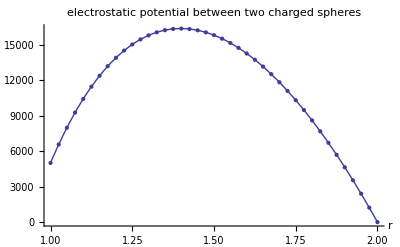

```mathematica
sol = Table[{r[n],ϕ[[n+1]]},{n,0,M}];
p1 = ListPlot[sol];
ϕexact[r_] = -5000+10000/r+(7 ρ0)/(6 Subscript[ϵ, o])-ρ0/(r Subscript[ϵ, o])-(r^2 ρ0)/(6 Subscript[ϵ, o]);
p2 = Plot[ϕexact[r],{r,1,2}];
Show[p1,p2,PlotLabel->"electrostatic potential between two charged spheres",AxesLabel->{"r"," "}]
```

This numerical method matches the analytic solution to the boundary-value problem quite nicely. For one-dimensional  linear boundary-value problems, matrix inversion is an excellent numerical method of solution.

Exercises for Sec. 2.4

(1)(a) Find the Green's function for the following potential problem in terms of homogeneous solutions:

ⅆ^2/(ⅆ x^2)ϕ = ρ(x), ϕ(0)=0, ϕ(b)=0.

(b) Use the Green's function to find a particular solution for the case where ρ(x)=x^3.

(2) Use the method of Sec. 2.4.2 to solve the following ODEs for the Green's function, for the given homogeneous boundary or initial conditions:

(a) G' + 3 t G(t,t_o) = δ(t-t_o), G=0 for t<t_o . Plot G(t,0).

(b) G'' +4G(t,t_o)=δ(t-t_o),G=0 for t<t_o. Plot G(t-t_o).

(c) G'' +2 G'+G(t,t_o)=δ(t-t_o), G=0 for t<t_o. Plot G(t-t_o).

(d) G'' + t G(t,t_o) = δ(t-t_o), G=0 for t<t_o (Hint: The solution will be in terms of Airy functions.) Plot G(t,0).

(e) G'''+2 G''-G'-2G=δ(t-t_o), G=0 for t<t_o. Plot G(t-t_o).

(f) G'' +ω_o^2 G(x,x_o)=δ(x-x_o),G=0 for x=a and x=b (ω_o real, ω_o ≠ n π/(b-a) for any integer n).

(g) G'' -κ_o^2 G(x,x_o)=δ(x-x_o),G=0 for x=a and x=b (κ_o real).

(h) G'' +n G'(x,x_o)/x=δ(x-x_o),G=0 for x=a>0 and x=b, n≠ 1.

(i) G'''+G''+G'+G=δ(x-x_o), G=G'=0 at x=0,G=0 at x=1. Plot G(x, 1/2).

(3) Use the Green's functions found from Exercise (2) to help determine solutions to the following problems. Plot the solution in each case.

(a) x' + 3 t x(t) = sin t, x=0 at t=0.

(b) x'' +4x(t)=cos 2 t,x(0)=0=x'(0).

(c) x'' +2 x'+x(t)=t^2, x(0)=1,x'(0)=0.

(d) x'' +t x(t)=t, x(0)=1,x'(0)=0.

(e) x'''+2 x''-x'-2x=ⅇ^-t, x(0)=1,x'(0)=x''(0)=0.

(f) ϕ'' +ϕ(x)=x^3,ϕ(0)=1 , ϕ(1)=0.

(g) ϕ'' -ϕ(x)=sin x,ϕ'(0)=0 =ϕ(1).

(h) ϕ'' +3 ϕ'/x=x,ϕ(1)=0,  ϕ'(2)=1.

(i) ϕ'''+ϕ''+ϕ'+ϕ=x ⅇ^-x,   ϕ=ϕ'=0 at x=0,   ϕ-2 ϕ'=1 at x=1.

(4) Discretize the operator in Exercise (3)(a) using Euler's method, and solve the problem by matrix inversion for 0<t<8. Take Δt=0.1, and compare with the exact solution by plotting both in the same plot.

(5) (a) By writing the ODE in Exercise (3)(b) as a vector ODE in the unknown vector function z(t)={x(t),x'(t)}, discretize the ODE using the vector Euler's method, and solve by matrix inversion for 0<t<5. Take Δt = 0.05.  Plot the result along with the exact solution. (See. Sec. 1.4.5.)

(b) Repeat for Exercise (3)(c)

(c) Repeat for Exercise (3)(d)

(d) Repeat for Exercise (3)(e), now taking the vector function as z(t) = {x(t),x'(t),x''(t)}.

(6) (a) For the following general second-order ODE initial-value problem, find a way of including the initial conditions in the forcing function on the right-hand side, in analogy to Eq. (2.4.24), and state the proper homogeneous initial condition for the new ODE:

(ⅆ^2 x)/(ⅆ t^2)+ u_1(t)ⅆx/ⅆt+ u_o(t)x(t)=f(t), x(t_o)=x_o, x'(t_o)=v_o.

(b) Using the result of part (a) along with Eq. (2.4.3),write a general homogeneous solution x_h(t) to this problem in terms of the Green's function.

(c) Use the Green's function found in Exercise (2)(c) and the result from part (b) to solve the following problem:

(ⅆ^2 x)/(ⅆ t^2)+ 2 ⅆx/ⅆt+ x(t)=ⅇ^-t, x(0)=1,x'(0)=2.

(7) In this problem we will show that the centered difference scheme for taking a numerical derivative is more accurate than either forward- or backward-differencing. To do so, take a smooth function ϕ(x) whose derivative we will determine numerically at a grid point x=x_n. Then the value of ϕ(x) at x=x_(n+1)can be determined by Taylor expansion:

ϕ_(n+1)=ϕ_n+Δx ϕ'_n+Δx^2 ϕ''_n/2 +Δx^3 ϕ'''_n/6 +...,

with a similar result for ϕ_(n-1).

(a) Use these Taylor expansions in the forward- and backward-difference methods,  Eqs. (2.4.42) and (2.4.43), to show that the error in these methods is of order Δx.

(b) Use these Taylor expansions in the centered-difference derivative, Eq. (2.4.41),  to show that the error in this method is of order Δx^2.

(c) Repeat for the centered-difference second derivative, Eq. (2.4.44), to show that the error is also of order Δx^2.

(8)(a) Prove Eq. (2.4.50).

(b) Prove Eq. (2.4.51).

(c) Test Eq. (2.4.51) directly for the potential problem given in Exercise (1) of this section: by applying the Green's function found in Exercise (1)(a) to Eq. (2.4.51), show that the correct homogeneous solution to this potential problem is recovered.

(9)(a) Find a way to include the boundary conditions in the forcing function for the following second-order boundary-value problem:

ⅆ^2/(ⅆ x^2)ϕ+u_1(x)ⅆ/ⅆx ϕ+u_o(x)ϕ =ρ(x), ϕ'(a)=V_a,ϕ'(b)=V_b .

What homogeneous boundary conditions must be attached to the new ODE? (Hint: they differ from the conditions for Eq. (2.4.50)).

(b) Using the result of part (a) along with Eq. (2.4.3), write a general homogeneous solution x_h(t) to this problem in terms of the Green's function.

(c) Using the results of part (a) and (b), find the appropriate Green's function in terms of homogeneous solutions and solve the following boundary-value problem:

ⅆ^2/(ⅆ x^2)ϕ+4 ⅆ/ⅆx ϕ+ϕ =x, ϕ'(0)=0, ϕ'(1)=1.

(10) Using the centered-difference discretization techniques discussed in Sec. 2.4.5, solve the following problems using matrix inversion, and compare each to the exact solution. In each case take M=40:

(a) Exercise (3)(f).

(b) Exercise (3)(g) (Hint: To learn about setting the derivative equal to zero at the boundary, see Sec. 6.2.1, in the sub-subsection on Neumann and mixed boundary conditions.)

(c) Exercise (3)(h) [see the hint for Exercise (10)(b)].

(d) Exercise (3)(i) [see the hint for Exercise (10) (b)].

(e) ϕ''(x) = 1, ϕ'(0)=2; ϕ'(1)=0. [Hint: First solve this problem analytically by direct integration to show that a solution does not exist. Then solve the problem by finite differencing. Also, see the hint for Exercise (10(b).]

(f) ϕ''(x) + ϕ(x) = 0, ϕ(0)=0=ϕ(π) [Hint: Recall that there are an infinite number of solutions; see Eq. (1.5.9). Take Δx = 0.05 π.]

## References

J. W. Bradbury and S. L. Vehrencamp, Principles of Animal Communication (Sinauer Associates, Sunderland, MA, 1998). An introductory reference on the auditory system.

W. F. Hartmann, How we localize sound, Phys. Today, November 1999, p. 24.